## Formulation

```mathematica
Clear[η,t,ϕ1,ϕ11,ϕ12,ϕ13,ϕ2,ϕ21,ϕ22,ϕ23, η1, η2, η3]
ϕ1[a_,b_,c_,d_]:=e*ϕ11[a,b,c,d]+e^2*ϕ12[a,b,c,d]+e^3*ϕ13[a,b,c,d];
ϕ2[a_,b_,c_,d_]:=e*ϕ21[a,b,c,d]+e^2*ϕ22[a,b,c,d]+e^3*ϕ23[a,b,c,d];
η[a_,b_,c_]:=e* η1[a,b,c]+e^2* η2[a,b,c]+e^3* η3[a,b,c];
```

```mathematica
nhat={1,-e/r D[η[θ,φ,t],θ],-e/(r*Sin[θ])D[η[θ,φ,t],φ]}/(√(1+(-e/r D[η[θ,φ,t],θ])^2+(e/(r*Sin[θ])D[η[θ,φ,t],φ])^2));
```

```mathematica
kinematicst=η[θ,φ,t]+Grad[ϕ1[r,θ,φ,t],{r,θ,φ},"Spherical"].Grad[η[θ,φ,t],{r,θ,φ},"Spherical"]-D[ϕ1[r,θ,φ,t],r]
```

e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t]+(Csc[θ]^2 (e η1^(0,1,0)[θ,φ,t]+e^2 η2^(0,1,0)[θ,φ,t]+e^3 η3^(0,1,0)[θ,φ,t]) (e ϕ11^(0,0,1,0)[r,θ,φ,t]+e^2 ϕ12^(0,0,1,0)[r,θ,φ,t]+e^3 ϕ13^(0,0,1,0)[r,θ,φ,t]))/r^2+((e η1^(1,0,0)[θ,φ,t]+e^2 η2^(1,0,0)[θ,φ,t]+e^3 η3^(1,0,0)[θ,φ,t]) (e ϕ11^(0,1,0,0)[r,θ,φ,t]+e^2 ϕ12^(0,1,0,0)[r,θ,φ,t]+e^3 ϕ13^(0,1,0,0)[r,θ,φ,t]))/r^2-e ϕ11^(1,0,0,0)[r,θ,φ,t]-e^2 ϕ12^(1,0,0,0)[r,θ,φ,t]-e^3 ϕ13^(1,0,0,0)[r,θ,φ,t]

```mathematica
kinematicst/.r->1+η[θ,φ,t]
```

e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t]+(Csc[θ]^2 (e η1^(0,1,0)[θ,φ,t]+e^2 η2^(0,1,0)[θ,φ,t]+e^3 η3^(0,1,0)[θ,φ,t]) (e ϕ11^(0,0,1,0)[1+e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t],θ,φ,t]+e^2 ϕ12^(0,0,1,0)[1+e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t],θ,φ,t]+e^3 ϕ13^(0,0,1,0)[1+e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t],θ,φ,t]))/(1+e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t])^2+((e η1^(1,0,0)[θ,φ,t]+e^2 η2^(1,0,0)[θ,φ,t]+e^3 η3^(1,0,0)[θ,φ,t]) (e ϕ11^(0,1,0,0)[1+e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t],θ,φ,t]+e^2 ϕ12^(0,1,0,0)[1+e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t],θ,φ,t]+e^3 ϕ13^(0,1,0,0)[1+e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t],θ,φ,t]))/(1+e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t])^2-e ϕ11^(1,0,0,0)[1+e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t],θ,φ,t]-e^2 ϕ12^(1,0,0,0)[1+e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t],θ,φ,t]-e^3 ϕ13^(1,0,0,0)[1+e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t],θ,φ,t]

```mathematica
Series[kinematicst/.r->1+η[θ,φ,t],{δ,0,1},{e,0,3}]//Normal
```

e (η1[θ,φ,t]-ϕ11^(1,0,0,0)[1,θ,φ,t])+e^2 (η2[θ,φ,t]+Csc[θ]^2 η1^(0,1,0)[θ,φ,t] ϕ11^(0,0,1,0)[1,θ,φ,t]+η1^(1,0,0)[θ,φ,t] ϕ11^(0,1,0,0)[1,θ,φ,t]-ϕ12^(1,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t])+e^3 (η3[θ,φ,t]+(-2 η1[θ,φ,t] η1^(1,0,0)[θ,φ,t]+η2^(1,0,0)[θ,φ,t]) ϕ11^(0,1,0,0)[1,θ,φ,t]-ϕ13^(1,0,0,0)[1,θ,φ,t]+Csc[θ]^2 ((-2 η1[θ,φ,t] η1^(0,1,0)[θ,φ,t]+η2^(0,1,0)[θ,φ,t]) ϕ11^(0,0,1,0)[1,θ,φ,t]+η1^(0,1,0)[θ,φ,t] (ϕ12^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,0,1,0)[1,θ,φ,t]))+η1^(1,0,0)[θ,φ,t] (ϕ12^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,1,0,0)[1,θ,φ,t])-η2[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ12^(2,0,0,0)[1,θ,φ,t]-1/2 η1[θ,φ,t]^2 ϕ11^(3,0,0,0)[1,θ,φ,t])

```mathematica
nopen=(Grad[ϕ2[r,θ,φ,t],{r,θ,φ},"Spherical"]-Grad[ϕ1[r,θ,φ,t],{r,θ,φ},"Spherical"]).nhat
```

-((e Csc[θ] (e η1^(0,1,0)[θ,φ,t]+e^2 η2^(0,1,0)[θ,φ,t]+e^3 η3^(0,1,0)[θ,φ,t]) (-(Csc[θ] (e ϕ11^(0,0,1,0)[r,θ,φ,t]+e^2 ϕ12^(0,0,1,0)[r,θ,φ,t]+e^3 ϕ13^(0,0,1,0)[r,θ,φ,t]))/r+(Csc[θ] (e ϕ21^(0,0,1,0)[r,θ,φ,t]+e^2 ϕ22^(0,0,1,0)[r,θ,φ,t]+e^3 ϕ23^(0,0,1,0)[r,θ,φ,t]))/r))/(r √(1+(e^2 Csc[θ]^2 (e η1^(0,1,0)[θ,φ,t]+e^2 η2^(0,1,0)[θ,φ,t]+e^3 η3^(0,1,0)[θ,φ,t])^2)/r^2+(e^2 (e η1^(1,0,0)[θ,φ,t]+e^2 η2^(1,0,0)[θ,φ,t]+e^3 η3^(1,0,0)[θ,φ,t])^2)/r^2)))-(e (e η1^(1,0,0)[θ,φ,t]+e^2 η2^(1,0,0)[θ,φ,t]+e^3 η3^(1,0,0)[θ,φ,t]) (-(e ϕ11^(0,1,0,0)[r,θ,φ,t]+e^2 ϕ12^(0,1,0,0)[r,θ,φ,t]+e^3 ϕ13^(0,1,0,0)[r,θ,φ,t])/r+(e ϕ21^(0,1,0,0)[r,θ,φ,t]+e^2 ϕ22^(0,1,0,0)[r,θ,φ,t]+e^3 ϕ23^(0,1,0,0)[r,θ,φ,t])/r))/(r √(1+(e^2 Csc[θ]^2 (e η1^(0,1,0)[θ,φ,t]+e^2 η2^(0,1,0)[θ,φ,t]+e^3 η3^(0,1,0)[θ,φ,t])^2)/r^2+(e^2 (e η1^(1,0,0)[θ,φ,t]+e^2 η2^(1,0,0)[θ,φ,t]+e^3 η3^(1,0,0)[θ,φ,t])^2)/r^2))+(-e ϕ11^(1,0,0,0)[r,θ,φ,t]-e^2 ϕ12^(1,0,0,0)[r,θ,φ,t]-e^3 ϕ13^(1,0,0,0)[r,θ,φ,t]+e ϕ21^(1,0,0,0)[r,θ,φ,t]+e^2 ϕ22^(1,0,0,0)[r,θ,φ,t]+e^3 ϕ23^(1,0,0,0)[r,θ,φ,t])/(√(1+(e^2 Csc[θ]^2 (e η1^(0,1,0)[θ,φ,t]+e^2 η2^(0,1,0)[θ,φ,t]+e^3 η3^(0,1,0)[θ,φ,t])^2)/r^2+(e^2 (e η1^(1,0,0)[θ,φ,t]+e^2 η2^(1,0,0)[θ,φ,t]+e^3 η3^(1,0,0)[θ,φ,t])^2)/r^2))

```mathematica
curvature=2/r+(-Csc[θ]^2 Derivative[0,2,0][η][θ,φ,t]-Cot[θ] Derivative[1,0,0][η][θ,φ,t]-Derivative[2,0,0][η][θ,φ,t])/r^2+1/r^4(Csc[θ]^2 Derivative[0,2,0][η][θ,φ,t] (Derivative[1,0,0][η][θ,φ,t])^2+Cot[θ] (Derivative[1,0,0][η][θ,φ,t])^3+2 Csc[θ]^2 Derivative[0,1,0][η][θ,φ,t] Derivative[1,0,0][η][θ,φ,t] Derivative[1,1,0][η][θ,φ,t]+3 (Derivative[1,0,0][η][θ,φ,t])^2 Derivative[2,0,0][η][θ,φ,t]);
```

```mathematica
Clear[ρ1,ρ2,We];
normalst=(ρ1*(D[ϕ1[r,θ,φ,t],t]+1/2((Csc[θ]^2 D[ϕ1[r,θ,φ,t],φ]^2)/r^2+D[ϕ1[r,θ,φ,t],θ]^2/r^2+D[ϕ1[r,θ,φ,t],r]^2))-ρ2*(D[ϕ2[r,θ,φ,t],t]+1/2((Csc[θ]^2 D[ϕ2[r,θ,φ,t],φ]^2)/r^2+D[ϕ2[r,θ,φ,t],θ]^2/r^2+D[ϕ2[r,θ,φ,t],r]^2)))-1/We*(curvature);(*e*(1+η[θ,φ,t])*Cos[θ]*Sin[t]*)
```

```mathematica
η[θ,φ,t]
```

e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t]

```mathematica
kinematicst
```

e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t]+(Csc[θ]^2 (e η1^(0,1,0)[θ,φ,t]+e^2 η2^(0,1,0)[θ,φ,t]+e^3 η3^(0,1,0)[θ,φ,t]) (e ϕ11^(0,0,1,0)[r,θ,φ,t]+e^2 ϕ12^(0,0,1,0)[r,θ,φ,t]+e^3 ϕ13^(0,0,1,0)[r,θ,φ,t]))/r^2+((e η1^(1,0,0)[θ,φ,t]+e^2 η2^(1,0,0)[θ,φ,t]+e^3 η3^(1,0,0)[θ,φ,t]) (e ϕ11^(0,1,0,0)[r,θ,φ,t]+e^2 ϕ12^(0,1,0,0)[r,θ,φ,t]+e^3 ϕ13^(0,1,0,0)[r,θ,φ,t]))/r^2-e ϕ11^(1,0,0,0)[r,θ,φ,t]-e^2 ϕ12^(1,0,0,0)[r,θ,φ,t]-e^3 ϕ13^(1,0,0,0)[r,θ,φ,t]

```mathematica
kinematicstpertr1=Series[kinematicst/.r->1+η[θ,φ,t],{δ,0,1},{e,0,3}]//Normal
```

e (η1[θ,φ,t]-ϕ11^(1,0,0,0)[1,θ,φ,t])+e^2 (η2[θ,φ,t]+Csc[θ]^2 η1^(0,1,0)[θ,φ,t] ϕ11^(0,0,1,0)[1,θ,φ,t]+η1^(1,0,0)[θ,φ,t] ϕ11^(0,1,0,0)[1,θ,φ,t]-ϕ12^(1,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t])+e^3 (η3[θ,φ,t]+(-2 η1[θ,φ,t] η1^(1,0,0)[θ,φ,t]+η2^(1,0,0)[θ,φ,t]) ϕ11^(0,1,0,0)[1,θ,φ,t]-ϕ13^(1,0,0,0)[1,θ,φ,t]+Csc[θ]^2 ((-2 η1[θ,φ,t] η1^(0,1,0)[θ,φ,t]+η2^(0,1,0)[θ,φ,t]) ϕ11^(0,0,1,0)[1,θ,φ,t]+η1^(0,1,0)[θ,φ,t] (ϕ12^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,0,1,0)[1,θ,φ,t]))+η1^(1,0,0)[θ,φ,t] (ϕ12^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,1,0,0)[1,θ,φ,t])-η2[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ12^(2,0,0,0)[1,θ,φ,t]-1/2 η1[θ,φ,t]^2 ϕ11^(3,0,0,0)[1,θ,φ,t])

```mathematica
Coefficient[kinematicstpertr1,e^3]
```

η3[θ,φ,t]+(-2 η1[θ,φ,t] η1^(1,0,0)[θ,φ,t]+η2^(1,0,0)[θ,φ,t]) ϕ11^(0,1,0,0)[1,θ,φ,t]-ϕ13^(1,0,0,0)[1,θ,φ,t]+Csc[θ]^2 ((-2 η1[θ,φ,t] η1^(0,1,0)[θ,φ,t]+η2^(0,1,0)[θ,φ,t]) ϕ11^(0,0,1,0)[1,θ,φ,t]+η1^(0,1,0)[θ,φ,t] (ϕ12^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,0,1,0)[1,θ,φ,t]))+η1^(1,0,0)[θ,φ,t] (ϕ12^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,1,0,0)[1,θ,φ,t])-η2[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ12^(2,0,0,0)[1,θ,φ,t]-1/2 η1[θ,φ,t]^2 ϕ11^(3,0,0,0)[1,θ,φ,t]

```mathematica
nopenstpertr1=Series[nopen/.r->1+η[θ,φ,t],{δ,0,1},{e,0,3}]//Normal
```

e (-ϕ11^(1,0,0,0)[1,θ,φ,t]+ϕ21^(1,0,0,0)[1,θ,φ,t])+e^2 (-ϕ12^(1,0,0,0)[1,θ,φ,t]+ϕ22^(1,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t])+e^3 (Csc[θ] η1^(0,1,0)[θ,φ,t] (Csc[θ] ϕ11^(0,0,1,0)[1,θ,φ,t]-Csc[θ] ϕ21^(0,0,1,0)[1,θ,φ,t])+η1^(1,0,0)[θ,φ,t] (ϕ11^(0,1,0,0)[1,θ,φ,t]-ϕ21^(0,1,0,0)[1,θ,φ,t])-ϕ13^(1,0,0,0)[1,θ,φ,t]+ϕ23^(1,0,0,0)[1,θ,φ,t]-η2[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ12^(2,0,0,0)[1,θ,φ,t]+η2[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ22^(2,0,0,0)[1,θ,φ,t]-1/2 η1[θ,φ,t]^2 ϕ11^(3,0,0,0)[1,θ,φ,t]+1/2 η1[θ,φ,t]^2 ϕ21^(3,0,0,0)[1,θ,φ,t])

```mathematica
normalstpertr1=Series[normalst/.r->1+η[θ,φ,t],{δ,0,1},{e,0,3}]//Normal
```

-2/We+e ((2 η1[θ,φ,t]+Csc[θ]^2 η1^(0,2,0)[θ,φ,t]+Cot[θ] η1^(1,0,0)[θ,φ,t]+η1^(2,0,0)[θ,φ,t])/We+ρ1 ϕ11^(0,0,0,1)[1,θ,φ,t]-ρ2 ϕ21^(0,0,0,1)[1,θ,φ,t])+e^2 (1/We(-2 (η1[θ,φ,t]^2-η2[θ,φ,t])+Csc[θ]^2 η2^(0,2,0)[θ,φ,t]+Cot[θ] η2^(1,0,0)[θ,φ,t]+2 η1[θ,φ,t] (-Csc[θ]^2 η1^(0,2,0)[θ,φ,t]-Cot[θ] η1^(1,0,0)[θ,φ,t]-η1^(2,0,0)[θ,φ,t])+η2^(2,0,0)[θ,φ,t])+ρ1 (ϕ12^(0,0,0,1)[1,θ,φ,t]+1/2 (Csc[θ]^2 (ϕ11^(0,0,1,0)[1,θ,φ,t])^2+(ϕ11^(0,1,0,0)[1,θ,φ,t])^2+(ϕ11^(1,0,0,0)[1,θ,φ,t])^2)+η1[θ,φ,t] ϕ11^(1,0,0,1)[1,θ,φ,t])-1/2 ρ2 (2 ϕ22^(0,0,0,1)[1,θ,φ,t]+Csc[θ]^2 (ϕ21^(0,0,1,0)[1,θ,φ,t])^2+(ϕ21^(0,1,0,0)[1,θ,φ,t])^2+(ϕ21^(1,0,0,0)[1,θ,φ,t])^2+2 η1[θ,φ,t] ϕ21^(1,0,0,1)[1,θ,φ,t]))+e^3 (1/We(2 (η1[θ,φ,t]^3-2 η1[θ,φ,t] η2[θ,φ,t]+η3[θ,φ,t])+Csc[θ]^2 η3^(0,2,0)[θ,φ,t]-Csc[θ]^2 η1^(0,2,0)[θ,φ,t] (η1^(1,0,0)[θ,φ,t])^2-Cot[θ] (η1^(1,0,0)[θ,φ,t])^3+Cot[θ] η3^(1,0,0)[θ,φ,t]-2 Csc[θ]^2 η1^(0,1,0)[θ,φ,t] η1^(1,0,0)[θ,φ,t] η1^(1,1,0)[θ,φ,t]-(3 η1[θ,φ,t]^2-2 η2[θ,φ,t]) (-Csc[θ]^2 η1^(0,2,0)[θ,φ,t]-Cot[θ] η1^(1,0,0)[θ,φ,t]-η1^(2,0,0)[θ,φ,t])-3 (η1^(1,0,0)[θ,φ,t])^2 η1^(2,0,0)[θ,φ,t]+2 η1[θ,φ,t] (-Csc[θ]^2 η2^(0,2,0)[θ,φ,t]-Cot[θ] η2^(1,0,0)[θ,φ,t]-η2^(2,0,0)[θ,φ,t])+η3^(2,0,0)[θ,φ,t])+ρ1 (ϕ13^(0,0,0,1)[1,θ,φ,t]+η2[θ,φ,t] ϕ11^(1,0,0,1)[1,θ,φ,t]+η1[θ,φ,t] ϕ12^(1,0,0,1)[1,θ,φ,t]+1/2 (-2 η1[θ,φ,t] (ϕ11^(0,1,0,0)[1,θ,φ,t])^2+Csc[θ]^2 (-2 η1[θ,φ,t] (ϕ11^(0,0,1,0)[1,θ,φ,t])^2+2 ϕ11^(0,0,1,0)[1,θ,φ,t] (ϕ12^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,0,1,0)[1,θ,φ,t]))+2 ϕ11^(0,1,0,0)[1,θ,φ,t] (ϕ12^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,1,0,0)[1,θ,φ,t])+2 ϕ11^(1,0,0,0)[1,θ,φ,t] (ϕ12^(1,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]))+1/2 η1[θ,φ,t]^2 ϕ11^(2,0,0,1)[1,θ,φ,t])+ρ2 (-ϕ23^(0,0,0,1)[1,θ,φ,t]-η2[θ,φ,t] ϕ21^(1,0,0,1)[1,θ,φ,t]-η1[θ,φ,t] ϕ22^(1,0,0,1)[1,θ,φ,t]+1/2 (2 η1[θ,φ,t] (ϕ21^(0,1,0,0)[1,θ,φ,t])^2-Csc[θ]^2 (-2 η1[θ,φ,t] (ϕ21^(0,0,1,0)[1,θ,φ,t])^2+2 ϕ21^(0,0,1,0)[1,θ,φ,t] (ϕ22^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(1,0,1,0)[1,θ,φ,t]))-2 ϕ21^(0,1,0,0)[1,θ,φ,t] (ϕ22^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(1,1,0,0)[1,θ,φ,t])-2 ϕ21^(1,0,0,0)[1,θ,φ,t] (ϕ22^(1,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t]))-1/2 η1[θ,φ,t]^2 ϕ21^(2,0,0,1)[1,θ,φ,t]))

```mathematica
nopenpertr1=Series[nopen/.r->1+η[θ,φ,t],{δ,0,1},{e,0,3}]//Normal
```

e (-ϕ11^(1,0,0,0)[1,θ,φ,t]+ϕ21^(1,0,0,0)[1,θ,φ,t])+e^2 (-ϕ12^(1,0,0,0)[1,θ,φ,t]+ϕ22^(1,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t])+e^3 (Csc[θ] η1^(0,1,0)[θ,φ,t] (Csc[θ] ϕ11^(0,0,1,0)[1,θ,φ,t]-Csc[θ] ϕ21^(0,0,1,0)[1,θ,φ,t])+η1^(1,0,0)[θ,φ,t] (ϕ11^(0,1,0,0)[1,θ,φ,t]-ϕ21^(0,1,0,0)[1,θ,φ,t])-ϕ13^(1,0,0,0)[1,θ,φ,t]+ϕ23^(1,0,0,0)[1,θ,φ,t]-η2[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ12^(2,0,0,0)[1,θ,φ,t]+η2[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ22^(2,0,0,0)[1,θ,φ,t]-1/2 η1[θ,φ,t]^2 ϕ11^(3,0,0,0)[1,θ,φ,t]+1/2 η1[θ,φ,t]^2 ϕ21^(3,0,0,0)[1,θ,φ,t])

## DYnamics at successive orders

### O(e) response

```mathematica
realkl[k_,l_]:=Piecewise[{{(√2)*ComplexExpand[Re[SphericalHarmonicY[k,l,θ,φ]]]//FullSimplify,l>0},{SphericalHarmonicY[k,0,θ,0],l==0}}]
```

```mathematica
realklpt[k_,l_,a_,b_]:=Piecewise[{{(√2)*ComplexExpand[Re[SphericalHarmonicY[k,l,a,b]]]//FullSimplify,l>0},{SphericalHarmonicY[k,0,a,0],l==0}}]
```

```mathematica
Tan[ArcTan[3.456,1]]
```

0.289352

```mathematica
yk0[k_]:=SphericalHarmonicY[k,0,θ,0]
```

```mathematica
bkl0fun[0.026,2,1,1,1,2,1,2]
```

0.+c0 Cos[t]+d0 Sin[t]

```mathematica
Integrate[realklpt[2,0,θ,φ]*realklpt[2,0,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2Pi}]
```

1

```mathematica
Integrate[realklpt[2,0,θ,φ]*realklpt[3,0,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2Pi}]
```

0

```mathematica
DSolve[b''[t]+2*ddk*b'[t]+zk^2*b[t]==nkk*Sin[t],b[t],t]
```

{{b[t]→ⅇ^(t (-ddk-√(ddk^2-zk^2))) C[1]+ⅇ^(t (-ddk+√(ddk^2-zk^2))) C[2]+(-2 ddk nkk Cos[t]-nkk Sin[t]+nkk zk^2 Sin[t])/(1+4 ddk^2-2 zk^2+zk^4)}}

```mathematica
Coefficient[(-nkk Cos[t]+nkk zk^2 Cos[t]+2 ddk nkk Sin[t])/(1+4 ddk^2-2 zk^2+zk^4),Cos[t]]
```

(-nkk+nkk zk^2)/(1+4 ddk^2-2 zk^2+zk^4)

```mathematica
Coefficient[(-nkk Cos[t]+nkk zk^2 Cos[t]+2 ddk nkk Sin[t])/(1+4 ddk^2-2 zk^2+zk^4),Sin[t]]
```

(2 ddk nkk)/(1+4 ddk^2-2 zk^2+zk^4)

```mathematica
bkl0fun[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_,n_]:=(Clear[c0,d0,m1k,m2k];
wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);(*kr=number of resonance mode, e.g., kr=3*)
delta=oh/wem;
qk=Integrate[realklpt[k,0,θ,φ]*realklpt[k,l,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2Pi}];
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));nk=((ρ1-ρ2)*k*(k+1))/(ρ1(k+1)+ρ2*k)*√((2k+1)/(4*Pi))*qk;fk=(k(k+1))/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;
(*m1k=If[Δk==0&&ζk==1,0,(nk (-1+ζk))/(4 Δk^2+(-1+ζk)^2)];*)
m2k=(nk (-1+ζk^2))/(4 Δk^2+(-1+ζk^2)^2);m1k=(-2 Δk*nk)/(4 Δk^2+(-1+ζk^2)^2);(*
m2k=If[Δk==0&&ζk==1,0,(2 Δk*nk)/(4 Δk^2+(-1+ζk)^2)];*)

(*If[k==kr,ζk=1];*)
bkl0amp=If[k==m&&l==n,(cmn*Cos[ζk*t]+dmn*Sin[ζk*t])+m1k*Cos[t]+m2k*Sin[t],m1k*Cos[t]+m2k*Sin[t]])(*leading order amplitude of different modes at the resonance frequency kr*)
```

```mathematica
bkl0fun[0.027,0.7,0.3,0.5,0.5,2,0,2,1]
```

0.-16.6132 Cos[t]

```mathematica
magkl1mn[0.027,0.7,0.3,0.5,0.5,2,0,2]
```

16.6132

```mathematica
psikl1mn[0.027,0.7,0.3,0.5,0.5,2,0,2]
```

0.

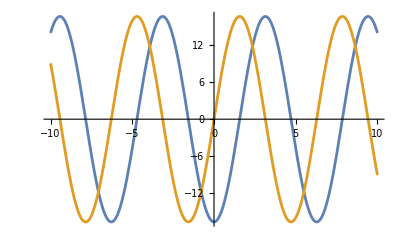

```mathematica
Plot[{16.61321825198459*Sin[t-1.5708],16.61321825198459 Sin[t]},{t,-10,10}]
```

```mathematica
Clear[nk,ζk,Δk]
```

```mathematica
m1k=(nk (-1+ζk^2))/(4 Δk^2+(-1+ζk^2)^2);m2k=(2 Δk*nk)/(4 Δk^2+(-1+ζk^2)^2);
```

```mathematica
(m1k^2+m2k^2)^(1/2)//FullSimplify
```

√(nk^2/(4 Δk^2+(-1+ζk^2)^2))

```mathematica
magkl1mn[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_]:=(Clear[c0,d0,m1k,m2k];
wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);(*kr=number of resonance mode, e.g., kr=3*)
delta=oh/wem;
qk=Integrate[realklpt[k,0,θ,φ]*realklpt[k,l,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2Pi}];
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));nk=((ρ1-ρ2)*k*(k+1))/(ρ1(k+1)+ρ2*k)*√((2k+1)/(4*Pi))*qk;fk=(k(k+1))/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;
(*m1k=(nk (-1+ζk^2))/(4 Δk^2+(-1+ζk^2)^2);m2k=(2 Δk*nk)/(4 Δk^2+(-1+ζk^2)^2);*)
magkl=Abs[nk]/(√((1-ζk^2)^2+4*Δk^2))
)
```

```mathematica
psikl1mn[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_]:=(Clear[tt,wem,psi];
wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);(*kr=number of resonance mode, e.g., kr=3*)
delta=oh/wem;
qk=Integrate[realklpt[k,0,θ,φ]*realklpt[k,l,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2Pi}];
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));nk=((ρ1-ρ2)*k*(k+1))/(ρ1(k+1)+ρ2*k)*√((2k+1)/(4*Pi))*qk;fk=(k(k+1))/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;

m1k=(nk (-1+ζk^2))/(4 Δk^2+(-1+ζk^2)^2);m2k=(2 Δk*nk)/(4 Δk^2+(-1+ζk^2)^2);
psi=ArcTan[m2k,m1k])
```

```mathematica
psikl1mn[oh_,k_,l_,kr_]:=(Clear[tt,wem,psi];
wem=(kr^2-1)(kr+2);
Δk=oh/(√wem)*(k+1)*(k+2);ζk=√(1/wem(k^2-1)(k+2));
qkl=Integrate[Cos[θ]*realkl[k,l]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}];

m1k=(nk (-1+ζk^2))/(4 Δk^2+(-1+ζk^2)^2);m2k=(2 Δk*nk)/(4 Δk^2+(-1+ζk^2)^2);
psi=ArcTan[d2,-d1])
```

```mathematica
Coefficient[(-nk Cos[t]+nk ζk^2 Cos[t]+2 ddk nkk Sin[t])/(1+4 ddk^2-2 zk^2+zk^4),Sin[t]]
```

```mathematica
bkl0fun[0.027,0.7,0.5,0.7,0.5,2,0,2,0]
```

0.+cmn Cos[1. t]-6.69888 Sin[t]+dmn Sin[1. t]

```mathematica
wesol[ρ1_,ρ2_,k_]:=we/.Solve[(k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)we)==1,we]
```

```mathematica
wesol[0.86,0.14,2]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{8.39161}

```mathematica
Integrate[realkl[3,0]*realkl[3,0]*Sin[θ],{θ,0,Pi},{φ,0,2Pi}]
```

1

```mathematica
(-2 ddk nkk Cos[t]-nkk Sin[t]+nkk zk^2 Sin[t])/(1+4 ddk^2-2 zk^2+zk^4)
```

```mathematica
bkl1trans[oh_,we_,ρ1_,ρ2_,μ1_,μ2_,k_,l_]:=(
(*kr=number of resonance mode, e.g., kr=3*)
delta=oh/we;
qk=Integrate[realklpt[k,0,θ,φ]*realklpt[k,l,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2Pi}];(*factor of 2 in front because of the inner product over hemisphere*)
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)we));nk=((ρ2-ρ1)*k*(k+1))/(ρ1(k+1)+ρ2*k)*√((2k+1)/(4*Pi))*qk;gk=(k(k+1))/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*gk;
m1k=If[Δk==0&&ζk==1,0,(nk (-1+ζk))/(4 Δk^2+(-1+ζk)^2)];
m2k=If[Δk==0&&ζk==1,0,(2 Δk*nk)/(4 Δk^2+(-1+ζk)^2)];(*

icsol={ckl,dkl}/.Flatten[Solve[{(ⅇ^(-t (Δk+√(Δk^2-ζk^2))) (ckl+dkl ⅇ^(2 t √(Δk^2-ζk^2)))+m1k*Cos[t]+m2k*Sin[t]/.t->0)==ic1,(D[ⅇ^(-t (Δk+√(Δk^2-ζk^2))) (ckl+dkl ⅇ^(2 t √(Δk^2-ζk^2)))+m1k*Cos[t]+m2k*Sin[t],t]/.t->0)==ic2},{ckl,dkl}]];*)
bkl1ivpsol=(-2 Δk nk Cos[t]-nk Sin[t]+nk ζk^2 Sin[t])/(1+4 Δk^2-2 ζk^2+ζk^4);
bkl1l2norm=(Integrate[(bkl1ivpsol)^2,{t,0,2Pi}])^(1/2)/(2Pi)//Chop

(*bkl0amp=(2 (1+k) qk (2 Δk Cos[t]+Sin[t]-ζk^2 Sin[t]))/(1+4 Δk^2-2 ζk^2+ζk^4)*)(*before forcing sign correction*)(*after forcing sign correction*)
)
```

```mathematica
[oh_,we_,ρ1_,ρ2_,μ1_,μ2_,k_,l_]
```

```mathematica
list2=Table[bkl1trans[0.043,we,0.86,0.14,0.71,0.29,2,0],{we,0.1,100,1}];
```

```mathematica
list3=Table[bkl1trans[0.043,we,0.86,0.14,0.71,0.29,3,0],{we,0.1,100,1}];
```

```mathematica
list4=Table[bkl1trans[0.043,we,0.86,0.14,0.71,0.29,4,0],{we,0.1,100,1}];
```

```mathematica
list5=Table[bkl1trans[0.043,we,0.86,0.14,0.71,0.29,5,0],{we,0.1,100,1}];
```

```mathematica
1
```

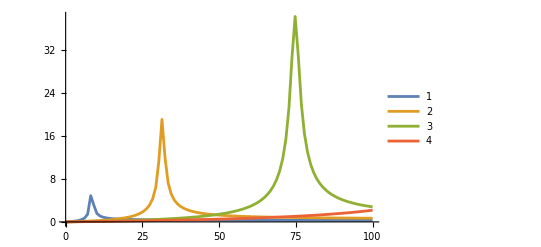

```mathematica
ListLinePlot[{list2,list3,list4,list5},DataRange->{0.1,100},PlotLegends->Automatic,PlotRange->All]
```

```mathematica
ζk
```

0.572075

```mathematica
nk
```

-0.968241

```mathematica
bkl0fun[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_,n_]:=(Clear[cmn,dmn,m1k,m2k];
wer=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);(*kr=number of resonance mode, e.g., kr=3*)
delta=oh/wer;
qk=Integrate[realklpt[k,0,θ,φ]*realklpt[k,l,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2Pi}];
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wer));nk=((ρ2-ρ1)*k*(k+1))/(ρ1(k+1)+ρ2*k)*√((2k+1)/(4*Pi))*qk;gk=(k(k+1))/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*gk;
(*m1k=If[Δk==0&&ζk==1,0,(nk (-1+ζk))/(4 Δk^2+(-1+ζk)^2)];*)
m1k=(nk (-1+ζk))/(4 Δk^2+(-1+ζk)^2);m2k=(2 Δk*nk)/(4 Δk^2+(-1+ζk)^2);(*
m2k=If[Δk==0&&ζk==1,0,(2 Δk*nk)/(4 Δk^2+(-1+ζk)^2)];*)

(*If[k==kr,ζk=1];*)
bkl0amp=If[k==m&&l==n,(cmn*Cos[ζk*t]+dmn*Sin[ζk*t])+m1k*Cos[t]+m2k*Sin[t],m1k*Cos[t]+m2k*Sin[t]])(*leading order amplitude of different modes at the resonance frequency kr*)
```

```mathematica
Clear[k]
```

```mathematica
bkl0fun[oh,ρ1,ρ2,μ1,μ2,k,l,m,n]
```

$Aborted

```mathematica
magkl1mn[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_,n_]:=(
wer=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);(*kr=number of resonance mode, e.g., kr=3*)
delta=oh/wer;
qkl=Integrate[realklpt[k,0,θ,φ]*realklpt[k,l,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2Pi}];
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wer));nk=((ρ2-ρ1)*k*(k+1))/(ρ1(k+1)+ρ2*k)*√((2k+1)/(4*Pi))*qk;gk=(k(k+1))/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*gk;
magkl=(2(k+1)*Abs[qkl])/(√((1-ζk^2)^2+4*Δk^2))
)
```

```mathematica
psikl1mn[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_,n_]:=(Clear[tt,wem,psi];
wer=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);(*kr=number of resonance mode, e.g., kr=3*)
delta=oh/wer;
qkl=Integrate[realklpt[k,0,θ,φ]*realklpt[k,l,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2Pi}];
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wer));nk=((ρ2-ρ1)*k*(k+1))/(ρ1(k+1)+ρ2*k)*√((2k+1)/(4*Pi))*qk;gk=(k(k+1))/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*gk;

d1=Coefficient[-2*Sign[qkl]*(k+1)((2 Δk Cos[tt]+Sin[tt]-ζk^2 Sin[tt])/(1+4 Δk^2-2 ζk^2+ζk^4)),Cos[tt]];
d2=Coefficient[-2*Sign[qkl]*(k+1)((2 Δk Cos[tt]+Sin[tt]-ζk^2 Sin[tt])/(1+4 Δk^2-2 ζk^2+ζk^4)),Sin[tt]];
psi=ArcTan[d2,-d1])
```

```mathematica
psikl1mn[0.02,0.7,0.3,0.2,0.8,2,0,2,0]
```

1.5708

### O(e) response

```mathematica
Clear[c0,d0,d2,d3,d4,d5,d6,b020,b021,b021t,b021tt,b121,b121t,b121tt,b020t,b020tt,b030,b030t,b030tt,b022,b022t,b022tt,b051,b051t,b051tt,b053,b053t,b053tt,b055,b055t,b055tt,b031,b031t,b031tt,b033,b033t,b033tt,b040,b040t,b040tt,b042,b042t,b042tt,b044,b044t,b044tt,b060,b060t,b060tt,b062,b062t,b062tt,b064,b064t,b064tt,b071,b071t,b071tt,b073,b073t,b073tt,delta,wer,b120,b122,b131,b133,b140,b142,b144,b151,b153,b155,b160,b162,b164,b171,b120t,b122t,b131t,b133t,b140t,b142t,b144t,b151t,b153t,b155t,b160t,b162t,b164t,b171t,b120tt,b122tt,b131tt,b133tt,b140tt,b142tt,b144tt,b151tt,b153tt,b155tt,b160tt,b162tt,b164tt,b171tt,p200t,p310t,p33t,p400t,p510t,p600t,p220t,p420t,p440t,p530t,p550t,p710t,p620t,p640t,p200,p310,p400,p510,p600,k121,k120,k130,n120,n121,n130,k121t,k120t,k130t];
```

```mathematica
(*the potential phi has two subscripts. first subscript=1 is inner fluid, =2 is outer fluid.*)
```

```mathematica
magkl1mn[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_,n_]
```

```mathematica
Clear[b201,b211,b301];
```

#### Set physical parameters here

```mathematica
ohn=(0.001+0.0024)/(√(1040+6440)*2.26*10^-3*0.403)
```

0.0431633

```mathematica
rho2=1040*1/(1040+6440)//N
```

0.139037

```mathematica
rho1=6440*1/(1040+6440)//N
```

0.860963

```mathematica
mu2=0.001*1/(0.001+0.0024)//N
```

0.294118

```mathematica
mu1=0.0024*1/(0.001+0.0024)//N
```

0.705882

```mathematica
Clear[etaa1,fi11,fi21,b201,b211,b301]
```

```mathematica
bkl0fun[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_,n_]
```

```mathematica
b201[s_]:=bkl0fun[ohn,rho1,rho2,mu1,mu2,2,0,2,1];
```

```mathematica
ohn=0.43 (*10 times higher than experiment*);rho2=.14;rho1=0.86;mu1=0.71;mu2=0.29;
```

```mathematica
bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,2,1]
```

(6 √(5/π) (-ρ1+ρ2) Sin[t])/(oh (μ1+4 μ2) (3 ρ1+2 ρ2))

```mathematica
b201[s_]:=bkl0fun[ohn,rho1,rho2,mu1,mu2,2,0,2,1];
b211[s_]:=c21*Cos[s]+d21*Sin[s];
b301[s_]:=bkl0fun[ohn,rho1,rho2,mu1,mu2,3,0,2,1];

etaa1[a_,b_,c_]:=b201[c]*realklpt[2,0,a,b]+b211[c]*realklpt[2,1,a,b]+b301[c]*realklpt[3,0,a,b]

fi11[rr_,a_,b_,c_]:=D[b201[c],c]/2*rr^2*realklpt[2,0,a,b]+D[b211[c],c]/2*rr^2*realklpt[2,1,a,b]+D[b301[c],c]/3*rr^3*realklpt[3,0,a,b]

fi21[rr_,a_,b_,c_]:=-D[b201[c],c]/(3 rr^3)*realklpt[2,0,a,b]-D[b211[c],c]/(4 rr^4)*realklpt[2,1,a,b]-D[b301[c],c]/(5 rr^5)*realklpt[3,0,a,b]
```

```mathematica
(*b201[c]*realklpt[2,0,a,b]+b211[c]*realklpt[2,1,a,b]+*)b301[c]*realklpt[3,0,a,b]
```

1/4 √(7/π) (-3 Cos[a]+5 Cos[a]^3) ((6 √(7/π) (-ρ1+ρ2) (-1+√5 √((3 ρ1+2 ρ2)/(4 ρ1+3 ρ2))) Cos[t])/((4 ρ1+3 ρ2) ((oh^2 (2 μ1+5 μ2)^2 (3 ρ1+2 ρ2)^2)/(4 ρ1+3 ρ2)^2+(-1+√5 √((3 ρ1+2 ρ2)/(4 ρ1+3 ρ2)))^2))+(6 oh √(7/π) (2 μ1+5 μ2) (-ρ1+ρ2) (3 ρ1+2 ρ2) Sin[t])/((4 ρ1+3 ρ2)^2 ((oh^2 (2 μ1+5 μ2)^2 (3 ρ1+2 ρ2)^2)/(4 ρ1+3 ρ2)^2+(-1+√5 √((3 ρ1+2 ρ2)/(4 ρ1+3 ρ2)))^2)))

```mathematica
b301[t]
```

(6 √(7/π) (-ρ1+ρ2) (-1+√5 √((3 ρ1+2 ρ2)/(4 ρ1+3 ρ2))) Cos[t])/((4 ρ1+3 ρ2) ((oh^2 (2 μ1+5 μ2)^2 (3 ρ1+2 ρ2)^2)/(4 ρ1+3 ρ2)^2+(-1+√5 √((3 ρ1+2 ρ2)/(4 ρ1+3 ρ2)))^2))+(6 oh √(7/π) (2 μ1+5 μ2) (-ρ1+ρ2) (3 ρ1+2 ρ2) Sin[t])/((4 ρ1+3 ρ2)^2 ((oh^2 (2 μ1+5 μ2)^2 (3 ρ1+2 ρ2)^2)/(4 ρ1+3 ρ2)^2+(-1+√5 √((3 ρ1+2 ρ2)/(4 ρ1+3 ρ2)))^2))

```mathematica
fi21[1,t,p,tt]
```

1/8 √(15/π) Cos[p] Cos[t] Sin[t] (d21 Cos[tt]-c21 Sin[tt])

#### kinematic equation

```mathematica
kinematicoe2=Coefficient[kinematicstpertr1,e^2]
```

η2[θ,φ,t]+Csc[θ]^2 η1^(0,1,0)[θ,φ,t] ϕ11^(0,0,1,0)[1,θ,φ,t]+η1^(1,0,0)[θ,φ,t] ϕ11^(0,1,0,0)[1,θ,φ,t]-ϕ12^(1,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]

```mathematica
etaa1[a,b,c]
```

-1/2 √(15/π) Cos[a] Cos[b] Sin[a] (c21 Cos[c]+d21 Sin[c])+(15 (-ρ1+ρ2) (-1+3 Cos[a]^2) Sin[t])/(2 oh π (μ1+4 μ2) (3 ρ1+2 ρ2))+1/4 √(7/π) (-3 Cos[a]+5 Cos[a]^3) ((6 √(7/π) (-ρ1+ρ2) (-1+√5 √((3 ρ1+2 ρ2)/(4 ρ1+3 ρ2))) Cos[t])/((4 ρ1+3 ρ2) ((oh^2 (2 μ1+5 μ2)^2 (3 ρ1+2 ρ2)^2)/(4 ρ1+3 ρ2)^2+(-1+√5 √((3 ρ1+2 ρ2)/(4 ρ1+3 ρ2)))^2))+(6 oh √(7/π) (2 μ1+5 μ2) (-ρ1+ρ2) (3 ρ1+2 ρ2) Sin[t])/((4 ρ1+3 ρ2)^2 ((oh^2 (2 μ1+5 μ2)^2 (3 ρ1+2 ρ2)^2)/(4 ρ1+3 ρ2)^2+(-1+√5 √((3 ρ1+2 ρ2)/(4 ρ1+3 ρ2)))^2)))

```mathematica
kkl1fun=Csc[θ]^2 Derivative[0,1,0][η1][θ,φ,t] Derivative[0,0,1,0][ϕ11][1,θ,φ,t]+Derivative[1,0,0][η1][θ,φ,t] Derivative[0,1,0,0][ϕ11][1,θ,φ,t]-η1[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]]} //Chop
```

-1/4 √(15/π) Cos[2 θ] Cos[φ] (d21 Cos[t]-c21 Sin[t]) (-1/2 √(15/π) Cos[2 θ] Cos[φ] (c21 Cos[t]+d21 Sin[t])+4.48455 Cos[θ] Sin[t] Sin[θ]+1/4 √(7/π) (-0.913448 Cos[t]-0.90321 Sin[t]) (3 Sin[θ]-15 Cos[θ]^2 Sin[θ]))+1/4 √(15/π) Cos[φ] (d21 Cos[t]-c21 Sin[t]) (1/4 √(7/π) (-3 Cos[θ]+5 Cos[θ]^3) (-0.913448 Cos[t]-0.90321 Sin[t])-0.747425 (-1+3 Cos[θ]^2) Sin[t]-1/2 √(15/π) Cos[θ] Cos[φ] (c21 Cos[t]+d21 Sin[t]) Sin[θ]) Sin[2 θ]+(15 Csc[θ]^2 (d21 Cos[t]-c21 Sin[t]) (c21 Cos[t]+d21 Sin[t]) Sin[2 θ]^2 Sin[φ]^2)/(32 π)

```mathematica
kkl1fun
```

-1/4 √(15/π) Cos[2 θ] Cos[φ] (d21 Cos[t]-c21 Sin[t]) (-1/2 √(15/π) Cos[2 θ] Cos[φ] (c21 Cos[t]+d21 Sin[t])+4.48455 Cos[θ] Sin[t] Sin[θ]+1/4 √(7/π) (-0.913448 Cos[t]-0.90321 Sin[t]) (3 Sin[θ]-15 Cos[θ]^2 Sin[θ]))+1/4 √(15/π) Cos[φ] (d21 Cos[t]-c21 Sin[t]) (1/4 √(7/π) (-3 Cos[θ]+5 Cos[θ]^3) (-0.913448 Cos[t]-0.90321 Sin[t])-0.747425 (-1+3 Cos[θ]^2) Sin[t]-1/2 √(15/π) Cos[θ] Cos[φ] (c21 Cos[t]+d21 Sin[t]) Sin[θ]) Sin[2 θ]+(15 Csc[θ]^2 (d21 Cos[t]-c21 Sin[t]) (c21 Cos[t]+d21 Sin[t]) Sin[2 θ]^2 Sin[φ]^2)/(32 π)

```mathematica
k201ff=Integrate[TrigReduce[kkl1fun]*realklpt[2,0,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]/.r->1//N//Simplify
```

0.0450559 c21 d21 Cos[2. t]+0.022528 (-1. c21^2+d21^2) Sin[2. t]

```mathematica
0.04505593789321714 c21 d21 Cos[2. t]+0.02252796894660857 (-1. c21^2+d21^2) Sin[2. t]-ⅇ^((0.-2. ⅈ) t) (d21^2 ((0.+0.01126398447330427 ⅈ)-(0.+0.01126398447330427 ⅈ) ⅇ^((0.+4. ⅈ) t))+c21^2 ((0.-0.01126398447330427 ⅈ)+(0.+0.01126398447330427 ⅈ) ⅇ^((0.+4. ⅈ) t))+c21 d21 (0.02252796894660854+0.02252796894660854 ⅇ^((0.+4. ⅈ) t)))/.{c21->1.2,d21->2.1}//FullSimplify//Chop
```

0

```mathematica
k201ff//Chop
```

ⅇ^((0.-2. ⅈ) t) (d21^2 ((0.+0.011264 ⅈ)-(0.+0.011264 ⅈ) ⅇ^((0.+4. ⅈ) t))+c21^2 ((0.-0.011264 ⅈ)+(0.+0.011264 ⅈ) ⅇ^((0.+4. ⅈ) t))+c21 d21 (0.022528+0.022528 ⅇ^((0.+4. ⅈ) t)))

```mathematica
k211ff=Integrate[TrigReduce[kkl1fun]*realklpt[2,1,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

0.0533875 c21-0.0533875 c21 Cos[2. t]-0.106775 d21 Cos[t] Sin[t]

```mathematica
k301ff=Integrate[TrigReduce[kkl1fun]*realklpt[3,0,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

ⅇ^((0.-2. ⅈ) t) (d21^2 ((0.+1.5763 ⅈ)-(0.+1.5763 ⅈ) ⅇ^((0.+4. ⅈ) t))+c21^2 ((0.-1.5763 ⅈ)+(0.+1.5763 ⅈ) ⅇ^((0.+4. ⅈ) t))+(6.30522 c21^2-6.30522 d21^2) ⅇ^((0.+2. ⅈ) t) Cos[t] Sin[t])

```mathematica
k301ff=Integrate[TrigReduce[kkl1fun]*realklpt[3,0,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

ⅇ^((0.-2. ⅈ) t) (d21^2 ((0.+1.5763 ⅈ)-(0.+1.5763 ⅈ) ⅇ^((0.+4. ⅈ) t))+c21^2 ((0.-1.5763 ⅈ)+(0.+1.5763 ⅈ) ⅇ^((0.+4. ⅈ) t))+(6.30522 c21^2-6.30522 d21^2) ⅇ^((0.+2. ⅈ) t) Cos[t] Sin[t])

```mathematica
ⅇ^((0.-2. ⅈ) t) (d21^2 ((0.+1.5763037827410658 ⅈ)-(0.+1.5763037827410664 ⅈ) ⅇ^((0.+4. ⅈ) t))+c21^2 ((0.-1.5763037827410662 ⅈ)+(0.+1.5763037827410664 ⅈ) ⅇ^((0.+4. ⅈ) t))+(6.305215130964263 c21^2-6.305215130964263 d21^2) ⅇ^((0.+2. ⅈ) t) Cos[t] Sin[t])/.{c21->2.1,d->-0.222}//FullSimplify
```

ⅇ^((0.-2. ⅈ) t) ((0.-3.55271×10^-15 ⅈ)+((0.+3.55271×10^-15 ⅈ)-(0.+6.66134×10^-16 ⅈ) d21^2) ⅇ^((0.+4. ⅈ) t))

```mathematica
ⅇ^((0.-2. ⅈ) t) ((0.-3.552713678800501*^-15 ⅈ)+((0.+3.552713678800501*^-15 ⅈ)-(0.+6.661338147750939*^-16 ⅈ) d21^2) ⅇ^((0.+4. ⅈ) t))//Chop
```

0

#### NO penetration

```mathematica
nopenoe2=Coefficient[nopenstpertr1,e^2]
```

-ϕ12^(1,0,0,0)[1,θ,φ,t]+ϕ22^(1,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t]

```mathematica
lkl1fun=η1[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]-η1[θ,φ,t] Derivative[2,0,0,0][ϕ21][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]]}
```

-3/2 √(15/π) Cos[φ] (d21 Cos[t]-c21 Sin[t]) (1/4 √(5/π) (-1+3 Cos[θ]^2) (6.54407×10^-16 Cos[t]-2.36983 Sin[t])+1/4 √(7/π) (-3 Cos[θ]+5 Cos[θ]^3) (-0.913448 Cos[t]-0.90321 Sin[t])-1/2 √(15/π) Cos[θ] Cos[φ] (c21 Cos[t]+d21 Sin[t]) Sin[θ]) Sin[2 θ]

```mathematica
l201ff=Integrate[TrigReduce[lkl1fun]*realklpt[2,0,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

0.540671 c21 d21 Cos[2. t]-0.270336 (c21^2-1. d21^2) Sin[2. t]

```mathematica
realklpt[3,0,t,p]
```

1/4 √(7/π) (-3 Cos[t]+5 Cos[t]^3)

```mathematica
l211ff=Integrate[TrigReduce[lkl1fun]*realklpt[2,1,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

0.64065 c21-0.64065 c21 Cos[2. t]-1.2813 d21 Cos[t] Sin[t]

```mathematica
realklpt[3,0,θ,φ]
```

1/4 √(7/π) (-3 Cos[θ]+5 Cos[θ]^3)

```mathematica
l301ff=Integrate[TrigReduce[lkl1fun]*realklpt[3,0,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

0.

#### normal stress equation

```mathematica
Clear[We]
```

```mathematica
normalstoe2=Coefficient[normalstpertr1,e^2]
```

(-2 (η1[θ,φ,t]^2-η2[θ,φ,t])+Csc[θ]^2 η2^(0,2,0)[θ,φ,t]+Cot[θ] η2^(1,0,0)[θ,φ,t]+2 η1[θ,φ,t] (-Csc[θ]^2 η1^(0,2,0)[θ,φ,t]-Cot[θ] η1^(1,0,0)[θ,φ,t]-η1^(2,0,0)[θ,φ,t])+η2^(2,0,0)[θ,φ,t])/We+ρ1 (ϕ12^(0,0,0,1)[1,θ,φ,t]+1/2 (Csc[θ]^2 (ϕ11^(0,0,1,0)[1,θ,φ,t])^2+(ϕ11^(0,1,0,0)[1,θ,φ,t])^2+(ϕ11^(1,0,0,0)[1,θ,φ,t])^2)+η1[θ,φ,t] ϕ11^(1,0,0,1)[1,θ,φ,t])-1/2 ρ2 (2 ϕ22^(0,0,0,1)[1,θ,φ,t]+Csc[θ]^2 (ϕ21^(0,0,1,0)[1,θ,φ,t])^2+(ϕ21^(0,1,0,0)[1,θ,φ,t])^2+(ϕ21^(1,0,0,0)[1,θ,φ,t])^2+2 η1[θ,φ,t] ϕ21^(1,0,0,1)[1,θ,φ,t])

```mathematica
nkl1fun=(-2 (η1[θ,φ,t]^2)+2 η1[θ,φ,t] (-Csc[θ]^2 Derivative[0,2,0][η1][θ,φ,t]-Cot[θ] Derivative[1,0,0][η1][θ,φ,t]-Derivative[2,0,0][η1][θ,φ,t]))/We+ρ1 (1/2 (Csc[θ]^2 (Derivative[0,0,1,0][ϕ11][1,θ,φ,t])^2+(Derivative[0,1,0,0][ϕ11][1,θ,φ,t])^2+(Derivative[1,0,0,0][ϕ11][1,θ,φ,t])^2)+η1[θ,φ,t] Derivative[1,0,0,1][ϕ11][1,θ,φ,t])-1/2 ρ2 (Csc[θ]^2 (Derivative[0,0,1,0][ϕ21][1,θ,φ,t])^2+(Derivative[0,1,0,0][ϕ21][1,θ,φ,t])^2+(Derivative[1,0,0,0][ϕ21][1,θ,φ,t])^2+2 η1[θ,φ,t] Derivative[1,0,0,1][ϕ21][1,θ,φ,t])/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]]}
```

1/We(-2 (1/4 √(5/π) (-1+3 Cos[θ]^2) (-2.36983 Cos[t]-1.30881×10^-15 Sin[t])+1/4 √(7/π) (-3 Cos[θ]+5 Cos[θ]^3) (-0.187401 Cos[t]+0.554315 Sin[t])-1/2 √(15/π) Cos[θ] Cos[φ] (c21 Cos[t]+d21 Sin[t]) Sin[θ])^2+2 (1/4 √(5/π) (-1+3 Cos[θ]^2) (-2.36983 Cos[t]-1.30881×10^-15 Sin[t])+1/4 √(7/π) (-3 Cos[θ]+5 Cos[θ]^3) (-0.187401 Cos[t]+0.554315 Sin[t])-1/2 √(15/π) Cos[θ] Cos[φ] (c21 Cos[t]+d21 Sin[t]) Sin[θ]) (3/2 √(5/π) Cos[θ]^2 (-2.36983 Cos[t]-1.30881×10^-15 Sin[t])-3/2 √(5/π) (-2.36983 Cos[t]-1.30881×10^-15 Sin[t]) Sin[θ]^2-1/4 √(7/π) (-0.187401 Cos[t]+0.554315 Sin[t]) (3 Cos[θ]-15 Cos[θ]^3+30 Cos[θ] Sin[θ]^2)-Cot[θ] (-1/2 √(15/π) Cos[2 θ] Cos[φ] (c21 Cos[t]+d21 Sin[t])-3/2 √(5/π) Cos[θ] (-2.36983 Cos[t]-1.30881×10^-15 Sin[t]) Sin[θ]+1/4 √(7/π) (-0.187401 Cos[t]+0.554315 Sin[t]) (3 Sin[θ]-15 Cos[θ]^2 Sin[θ]))-√(15/π) Cos[φ] (c21 Cos[t]+d21 Sin[t]) Sin[2 θ]-1/4 √(15/π) Cos[φ] Csc[θ]^2 (c21 Cos[t]+d21 Sin[t]) Sin[2 θ]))-1/2 ρ2 ((15 Cos[2 θ]^2 Cos[φ]^2 (d21 Cos[t]-c21 Sin[t])^2)/(64 π)-1/2 √(15/π) Cos[φ] (-c21 Cos[t]-d21 Sin[t]) (1/4 √(5/π) (-1+3 Cos[θ]^2) (-2.36983 Cos[t]-1.30881×10^-15 Sin[t])+1/4 √(7/π) (-3 Cos[θ]+5 Cos[θ]^3) (-0.187401 Cos[t]+0.554315 Sin[t])-1/2 √(15/π) Cos[θ] Cos[φ] (c21 Cos[t]+d21 Sin[t]) Sin[θ]) Sin[2 θ]+(15 Cos[φ]^2 (d21 Cos[t]-c21 Sin[t])^2 Sin[2 θ]^2)/(16 π)+(15 Csc[θ]^2 (d21 Cos[t]-c21 Sin[t])^2 Sin[2 θ]^2 Sin[φ]^2)/(256 π))+ρ1 (-1/4 √(15/π) Cos[φ] (-c21 Cos[t]-d21 Sin[t]) (1/4 √(5/π) (-1+3 Cos[θ]^2) (-2.36983 Cos[t]-1.30881×10^-15 Sin[t])+1/4 √(7/π) (-3 Cos[θ]+5 Cos[θ]^3) (-0.187401 Cos[t]+0.554315 Sin[t])-1/2 √(15/π) Cos[θ] Cos[φ] (c21 Cos[t]+d21 Sin[t]) Sin[θ]) Sin[2 θ]+1/2 ((15 Cos[2 θ]^2 Cos[φ]^2 (d21 Cos[t]-c21 Sin[t])^2)/(16 π)+(15 Cos[φ]^2 (d21 Cos[t]-c21 Sin[t])^2 Sin[2 θ]^2)/(16 π)+(15 Csc[θ]^2 (d21 Cos[t]-c21 Sin[t])^2 Sin[2 θ]^2 Sin[φ]^2)/(64 π)))

```mathematica
nkl1fun1=(-2 (η1[θ,φ,t]^2)(*+2 η1[θ,φ,t] (-Csc[θ]^2 η1^(0,2,0)[θ,φ,t]-Cot[θ] η1^(1,0,0)[θ,φ,t]-η1^(2,0,0)[θ,φ,t])*))/We(*+ρ1 (1/2 (Csc[θ]^2 (ϕ11^(0,0,1,0)[1,θ,φ,t])^2+(ϕ11^(0,1,0,0)[1,θ,φ,t])^2+(ϕ11^(1,0,0,0)[1,θ,φ,t])^2)+η1[θ,φ,t] ϕ11^(1,0,0,1)[1,θ,φ,t])-1/2 ρ2 (Csc[θ]^2 (ϕ21^(0,0,1,0)[1,θ,φ,t])^2+(ϕ21^(0,1,0,0)[1,θ,φ,t])^2+(ϕ21^(1,0,0,0)[1,θ,φ,t])^2+2 η1[θ,φ,t] ϕ21^(1,0,0,1)[1,θ,φ,t])*)/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]]}
```

-1/We 2 (1/4 √(5/π) (-1+3 Cos[θ]^2) (6.54407×10^-16 Cos[t]-2.36983 Sin[t])+1/4 √(7/π) (-3 Cos[θ]+5 Cos[θ]^3) (-0.913448 Cos[t]-0.90321 Sin[t])-1/2 √(15/π) Cos[θ] Cos[φ] (c21 Cos[t]+d21 Sin[t]) Sin[θ])^2

```mathematica
n201ff1=Integrate[TrigReduce[nkl1fun1]*realklpt[2,0,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

-1/We5.61633 (0.229639+0.0160446 c21^2+0.0160446 d21^2-(0.011282+0.00164088 ⅈ) ⅇ^((0.-2. ⅈ) t)+0.0080223 c21^2 ⅇ^((0.-2. ⅈ) t)+(0.+0.0160446 ⅈ) c21 d21 ⅇ^((0.-2. ⅈ) t)-0.0080223 d21^2 ⅇ^((0.-2. ⅈ) t)-(0.011282-0.00164088 ⅈ) ⅇ^((0.+2. ⅈ) t)+0.0080223 c21^2 ⅇ^((0.+2. ⅈ) t)-(0.+0.0160446 ⅈ) c21 d21 ⅇ^((0.+2. ⅈ) t)-0.0080223 d21^2 ⅇ^((0.+2. ⅈ) t)-0.157095 Cos[1. t]^2+0.105403 Cos[1. t] Sin[1. t]+0.157095 Sin[1. t]^2)

```mathematica
nkl1fun2=((*-2 (η1[θ,φ,t]^2)+*)2 η1[θ,φ,t] (-Csc[θ]^2 Derivative[0,2,0][η1][θ,φ,t]-Cot[θ] Derivative[1,0,0][η1][θ,φ,t]-Derivative[2,0,0][η1][θ,φ,t]))/We(*+ρ1 (1/2 (Csc[θ]^2 (ϕ11^(0,0,1,0)[1,θ,φ,t])^2+(ϕ11^(0,1,0,0)[1,θ,φ,t])^2+(ϕ11^(1,0,0,0)[1,θ,φ,t])^2)+η1[θ,φ,t] ϕ11^(1,0,0,1)[1,θ,φ,t])-1/2 ρ2 (Csc[θ]^2 (ϕ21^(0,0,1,0)[1,θ,φ,t])^2+(ϕ21^(0,1,0,0)[1,θ,φ,t])^2+(ϕ21^(1,0,0,0)[1,θ,φ,t])^2+2 η1[θ,φ,t] ϕ21^(1,0,0,1)[1,θ,φ,t])*)/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]]}
```

1/We 2 (1/4 √(5/π) (-1+3 Cos[θ]^2) (6.54407×10^-16 Cos[t]-2.36983 Sin[t])+1/4 √(7/π) (-3 Cos[θ]+5 Cos[θ]^3) (-0.913448 Cos[t]-0.90321 Sin[t])-1/2 √(15/π) Cos[θ] Cos[φ] (c21 Cos[t]+d21 Sin[t]) Sin[θ]) (3/2 √(5/π) Cos[θ]^2 (6.54407×10^-16 Cos[t]-2.36983 Sin[t])-3/2 √(5/π) (6.54407×10^-16 Cos[t]-2.36983 Sin[t]) Sin[θ]^2-1/4 √(7/π) (-0.913448 Cos[t]-0.90321 Sin[t]) (3 Cos[θ]-15 Cos[θ]^3+30 Cos[θ] Sin[θ]^2)-Cot[θ] (-1/2 √(15/π) Cos[2 θ] Cos[φ] (c21 Cos[t]+d21 Sin[t])-3/2 √(5/π) Cos[θ] (6.54407×10^-16 Cos[t]-2.36983 Sin[t]) Sin[θ]+1/4 √(7/π) (-0.913448 Cos[t]-0.90321 Sin[t]) (3 Sin[θ]-15 Cos[θ]^2 Sin[θ]))-√(15/π) Cos[φ] (c21 Cos[t]+d21 Sin[t]) Sin[2 θ]-1/4 √(15/π) Cos[φ] Csc[θ]^2 (c21 Cos[t]+d21 Sin[t]) Sin[2 θ])

```mathematica
add=Chop[nkl1fun2];
```

```mathematica
n201ff2=Integrate[Chop[nkl1fun2]*realklpt[2,0,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

1/We 32.9829 (-0.101756+0.0179293 d21^2+(0.0508779-0.00647162 ⅈ) ⅇ^((0.-2. ⅈ) t)+(0.+0.013447 ⅈ) c21 d21 ⅇ^((0.-2. ⅈ) t)-0.00896464 d21^2 ⅇ^((0.-2. ⅈ) t)+(0.0508779+0.00647162 ⅈ) ⅇ^((0.+2. ⅈ) t)-(0.+0.013447 ⅈ) c21 d21 ⅇ^((0.+2. ⅈ) t)-0.00896464 d21^2 ⅇ^((0.+2. ⅈ) t)+(0.102127+0.032785 c21^2) Cos[t]^2+(0.22785+0.0117821 c21 d21) Cos[t] Sin[t]+(0.67161-0.00307359 d21^2) Sin[t]^2)

```mathematica
nkl1fun3=(*((*-2 (η1[θ,φ,t]^2)+*)2 η1[θ,φ,t] (-Csc[θ]^2 η1^(0,2,0)[θ,φ,t]-Cot[θ] η1^(1,0,0)[θ,φ,t]-η1^(2,0,0)[θ,φ,t]))/We*)+ρ1 (1/2 (Csc[θ]^2 (Derivative[0,0,1,0][ϕ11][1,θ,φ,t])^2+(Derivative[0,1,0,0][ϕ11][1,θ,φ,t])^2+(Derivative[1,0,0,0][ϕ11][1,θ,φ,t])^2)+η1[θ,φ,t] Derivative[1,0,0,1][ϕ11][1,θ,φ,t])(*-1/2 ρ2 (Csc[θ]^2 (ϕ21^(0,0,1,0)[1,θ,φ,t])^2+(ϕ21^(0,1,0,0)[1,θ,φ,t])^2+(ϕ21^(1,0,0,0)[1,θ,φ,t])^2+2 η1[θ,φ,t] ϕ21^(1,0,0,1)[1,θ,φ,t])*)/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]]}
```

ρ1 (-1/4 √(15/π) Cos[φ] (-c21 Cos[t]-d21 Sin[t]) (1/4 √(5/π) (-1+3 Cos[θ]^2) (6.54407×10^-16 Cos[t]-2.36983 Sin[t])+1/4 √(7/π) (-3 Cos[θ]+5 Cos[θ]^3) (-0.913448 Cos[t]-0.90321 Sin[t])-1/2 √(15/π) Cos[θ] Cos[φ] (c21 Cos[t]+d21 Sin[t]) Sin[θ]) Sin[2 θ]+1/2 ((15 Cos[2 θ]^2 Cos[φ]^2 (d21 Cos[t]-c21 Sin[t])^2)/(16 π)+(15 Cos[φ]^2 (d21 Cos[t]-c21 Sin[t])^2 Sin[2 θ]^2)/(16 π)+(15 Csc[θ]^2 (d21 Cos[t]-c21 Sin[t])^2 Sin[2 θ]^2 Sin[φ]^2)/(64 π)))

```mathematica
n201ff3=Integrate[Chop[nkl1fun3]*realklpt[2,0,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

-0.0422399 ρ1 (0.133333 c21^2+0.133333 d21^2+(2. c21^2-2. d21^2) Cos[2. t]+8. c21 d21 Cos[t] Sin[t])

```mathematica
nkl1fun4=(*(*((*-2 (η1[θ,φ,t]^2)+*)2 η1[θ,φ,t] (-Csc[θ]^2 η1^(0,2,0)[θ,φ,t]-Cot[θ] η1^(1,0,0)[θ,φ,t]-η1^(2,0,0)[θ,φ,t]))/We*)+ρ1 (1/2 (Csc[θ]^2 (ϕ11^(0,0,1,0)[1,θ,φ,t])^2+(ϕ11^(0,1,0,0)[1,θ,φ,t])^2+(ϕ11^(1,0,0,0)[1,θ,φ,t])^2)+η1[θ,φ,t] ϕ11^(1,0,0,1)[1,θ,φ,t])*)-1/2 ρ2 (Csc[θ]^2 (Derivative[0,0,1,0][ϕ21][1,θ,φ,t])^2+(Derivative[0,1,0,0][ϕ21][1,θ,φ,t])^2+(Derivative[1,0,0,0][ϕ21][1,θ,φ,t])^2+2 η1[θ,φ,t] Derivative[1,0,0,1][ϕ21][1,θ,φ,t])/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]]}
```

-1/2 ρ2 ((15 Cos[2 θ]^2 Cos[φ]^2 (d21 Cos[t]-c21 Sin[t])^2)/(64 π)-1/2 √(15/π) Cos[φ] (-c21 Cos[t]-d21 Sin[t]) (1/4 √(5/π) (-1+3 Cos[θ]^2) (6.54407×10^-16 Cos[t]-2.36983 Sin[t])+1/4 √(7/π) (-3 Cos[θ]+5 Cos[θ]^3) (-0.913448 Cos[t]-0.90321 Sin[t])-1/2 √(15/π) Cos[θ] Cos[φ] (c21 Cos[t]+d21 Sin[t]) Sin[θ]) Sin[2 θ]+(15 Cos[φ]^2 (d21 Cos[t]-c21 Sin[t])^2 Sin[2 θ]^2)/(16 π)+(15 Csc[θ]^2 (d21 Cos[t]-c21 Sin[t])^2 Sin[2 θ]^2 Sin[φ]^2)/(256 π))

```mathematica
n201ff4=Integrate[Chop[nkl1fun4]*realklpt[2,0,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

0.035904 ρ2 (0.509804 c21^2+0.509804 d21^2+(2. c21^2-2. d21^2) Cos[2. t]+8. c21 d21 Cos[t] Sin[t])

```mathematica
n201ff=n201ff1+n201ff2+n201ff3+n201ff4//Simplify
```

-1/We0.0844799 (54.9945+1.06667 c21^2-5.93333 d21^2-(20.6139-2.41758 ⅈ) ⅇ^((0.-2. ⅈ) t)+0.533333 c21^2 ⅇ^((0.-2. ⅈ) t)-(0.+4.18333 ⅈ) c21 d21 ⅇ^((0.-2. ⅈ) t)+2.96667 d21^2 ⅇ^((0.-2. ⅈ) t)-(20.6139+2.41758 ⅈ) ⅇ^((0.+2. ⅈ) t)+0.533333 c21^2 ⅇ^((0.+2. ⅈ) t)+(0.+4.18333 ⅈ) c21 d21 ⅇ^((0.+2. ⅈ) t)+2.96667 d21^2 ⅇ^((0.+2. ⅈ) t)+0.0666667 c21^2 We ρ1+0.0666667 d21^2 We ρ1-0.216667 c21^2 We ρ2-0.216667 d21^2 We ρ2+(-39.8726-12.8 c21^2) Cos[t]^2-10.4439 Cos[1. t]^2+1. c21^2 We ρ1 Cos[2. t]-1. d21^2 We ρ1 Cos[2. t]-0.85 c21^2 We ρ2 Cos[2. t]+0.85 d21^2 We ρ2 Cos[2. t]+(-88.958+c21 d21 (-4.6+4. We ρ1-3.4 We ρ2)) Cos[t] Sin[t]-262.212 Sin[t]^2+1.2 d21^2 Sin[t]^2+10.4439 Sin[1. t]^2+3.50365 Sin[2. t])

```mathematica
n211ff1=Integrate[Chop[nkl1fun1]*realklpt[2,1,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

(0.8542 c21 Cos[t] Sin[t]+0.8542 d21 Sin[t]^2)/We

```mathematica
n211ff2=Integrate[Chop[nkl1fun2]*realklpt[2,1,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

(-5.1252 c21 Cos[t] Sin[t]-5.1252 d21 Sin[t]^2)/We

```mathematica
n211ff3=Integrate[Chop[nkl1fun3]*realklpt[2,1,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

0.125 ρ1 (-5.01843 c21 Cos[t] Sin[t]+1.7084 d21 Sin[t]^2+3.36341 c21 Sin[2. t])

```mathematica
n211ff4=Integrate[Chop[nkl1fun4]*realklpt[2,1,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

0.000679236 ρ2 (923.542 c21 Cos[t] Sin[t]-314.397 d21 Sin[t]^2-618.97 c21 Sin[2. t])

```mathematica
n211ff=n211ff1+n211ff2+n211ff3+n211ff4//Simplify
```

(c21 (-4.271-0.627303 We ρ1+0.627303 We ρ2) Cos[t] Sin[t]+d21 (-4.271+0.21355 We ρ1-0.21355 We ρ2) Sin[t]^2+c21 We (0.420427 ρ1-0.420427 ρ2) Sin[2. t])/We

```mathematica
n301ff1=Integrate[Chop[nkl1fun1]*realklpt[3,0,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

(-0.720087+0.720087 Cos[t]^2-1.4565 Cos[t] Sin[t]-0.720087 Sin[t]^2)/We

```mathematica
n301ff2=Integrate[Chop[nkl1fun2]*realklpt[3,0,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

(65.0431 (-0.0344818+(0.0172409-0.0174363 ⅈ) ⅇ^((0.-2. ⅈ) t)+(0.0172409+0.0174363 ⅈ) ⅇ^((0.+2. ⅈ) t)+0.271281 Cos[t] Sin[t]+0.26824 Sin[t]^2))/We

```mathematica
n301ff3=Integrate[Chop[nkl1fun3]*realklpt[3,0,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

0

```mathematica
n301ff4=Integrate[Chop[nkl1fun4]*realklpt[3,0,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

0

```mathematica
n301ff=n301ff1+n301ff2+n301ff3+n301ff4//Simplify
```

(5.7607+(1.1214-1.13411 ⅈ) ⅇ^((0.-2. ⅈ) t)+(1.1214+1.13411 ⅈ) ⅇ^((0.+2. ⅈ) t)-8.0035 Cos[2 t]+(16.1884+1.77636×10^-15 ⅈ) Cos[t] Sin[t])/We

```mathematica
l201ff//ExpToTrig//FullSimplify//Chop
```

0.540671 c21 d21 Cos[2. t]-0.270336 (c21^2-1. d21^2) Sin[2. t]

```mathematica
k201ff//Chop
```

(-0.0647184+0.0450559 c21 d21) Cos[2. t]+(-1002.52-0.022528 c21^2+0.022528 d21^2) Sin[2. t]

```mathematica
l201ff//Expand//N
```

0.540671 c21 d21 Cos[2. t]-0.270336 c21^2 Sin[2. t]+0.270336 d21^2 Sin[2. t]

```mathematica
l201ff//Chop
```

0.540671 c21 d21 Cos[2. t]-0.270336 (c21^2-1. d21^2) Sin[2. t]

```mathematica
l301ff
```

0.

```mathematica
l201ff//Chop
```

-2.66112 (-0.203175 c21 d21 Cos[2. t]+(0.101587 c21^2-0.101587 d21^2) Sin[2. t])

```mathematica
l201ff//FullSimplify
```

0.540671 c21 d21 Cos[2. t]-0.270336 (c21^2-1. d21^2) Sin[2. t]

```mathematica
b202fun[oh_,ρ1_,ρ2_,μ1_,μ2_,m_,n_]:=(Clear[f1,f2,f3,f4,f5,Δk,k,f201,wem,We];k=2;
wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);(*kr=number of resonance mode, e.g., kr=3*)
delta=oh/wem;We=wem;
qk=1;
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));nk=((ρ2-ρ1)*k*(k+1))/(ρ1(k+1)+ρ2*k)*√((2k+1)/(4*Pi))*qk;gk=(k(k+1))/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*gk;hk=2*delta*μ2*(k+2);
k201ff=0.04505593789321714 c21 d21 Cos[2. t]+0.02252796894660857 (-1. c21^2+d21^2) Sin[2. t];
n201ff=1/We ⅇ^((0.-2. ⅈ) t) ((-2.513182392050749+1.5265599667826757 ⅈ)+c21 d21 ((0.-0.0844798835497822 ⅈ)+(0.+0.0844798835497822 ⅈ) ⅇ^((0.+4. ⅈ) t)) (-5.333333333333332+1. We ρ1-0.8499999999999993 We ρ2)+d21^2 (-0.22527968946608595+0.04223994177489108 We ρ1-0.03590395050865741 We ρ2)+ⅇ^((0.+4. ⅈ) t) ((-2.513182392050747-1.5265599667826766 ⅈ)+d21^2 (-0.22527968946608593+0.04223994177489108 We ρ1-0.03590395050865741 We ρ2))+ⅇ^((0.+2. ⅈ) t) (8.114093972610618+d21^2 (0.45055937893217185-0.00563199223665215 We ρ1+0.01830397476911946 We ρ2))+c21^2 (0.22527968946608584-0.04223994177489108 We ρ1+0.03590395050865741 We ρ2+ⅇ^((0.+2. ⅈ) t) (0.4505593789321716-0.00563199223665215 We ρ1+0.018303974769119463 We ρ2)+ⅇ^((0.+4. ⅈ) t) (0.2252796894660858-0.04223994177489108 We ρ1+0.03590395050865741 We ρ2)));
l201ff=0.5406712547186058 c21 d21 Cos[2. t]-0.2703356273593029 (c21^2-1. d21^2) Sin[2. t];
ff20=Integrate[(SphericalHarmonicY[2,0,θ,φ])*Sin[θ]*Conjugate[SphericalHarmonicY[2,0,θ,φ]],{θ,0,Pi/2},{φ,0,2Pi}];(*
ff30=Integrate[(SphericalHarmonicY[3,0,θ,φ])*Cos[θ]*Sin[θ]*Conjugate[SphericalHarmonicY[2,0,θ,φ]],{θ,0,Pi/2},{φ,0,2Pi}];*)
f201=TrigReduce[nk*(b201[t]*Sin[t]*ff20(*+b301[t]*Sin[t]*ff30*))-D[k201ff,t]-2*Δk*k201ff-fk*n201ff-gk*D[l201ff,t]-hk*l201ff];
f1=Integrate[(1/(2Pi))*f201,{t,-Pi,Pi}];
f4=Integrate[(1/Pi)*f201*Cos[2t],{t,-Pi,Pi}];f5=Integrate[(1/Pi)*f201*Sin[2t],{t,-Pi,Pi}];
wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);
Δk=delta*(k+1)*(k+2);ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));
b201sol=f1/ζk^2+((-4 f5 Δk+f4 (-4+ζk^2)) Cos[2 t]+(4 f4 Δk+f5 (-4+ζk^2)) Sin[2 t])/(16 Δk^2+(-4+ζk^2)^2)//TrigReduce//Simplify//Chop)
```

```mathematica
f1
```

0.-0.0976254 c21-0.103803 d21

```mathematica
f4
```

0.+0.0976254 c21+2.89862 d21

```mathematica
f5
```

0.-2.89862 c21+0.0976254 d21

```mathematica
b202fun[0.43,0.86,0.14,0.71,0.29,2,1]
```

-1.46403-0.107855 c21^2-0.107855 d21^2+(-0.0132191-0.245546 c21^2-0.375167 c21 d21+0.245546 d21^2) Cos[2 t]+(0.265265+0.187584 c21^2-0.491093 c21 d21-0.187584 d21^2) Sin[2 t]

```mathematica
b211[t]
```

c21 Cos[t]+d21 Sin[t]

```mathematica
l211ff
```

0.64065 c21-0.64065 c21 Cos[2. t]-1.2813 d21 Cos[t] Sin[t]

```mathematica
n211ff
```

0.119167 (c21 (-4.271-5.26408 ρ1+5.26408 ρ2) Cos[t] Sin[t]+d21 (-4.271+1.79203 ρ1-1.79203 ρ2) Sin[t]^2+8.39161 c21 (0.420427 ρ1-0.420427 ρ2) Sin[2. t])

```mathematica
b212fun[oh_,ρ1_,ρ2_,μ1_,μ2_,m_,n_]:=(Clear[f1,f2,f3,f4,f5,Δk,k,f201,wem,We,k201ff,n201ff,l201ff];k=2;
wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);(*kr=number of resonance mode, e.g., kr=3*)
delta=oh/wem;We=wem;
qk=1;
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));nk=((ρ2-ρ1)*k*(k+1))/(ρ1(k+1)+ρ2*k)*√((2k+1)/(4*Pi))*qk;gk=(k(k+1))/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*gk;hk=2*delta*μ2*(k+2);
k211ff=0.0533875211156358 c21-0.0533875211156358 c21 Cos[2. t]-0.1067750422312716 d21 Cos[t] Sin[t];
n211ff=0.11916666666666667 (c21 (-4.271001689250853-5.264084249863382 ρ1+5.264084249863381 ρ2) Cos[t] Sin[t]+d21 (-4.271001689250859+1.7920286808045551 ρ1-1.7920286808045558 ρ2) Sin[t]^2+8.391608391608392 c21 (0.4204267287856312 ρ1-0.42042672878563125 ρ2) Sin[2. t]);
l211ff=0.640650253387628 c21-0.6406502533876279 c21 Cos[2. t]-1.2813005067752559 d21 Cos[t] Sin[t];
ff21=Integrate[(SphericalHarmonicY[2,0,θ,φ])*Sin[θ]*realklpt[2,1,θ,φ],{θ,0,Pi/2},{φ,0,2Pi}];(*
ff30=Integrate[(SphericalHarmonicY[3,0,θ,φ])*Cos[θ]*Sin[θ]*Conjugate[SphericalHarmonicY[2,0,θ,φ]],{θ,0,Pi/2},{φ,0,2Pi}];*)
f211=TrigReduce[nk*(b211[t]*Sin[t])-D[k211ff,t]-2*Δk*k211ff-fk*n211ff-gk*D[l211ff,t]-hk*l211ff];
f1=Integrate[(1/(2Pi))*f211,{t,-Pi,Pi}];
f4=Integrate[(1/Pi)*f211*Cos[2t],{t,-Pi,Pi}];f5=Integrate[(1/Pi)*f211*Sin[2t],{t,-Pi,Pi}];
wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);
Δk=delta*(k+1)*(k+2);ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));

b201sol=f1/ζk^2+((-4 f5 Δk+f4 (-4+ζk^2)) Cos[2 t]+(4 f4 Δk+f5 (-4+ζk^2)) Sin[2 t])/(16 Δk^2+(-4+ζk^2)^2)//TrigReduce//Simplify//Chop)
```

```mathematica
b212fun[0.02,0.7,0.3,0.5,0.5,2,1]
```

0.444274 c21-0.273248 d21+(0.838974 c21-0.0656131 d21) Cos[2 t]+(0.0656131 c21+0.838974 d21) Sin[2 t]

```mathematica
n301ff//Chop//FullSimplify//Chop
```

0.686483-0.686483 Cos[2. t]+0.694265 Sin[2. t]

```mathematica
0.640650253387628 c21-0.6406502533876279 c21 Cos[2. t]-1.2813005067752559 d21 Cos[t] Sin[t]
```

```mathematica
b302fun[oh_,ρ1_,ρ2_,μ1_,μ2_,m_,n_]:=(Clear[f1,f2,f3,f4,f5,Δk,k,f201,wem];k=3;
wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);
We=wem;
delta=oh/wem;
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));(*Print[ζk];*)
nk=((ρ2-ρ1)*k*(k+1))/(ρ1(k+1)+ρ2*k)*√((2k+1)/(4*Pi))*qk;fk=(k(k+1))/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;
gk=(ρ2*k)/(ρ1(k+1)+ρ2*k);hk=2*delta*μ2*(k+2);
k301ff=0;
n301ff=0.6864830450408896-0.6864830450408899 Cos[2. t]+0.694264811639442 Sin[2. t];
l301ff=0;(*
ff30=Integrate[(SphericalHarmonicY[2,0,θ,φ])*Sin[θ]*Conjugate[SphericalHarmonicY[2,1,θ,φ]],{θ,0,Pi/2},{φ,0,2Pi}];*)(*
ff20=Integrate[(SphericalHarmonicY[3,0,θ,φ])*Cos[θ]*Sin[θ]*Conjugate[SphericalHarmonicY[2,0,θ,φ]],{θ,0,Pi/2},{φ,0,2Pi}];*)
f201=TrigReduce[nk*(b211[t]*Sin[t](**ff30*))-D[k301ff,t]-2*Δk*k301ff-fk*n301ff-gk*D[l301ff,t]-hk*l301ff];
f1=Integrate[(1/(2Pi))*f201,{t,-Pi,Pi}];
f4=Integrate[(1/Pi)*f201*Cos[2t],{t,-Pi,Pi}];f5=Integrate[(1/Pi)*f201*Sin[2t],{t,-Pi,Pi}];
wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);
Δk=delta*(k+1)*(k+2);ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));

b201sol=f1/ζk^2+((-4 f5 Δk+f4 (-4+ζk^2)) Cos[2 t]+(4 f4 Δk+f5 (-4+ζk^2)) Sin[2 t])/(16 Δk^2+(-4+ζk^2)^2)//TrigReduce//Simplify//Chop)
```

```mathematica
nk
```

-0.952791

```mathematica
b302fun[0.02,0.7,0.3,0.5,0.5,2,1]
```

-0.610207-0.132685 d21+(-2.41877+0.559146 c21-1.09143 d21) Cos[2 t]+(7.64775+1.09143 c21+0.559146 d21) Sin[2 t]

### 4.1 .3 : O (\epsilon^3) solution

#### Kinematic equation

```mathematica
ohn=0.43 (*10 times higher than experiment*);rho2=.14;rho1=0.86;mu1=0.71;mu2=0.29;
```

```mathematica
b202f[c_]:=b202fun[ohn,rho1,rho2,mu1,mu2,2,1]/.t->c;
b212f[c_]:=b212fun[ohn,rho1,rho2,mu1,mu2,2,1]/.t->c;
b302f[c_]:=b302fun[ohn,rho1,rho2,mu1,mu2,2,1]/.t->c;
k201f[c_]:=k201ff/.t->c;
k211f[c_]:=k211ff/.t->c;
k301f[c_]:=k301ff/.t->c;
l201f[c_]:=l201ff/.t->c;
l211f[c_]:=l211ff/.t->c;
l301f[c_]:=l301ff/.t->c;
```

```mathematica
etaa2[a_,b_,c_]:=b202f[c]*realklpt[2,0,a,b]+b212f[c]*realklpt[2,1,a,b]+b302f[c]*realklpt[3,0,a,b]
```

```mathematica
fi12[rr_,a_,b_,c_]:=(D[b202f[c],c]+k201f[c])/2*rr^2*realklpt[2,0,a,b]+(D[b212f[c],c]+k211f[c])/2*rr^2*realklpt[2,1,a,b]+(D[b302f[c],c]+k301f[c])/3*rr^2*realklpt[3,0,a,b]
```

```mathematica
fi22[rr_,a_,b_,c_]:=-(D[b202f[c],c]+k201f[c]+l201f[c])/(3*rr^3)*realklpt[2,0,a,b]-(D[b212f[c],c]+k211f[c]+l211f[c])/(3*rr^3)*realklpt[2,1,a,b]-(D[b302f[c],c]+k301f[c]+l301f[c])/(4*rr^4)*realklpt[3,0,a,b];
```

```mathematica
kinematicoe3=Coefficient[kinematicstpertr1,e^3]
```

η3[θ,φ,t]+(-2 η1[θ,φ,t] η1^(1,0,0)[θ,φ,t]+η2^(1,0,0)[θ,φ,t]) ϕ11^(0,1,0,0)[1,θ,φ,t]-ϕ13^(1,0,0,0)[1,θ,φ,t]+Csc[θ]^2 ((-2 η1[θ,φ,t] η1^(0,1,0)[θ,φ,t]+η2^(0,1,0)[θ,φ,t]) ϕ11^(0,0,1,0)[1,θ,φ,t]+η1^(0,1,0)[θ,φ,t] (ϕ12^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,0,1,0)[1,θ,φ,t]))+η1^(1,0,0)[θ,φ,t] (ϕ12^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,1,0,0)[1,θ,φ,t])-η2[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ12^(2,0,0,0)[1,θ,φ,t]-1/2 η1[θ,φ,t]^2 ϕ11^(3,0,0,0)[1,θ,φ,t]

```mathematica
kkl2fun=(-2 η1[θ,φ,t] Derivative[1,0,0][η1][θ,φ,t]+Derivative[1,0,0][η2][θ,φ,t]) Derivative[0,1,0,0][ϕ11][1,θ,φ,t]+Csc[θ]^2 ((-2 η1[θ,φ,t] Derivative[0,1,0][η1][θ,φ,t]+Derivative[0,1,0][η2][θ,φ,t]) Derivative[0,0,1,0][ϕ11][1,θ,φ,t]+Derivative[0,1,0][η1][θ,φ,t] (Derivative[0,0,1,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,1,0][ϕ11][1,θ,φ,t]))+Derivative[1,0,0][η1][θ,φ,t] (Derivative[0,1,0,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,1,0,0][ϕ11][1,θ,φ,t])-η2[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]-η1[θ,φ,t] Derivative[2,0,0,0][ϕ12][1,θ,φ,t]-1/2 η1[θ,φ,t]^2 Derivative[3,0,0,0][ϕ11][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]],η2->Function[{θ,φ,t},etaa2[θ,φ,t]],ϕ12->Function[{r,θ,φ,t},fi12[r,θ,φ,t]],ϕ22->Function[{r,θ,φ,t},fi22[r,θ,φ,t]]} //Simplify
```

0.136569 Cos[2 θ] Cos[φ] (d21 Cos[t]-c21 Sin[t]) (1.83996 Cos[2 θ] Cos[φ] (-0.231876 c21+0.236596 d21+(1. c21-1.31398 d21) Cos[2 t]+(1.31398 c21+1. d21) Sin[2 t])-3 √(7/π) (1-5 Cos[θ]^2) (-0.57607-0.225472 d21+(0.486477+0.202712 c21-0.0146044 d21) Cos[2 t]+(0.555656+0.0146044 c21+0.202712 d21) Sin[2 t]) Sin[θ]+6 √(5/π) Cos[θ] (-2.5715-0.166737 c21^2-0.166737 d21^2+(-0.0818689-0.24758 c21^2-0.378502 c21 d21+0.24758 d21^2) Cos[2 t]+(0.460451+0.189251 c21^2-0.49516 c21 d21-0.189251 d21^2) Sin[2 t]) Sin[θ]+9.5493 (Cos[t] (1. c21 Cos[2 θ] Cos[φ]+(0.936006+1.13347×10^-15 Cos[θ]-4.68003 Cos[θ]^2) Sin[θ])+Sin[t] (1. d21 Cos[2 θ] Cos[φ]+(0.925514-4.10467 Cos[θ]-4.62757 Cos[θ]^2) Sin[θ])) (Cos[t] (1.88911×10^-16-5.66733×10^-16 Cos[θ]^2+1.56001 Cos[θ]^3+Cos[θ] (-0.936006+1. c21 Cos[φ] Sin[θ]))+Sin[t] (-0.684112+2.05234 Cos[θ]^2+1.54252 Cos[θ]^3+Cos[θ] (-0.925514+1. d21 Cos[φ] Sin[θ]))))-0.0470158 (Sin[t] (-1.09255 d21 Cos[2 θ] Cos[φ]+(-1.01117+4.48455 Cos[θ]+5.05585 Cos[θ]^2) Sin[θ])+Cos[t] (-1.09255 c21 Cos[2 θ] Cos[φ]+(-1.02263-1.23837×10^-15 Cos[θ]+5.11316 Cos[θ]^2) Sin[θ])) (12.9662 Cos[2 θ] Cos[φ] (0.0478402 c21+(1. c21+0.761546 d21) Cos[2 t]-0.0478402 c21 Cos[2. t]-1.52309 c21 Cos[t] Sin[t]+1.90432 d21 Cos[t] Sin[t])-3 √7 (1-5 Cos[θ]^2) ((1.11131+0.0292088 c21+0.405424 d21) Cos[2 t]+(-0.972954-0.405424 c21+0.0292088 d21) Sin[2 t]) Sin[θ]+9 √5 Cos[θ] (2 (0.437541+0.189055 c21^2-0.494683 c21 d21-0.189055 d21^2) Cos[2 t]+0.0450559 c21 d21 Cos[2. t]+0.494683 (0.298418+1. c21^2+1.5287 c21 d21-1. d21^2) Sin[2 t]+0.022528 (-1. c21^2+d21^2) Sin[2. t]) Sin[θ]-11.619 Cos[2 θ] Cos[φ] (d21 Cos[t]-1. c21 Sin[t]) (Cos[t] (4.12789×10^-16-1.23837×10^-15 Cos[θ]^2+3.40877 Cos[θ]^3+Cos[θ] (-2.04526+2.1851 c21 Cos[φ] Sin[θ]))+Sin[t] (-1.49485+4.48455 Cos[θ]^2+3.37056 Cos[θ]^3+Cos[θ] (-2.02234+2.1851 d21 Cos[φ] Sin[θ]))))+0.0770506 Cos[φ] (d21 Cos[t]-c21 Sin[t]) (√7 Cos[θ] (-3+5 Cos[θ]^2) (-0.57607-0.225472 d21+(0.486477+0.202712 c21-0.0146044 d21) Cos[2 t]+(0.555656+0.0146044 c21+0.202712 d21) Sin[2 t])+√5 (-1+3 Cos[θ]^2) (-2.44151-0.159826 c21^2-0.159826 d21^2+(-0.0738111-0.247341 c21^2-0.37811 c21 d21+0.247341 d21^2) Cos[2 t]+(0.437541+0.189055 c21^2-0.494683 c21 d21-0.189055 d21^2) Sin[2 t])-3.29146 Cos[θ] Cos[φ] (-0.229747 c21+0.178234 d21+(1. c21-1.31312 d21) Cos[2 t]+(1.31312 c21+1. d21) Sin[2 t]) Sin[θ]) Sin[2 θ]-0.0470158 (Cos[t] (-2.06394×10^-16+6.19183×10^-16 Cos[θ]^2-1.70439 Cos[θ]^3+Cos[θ] (1.02263-1.09255 c21 Cos[φ] Sin[θ]))+Sin[t] (0.747425-2.24228 Cos[θ]^2-1.68528 Cos[θ]^3+Cos[θ] (1.01117-1.09255 d21 Cos[φ] Sin[θ]))) (2 √7 Cos[θ] (-3+5 Cos[θ]^2) ((1.11131+0.0292088 c21+0.405424 d21) Cos[2 t]+(-0.972954-0.405424 c21+0.0292088 d21) Sin[2 t])+3 √5 (-1+3 Cos[θ]^2) (2 (0.437541+0.189055 c21^2-0.494683 c21 d21-0.189055 d21^2) Cos[2 t]+0.0450559 c21 d21 Cos[2. t]+0.494683 (0.298418+1. c21^2+1.5287 c21 d21-1. d21^2) Sin[2 t]+0.022528 (-1. c21^2+d21^2) Sin[2. t])-12.9662 Cos[φ] (0.0478402 c21+(1. c21+0.761546 d21) Cos[2 t]-0.0478402 c21 Cos[2. t]-1.52309 c21 Cos[t] Sin[t]+1.90432 d21 Cos[t] Sin[t]) Sin[2 θ])+0.666037 Cos[θ]^2 (Cos[t] (0.29784 c21^2-(0.0874814+6.93889×10^-18 ⅈ) c21 d21+(0.293947+2.77556×10^-17 ⅈ) d21^2-0.0478402 c21^2 Cos[2. t])+(0.75 c21^2+(1.14232-1.11022×10^-16 ⅈ) c21 d21-(0.72608-5.55112×10^-17 ⅈ) d21^2) Cos[3 t]-0.102905 c21^2 Sin[t]-(0.0439468-6.93889×10^-18 ⅈ) c21 d21 Sin[t]-(0.190386-2.77556×10^-17 ⅈ) d21^2 Sin[t]-0.0478402 c21 d21 Cos[2. t] Sin[t]-0.571159 c21^2 Sin[3 t]+(1.47608+1.11022×10^-16 ⅈ) c21 d21 Sin[3 t]+(0.571159-5.55112×10^-17 ⅈ) d21^2 Sin[3 t]) Sin[φ]^2

```mathematica
k212ff=Integrate[TrigReduce[kkl2fun]*realklpt[2,1,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]//N//Simplify//Expand//Chop
```

(0.02684+0.0898603 ⅈ) c21 ⅇ^((0.-1. ⅈ) t)+(0.0021229+0.00659188 ⅈ) c21^3 ⅇ^((0.-1. ⅈ) t)-(0.0915923-0.0185315 ⅈ) d21 ⅇ^((0.-1. ⅈ) t)-(0.00659188-0.0021229 ⅈ) c21^2 d21 ⅇ^((0.-1. ⅈ) t)+(0.0021229+0.00659188 ⅈ) c21 d21^2 ⅇ^((0.-1. ⅈ) t)-(0.00659188-0.0021229 ⅈ) d21^3 ⅇ^((0.-1. ⅈ) t)+(0.02684-0.0898603 ⅈ) c21 ⅇ^((0.+1. ⅈ) t)+(0.0021229-0.00659188 ⅈ) c21^3 ⅇ^((0.+1. ⅈ) t)-(0.0915923+0.0185315 ⅈ) d21 ⅇ^((0.+1. ⅈ) t)-(0.00659188+0.0021229 ⅈ) c21^2 d21 ⅇ^((0.+1. ⅈ) t)+(0.0021229-0.00659188 ⅈ) c21 d21^2 ⅇ^((0.+1. ⅈ) t)-(0.00659188+0.0021229 ⅈ) d21^3 ⅇ^((0.+1. ⅈ) t)-(0.00712618+0.0255974 ⅈ) c21 ⅇ^((0.-3. ⅈ) t)+(0.00639516+0.00811246 ⅈ) c21^3 ⅇ^((0.-3. ⅈ) t)+(0.0255974-0.00712618 ⅈ) d21 ⅇ^((0.-3. ⅈ) t)-(0.0243374-0.0191855 ⅈ) c21^2 d21 ⅇ^((0.-3. ⅈ) t)-(0.0191855+0.0243374 ⅈ) c21 d21^2 ⅇ^((0.-3. ⅈ) t)+(0.00811246-0.00639516 ⅈ) d21^3 ⅇ^((0.-3. ⅈ) t)-(0.00712618-0.0255974 ⅈ) c21 ⅇ^((0.+3. ⅈ) t)+(0.00639516-0.00811246 ⅈ) c21^3 ⅇ^((0.+3. ⅈ) t)+(0.0255974+0.00712618 ⅈ) d21 ⅇ^((0.+3. ⅈ) t)-(0.0243374+0.0191855 ⅈ) c21^2 d21 ⅇ^((0.+3. ⅈ) t)-(0.0191855-0.0243374 ⅈ) c21 d21^2 ⅇ^((0.+3. ⅈ) t)+(0.00811246+0.00639516 ⅈ) d21^3 ⅇ^((0.+3. ⅈ) t)

#### Normal stress condition

```mathematica
Clear[We]
```

```mathematica
normalstoe3=Coefficient[normalstpertr1,e^3]
```

1/We(2 (η1[θ,φ,t]^3-2 η1[θ,φ,t] η2[θ,φ,t]+η3[θ,φ,t])+Csc[θ]^2 η3^(0,2,0)[θ,φ,t]-Csc[θ]^2 η1^(0,2,0)[θ,φ,t] (η1^(1,0,0)[θ,φ,t])^2-Cot[θ] (η1^(1,0,0)[θ,φ,t])^3+Cot[θ] η3^(1,0,0)[θ,φ,t]-2 Csc[θ]^2 η1^(0,1,0)[θ,φ,t] η1^(1,0,0)[θ,φ,t] η1^(1,1,0)[θ,φ,t]-(3 η1[θ,φ,t]^2-2 η2[θ,φ,t]) (-Csc[θ]^2 η1^(0,2,0)[θ,φ,t]-Cot[θ] η1^(1,0,0)[θ,φ,t]-η1^(2,0,0)[θ,φ,t])-3 (η1^(1,0,0)[θ,φ,t])^2 η1^(2,0,0)[θ,φ,t]+2 η1[θ,φ,t] (-Csc[θ]^2 η2^(0,2,0)[θ,φ,t]-Cot[θ] η2^(1,0,0)[θ,φ,t]-η2^(2,0,0)[θ,φ,t])+η3^(2,0,0)[θ,φ,t])+ρ1 (ϕ13^(0,0,0,1)[1,θ,φ,t]+η2[θ,φ,t] ϕ11^(1,0,0,1)[1,θ,φ,t]+η1[θ,φ,t] ϕ12^(1,0,0,1)[1,θ,φ,t]+1/2 (-2 η1[θ,φ,t] (ϕ11^(0,1,0,0)[1,θ,φ,t])^2+Csc[θ]^2 (-2 η1[θ,φ,t] (ϕ11^(0,0,1,0)[1,θ,φ,t])^2+2 ϕ11^(0,0,1,0)[1,θ,φ,t] (ϕ12^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,0,1,0)[1,θ,φ,t]))+2 ϕ11^(0,1,0,0)[1,θ,φ,t] (ϕ12^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,1,0,0)[1,θ,φ,t])+2 ϕ11^(1,0,0,0)[1,θ,φ,t] (ϕ12^(1,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]))+1/2 η1[θ,φ,t]^2 ϕ11^(2,0,0,1)[1,θ,φ,t])+ρ2 (-ϕ23^(0,0,0,1)[1,θ,φ,t]-η2[θ,φ,t] ϕ21^(1,0,0,1)[1,θ,φ,t]-η1[θ,φ,t] ϕ22^(1,0,0,1)[1,θ,φ,t]+1/2 (2 η1[θ,φ,t] (ϕ21^(0,1,0,0)[1,θ,φ,t])^2-Csc[θ]^2 (-2 η1[θ,φ,t] (ϕ21^(0,0,1,0)[1,θ,φ,t])^2+2 ϕ21^(0,0,1,0)[1,θ,φ,t] (ϕ22^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(1,0,1,0)[1,θ,φ,t]))-2 ϕ21^(0,1,0,0)[1,θ,φ,t] (ϕ22^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(1,1,0,0)[1,θ,φ,t])-2 ϕ21^(1,0,0,0)[1,θ,φ,t] (ϕ22^(1,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t]))-1/2 η1[θ,φ,t]^2 ϕ21^(2,0,0,1)[1,θ,φ,t])

```mathematica
Clear[We]
```

```mathematica
nkl2fun=1/We(2 (η1[θ,φ,t]^3-2 η1[θ,φ,t] η2[θ,φ,t]+η3[θ,φ,t])+Csc[θ]^2 Derivative[0,2,0][η3][θ,φ,t]-Csc[θ]^2 Derivative[0,2,0][η1][θ,φ,t] (Derivative[1,0,0][η1][θ,φ,t])^2-Cot[θ] (Derivative[1,0,0][η1][θ,φ,t])^3+Cot[θ] Derivative[1,0,0][η3][θ,φ,t]-2 Csc[θ]^2 Derivative[0,1,0][η1][θ,φ,t] Derivative[1,0,0][η1][θ,φ,t] Derivative[1,1,0][η1][θ,φ,t]-(3 η1[θ,φ,t]^2-2 η2[θ,φ,t]) (-Csc[θ]^2 Derivative[0,2,0][η1][θ,φ,t]-Cot[θ] Derivative[1,0,0][η1][θ,φ,t]-Derivative[2,0,0][η1][θ,φ,t])-3 (Derivative[1,0,0][η1][θ,φ,t])^2 Derivative[2,0,0][η1][θ,φ,t]+2 η1[θ,φ,t] (-Csc[θ]^2 Derivative[0,2,0][η2][θ,φ,t]-Cot[θ] Derivative[1,0,0][η2][θ,φ,t]-Derivative[2,0,0][η2][θ,φ,t])+Derivative[2,0,0][η3][θ,φ,t])+ρ1 (Derivative[0,0,0,1][ϕ13][1,θ,φ,t]+η2[θ,φ,t] Derivative[1,0,0,1][ϕ11][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,0,1][ϕ12][1,θ,φ,t]+1/2 (-2 η1[θ,φ,t] (Derivative[0,1,0,0][ϕ11][1,θ,φ,t])^2+Csc[θ]^2 (-2 η1[θ,φ,t] (Derivative[0,0,1,0][ϕ11][1,θ,φ,t])^2+2 Derivative[0,0,1,0][ϕ11][1,θ,φ,t] (Derivative[0,0,1,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,1,0][ϕ11][1,θ,φ,t]))+2 Derivative[0,1,0,0][ϕ11][1,θ,φ,t] (Derivative[0,1,0,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,1,0,0][ϕ11][1,θ,φ,t])+2 Derivative[1,0,0,0][ϕ11][1,θ,φ,t] (Derivative[1,0,0,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]))+1/2 η1[θ,φ,t]^2 Derivative[2,0,0,1][ϕ11][1,θ,φ,t])+ρ2 (-Derivative[0,0,0,1][ϕ23][1,θ,φ,t]-η2[θ,φ,t] Derivative[1,0,0,1][ϕ21][1,θ,φ,t]-η1[θ,φ,t] Derivative[1,0,0,1][ϕ22][1,θ,φ,t]+1/2 (2 η1[θ,φ,t] (Derivative[0,1,0,0][ϕ21][1,θ,φ,t])^2-Csc[θ]^2 (-2 η1[θ,φ,t] (Derivative[0,0,1,0][ϕ21][1,θ,φ,t])^2+2 Derivative[0,0,1,0][ϕ21][1,θ,φ,t] (Derivative[0,0,1,0][ϕ22][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,1,0][ϕ21][1,θ,φ,t]))-2 Derivative[0,1,0,0][ϕ21][1,θ,φ,t] (Derivative[0,1,0,0][ϕ22][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,1,0,0][ϕ21][1,θ,φ,t])-2 Derivative[1,0,0,0][ϕ21][1,θ,φ,t] (Derivative[1,0,0,0][ϕ22][1,θ,φ,t]+η1[θ,φ,t] Derivative[2,0,0,0][ϕ21][1,θ,φ,t]))-1/2 η1[θ,φ,t]^2 Derivative[2,0,0,1][ϕ21][1,θ,φ,t])/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]],η2->Function[{θ,φ,t},etaa2[θ,φ,t]],ϕ12->Function[{r,θ,φ,t},fi12[r,θ,φ,t]],ϕ22->Function[{r,θ,φ,t},fi22[r,θ,φ,t]]} //Simplify
```

$Aborted

```mathematica
nkl2fun1=1/We(2 (η1[θ,φ,t]^3-2 η1[θ,φ,t] η2[θ,φ,t])-Csc[θ]^2 Derivative[0,2,0][η1][θ,φ,t] (Derivative[1,0,0][η1][θ,φ,t])^2-Cot[θ] (Derivative[1,0,0][η1][θ,φ,t])^3-2 Csc[θ]^2 Derivative[0,1,0][η1][θ,φ,t] Derivative[1,0,0][η1][θ,φ,t] Derivative[1,1,0][η1][θ,φ,t]-(3 η1[θ,φ,t]^2-2 η2[θ,φ,t]) (-Csc[θ]^2 Derivative[0,2,0][η1][θ,φ,t]-Cot[θ] Derivative[1,0,0][η1][θ,φ,t]-Derivative[2,0,0][η1][θ,φ,t])-3 (Derivative[1,0,0][η1][θ,φ,t])^2 Derivative[2,0,0][η1][θ,φ,t]+2 η1[θ,φ,t] (-Csc[θ]^2 Derivative[0,2,0][η2][θ,φ,t]-Cot[θ] Derivative[1,0,0][η2][θ,φ,t]-Derivative[2,0,0][η2][θ,φ,t]))/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]],η2->Function[{θ,φ,t},etaa2[θ,φ,t]],ϕ12->Function[{r,θ,φ,t},fi12[r,θ,φ,t]],ϕ22->Function[{r,θ,φ,t},fi22[r,θ,φ,t]]} //Simplify
```

0.0148958 Cot[θ] (Cos[t] (2.1851 c21 Cos[2 θ] Cos[φ]+(2.04526+2.47673×10^-15 Cos[θ]-10.2263 Cos[θ]^2) Sin[θ])+Sin[t] (2.1851 d21 Cos[2 θ] Cos[φ]+(2.02234-8.9691 Cos[θ]-10.1117 Cos[θ]^2) Sin[θ]))^3-0.0672326 (√7 Cos[θ] (-3+5 Cos[θ]^2) (-0.57607-0.225472 d21+(0.486477+0.202712 c21-0.0146044 d21) Cos[2 t]+(0.555656+0.0146044 c21+0.202712 d21) Sin[2 t])+√5 (-1+3 Cos[θ]^2) (-2.44151-0.159826 c21^2-0.159826 d21^2+(-0.0738111-0.247341 c21^2-0.37811 c21 d21+0.247341 d21^2) Cos[2 t]+(0.437541+0.189055 c21^2-0.494683 c21 d21-0.189055 d21^2) Sin[2 t])-3.29146 Cos[θ] Cos[φ] (-0.229747 c21+0.178234 d21+(1. c21-1.31312 d21) Cos[2 t]+(1.31312 c21+1. d21) Sin[2 t]) Sin[θ]) (Cos[t] (-2.06394×10^-16+6.19183×10^-16 Cos[θ]^2-1.70439 Cos[θ]^3+Cos[θ] (1.02263-1.09255 c21 Cos[φ] Sin[θ]))+Sin[t] (0.747425-2.24228 Cos[θ]^2-1.68528 Cos[θ]^3+Cos[θ] (1.01117-1.09255 d21 Cos[φ] Sin[θ])))-1.18002 (Cos[t] (1.21096×10^-16-3.63288×10^-16 Cos[θ]^2+1. Cos[θ]^3+Cos[θ] (-0.6+0.641022 c21 Cos[φ] Sin[θ]))+Sin[t] (-0.438531+1.31559 Cos[θ]^2+0.988791 Cos[θ]^3+Cos[θ] (-0.593275+0.641022 d21 Cos[φ] Sin[θ])))^3-0.089375 (Cos[t] (2.1851 c21 Cos[2 θ] Cos[φ]+(2.04526+2.47673×10^-15 Cos[θ]-10.2263 Cos[θ]^2) Sin[θ])+Sin[t] (2.1851 d21 Cos[2 θ] Cos[φ]+(2.02234-8.9691 Cos[θ]-10.1117 Cos[θ]^2) Sin[θ]))^2 (Cos[t] (-1.23837×10^-15 Cos[θ]^2+5.11316 Cos[θ]^3+1.23837×10^-15 Sin[θ]^2+Cos[θ] (-1.02263+4.37019 c21 Cos[φ] Sin[θ]-10.2263 Sin[θ]^2))+Sin[t] (4.48455 Cos[θ]^2+5.05585 Cos[θ]^3-4.48455 Sin[θ]^2+Cos[θ] (-1.01117+4.37019 d21 Cos[φ] Sin[θ]-10.1117 Sin[θ]^2)))-0.119167 (Sin[t] (-8.9691 Cos[θ]^2-10.1117 Cos[θ]^3+d21 (-1.09255+1.09255 Cos[2 θ]) Cos[φ] Cot[θ]+4.48455 Sin[θ]^2+Cos[θ] (2.02234-4.37019 d21 Cos[φ] Sin[θ]+10.1117 Sin[θ]^2))+Cos[t] (2.47673×10^-15 Cos[θ]^2-10.2263 Cos[θ]^3+c21 (-1.09255+1.09255 Cos[2 θ]) Cos[φ] Cot[θ]-1.23837×10^-15 Sin[θ]^2+Cos[θ] (2.04526-4.37019 c21 Cos[φ] Sin[θ]+10.2263 Sin[θ]^2))) (-1/2 √(7/π) Cos[θ] (-3+5 Cos[θ]^2) (-0.57607-0.225472 d21+(0.486477+0.202712 c21-0.0146044 d21) Cos[2 t]+(0.555656+0.0146044 c21+0.202712 d21) Sin[2 t])-1/2 √(5/π) (-1+3 Cos[θ]^2) (-2.44151-0.159826 c21^2-0.159826 d21^2+(-0.0738111-0.247341 c21^2-0.37811 c21 d21+0.247341 d21^2) Cos[2 t]+(0.437541+0.189055 c21^2-0.494683 c21 d21-0.189055 d21^2) Sin[2 t])+0.928504 Cos[θ] Cos[φ] (-0.229747 c21+0.178234 d21+(1. c21-1.31312 d21) Cos[2 t]+(1.31312 c21+1. d21) Sin[2 t]) Sin[θ]+8.71479 (Cos[t] (1.21096×10^-16-3.63288×10^-16 Cos[θ]^2+1. Cos[θ]^3+Cos[θ] (-0.6+0.641022 c21 Cos[φ] Sin[θ]))+Sin[t] (-0.438531+1.31559 Cos[θ]^2+0.988791 Cos[θ]^3+Cos[θ] (-0.593275+0.641022 d21 Cos[φ] Sin[θ])))^2)-0.0162744 Cos[φ] (c21 Cos[t]+d21 Sin[t]) (Cos[t] (2.04526+2.47673×10^-15 Cos[θ]-10.2263 Cos[θ]^2+2.1851 c21 Cos[2 θ] Cos[φ] Csc[θ])+(2.02234-8.9691 Cos[θ]-10.1117 Cos[θ]^2+2.1851 d21 Cos[2 θ] Cos[φ] Csc[θ]) Sin[t])^2 Sin[2 θ]+0.238333 (Cos[t] (-2.06394×10^-16+6.19183×10^-16 Cos[θ]^2-1.70439 Cos[θ]^3+Cos[θ] (1.02263-1.09255 c21 Cos[φ] Sin[θ]))+Sin[t] (0.747425-2.24228 Cos[θ]^2-1.68528 Cos[θ]^3+Cos[θ] (1.01117-1.09255 d21 Cos[φ] Sin[θ]))) (0.559764 Cos[θ] (7-15 Cos[2 θ]) (0.57607+0.225472 d21+(-0.486477-0.202712 c21+0.0146044 d21) Cos[2 t]+(-0.555656-0.0146044 c21-0.202712 d21) Sin[2 t])-1.11953 Cos[θ] (1-5 Cos[θ]^2) (-0.57607-0.225472 d21+(0.486477+0.202712 c21-0.0146044 d21) Cos[2 t]+(0.555656+0.0146044 c21+0.202712 d21) Sin[2 t])+0.464252 Cos[2 θ] Cos[φ] Cot[θ] (-0.229747 c21+0.178234 d21+(1. c21-1.31312 d21) Cos[2 t]+(1.31312 c21+1. d21) Sin[2 t])+1.89235 Cos[θ]^2 (-2.44151-0.159826 c21^2-0.159826 d21^2+(-0.0738111-0.247341 c21^2-0.37811 c21 d21+0.247341 d21^2) Cos[2 t]+(0.437541+0.189055 c21^2-0.494683 c21 d21-0.189055 d21^2) Sin[2 t])-1.89235 Cos[θ]^2 (2.44151+0.159826 c21^2+0.159826 d21^2+(0.0738111+0.247341 c21^2+0.37811 c21 d21-0.247341 d21^2) Cos[2 t]+(-0.437541-0.189055 c21^2+0.494683 c21 d21+0.189055 d21^2) Sin[2 t])+1.89235 (2.44151+0.159826 c21^2+0.159826 d21^2+(0.0738111+0.247341 c21^2+0.37811 c21 d21-0.247341 d21^2) Cos[2 t]+(-0.437541-0.189055 c21^2+0.494683 c21 d21+0.189055 d21^2) Sin[2 t]) Sin[θ]^2-0.928504 Cos[φ] (-0.229747 c21+0.178234 d21+(1. c21-1.31312 d21) Cos[2 t]+(1.31312 c21+1. d21) Sin[2 t]) Sin[2 θ]-0.232126 Cos[φ] Csc[θ]^2 (-0.229747 c21+0.178234 d21+(1. c21-1.31312 d21) Cos[2 t]+(1.31312 c21+1. d21) Sin[2 t]) Sin[2 θ])+0.0711224 Cos[2 θ] Csc[θ] (c21 Cos[t]+d21 Sin[t])^2 (Cos[t] (2.04526+2.47673×10^-15 Cos[θ]-10.2263 Cos[θ]^2+2.1851 c21 Cos[2 θ] Cos[φ] Csc[θ])+(2.02234-8.9691 Cos[θ]-10.1117 Cos[θ]^2+2.1851 d21 Cos[2 θ] Cos[φ] Csc[θ]) Sin[t]) Sin[2 θ] Sin[φ]^2

```mathematica
n212ff1=Integrate[Chop[TrigReduce[nkl2fun1]]*realklpt[2,1,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]//N//Simplify//Chop
```

ⅇ^((0.-3. ⅈ) t) (c21^2 d21 ((-0.0304521-0.0493658 ⅈ)-(0.0101507+0.0399681 ⅈ) ⅇ^((0.+2. ⅈ) t)-(0.0101507-0.0399681 ⅈ) ⅇ^((0.+4. ⅈ) t)-(0.0304521-0.0493658 ⅈ) ⅇ^((0.+6. ⅈ) t))+c21^3 ((-0.0164553+0.0101507 ⅈ)-(0.0399681-0.0101507 ⅈ) ⅇ^((0.+2. ⅈ) t)-(0.0399681+0.0101507 ⅈ) ⅇ^((0.+4. ⅈ) t)-(0.0164553+0.0101507 ⅈ) ⅇ^((0.+6. ⅈ) t))+d21 ((-0.128034-0.045301 ⅈ)+(0.128034+0.309336 ⅈ) ⅇ^((0.+2. ⅈ) t)+(0.128034-0.309336 ⅈ) ⅇ^((0.+4. ⅈ) t)-(0.128034-0.045301 ⅈ) ⅇ^((0.+6. ⅈ) t)+d21^2 ((0.0101507+0.0164553 ⅈ)-(0.0101507+0.0399681 ⅈ) ⅇ^((0.+2. ⅈ) t)-(0.0101507-0.0399681 ⅈ) ⅇ^((0.+4. ⅈ) t)+(0.0101507-0.0164553 ⅈ) ⅇ^((0.+6. ⅈ) t)))+c21 ((-0.045301+0.128034 ⅈ)+(0.0960126+0.261013 ⅈ) ⅇ^((0.+2. ⅈ) t)+(0.0960126-0.261013 ⅈ) ⅇ^((0.+4. ⅈ) t)-(0.045301+0.128034 ⅈ) ⅇ^((0.+6. ⅈ) t)+d21^2 ((0.0493658-0.0304521 ⅈ)-(0.0399681-0.0101507 ⅈ) ⅇ^((0.+2. ⅈ) t)-(0.0399681+0.0101507 ⅈ) ⅇ^((0.+4. ⅈ) t)+(0.0493658+0.0304521 ⅈ) ⅇ^((0.+6. ⅈ) t))))

```mathematica
n212ff1//Chop
```

(28.0695-0.47055 ⅈ) c21 ⅇ^((0.-1. ⅈ) t)-(0.00398599-0.000109909 ⅈ) c21^3 ⅇ^((0.-1. ⅈ) t)-(0.185277-29.7402 ⅈ) d21 ⅇ^((0.-1. ⅈ) t)-(0.000109909+0.00398599 ⅈ) c21^2 d21 ⅇ^((0.-1. ⅈ) t)-(0.00398599-0.000109909 ⅈ) c21 d21^2 ⅇ^((0.-1. ⅈ) t)-(0.000109909+0.00398599 ⅈ) d21^3 ⅇ^((0.-1. ⅈ) t)+(28.0695+0.47055 ⅈ) c21 ⅇ^((0.+1. ⅈ) t)-(0.00398599+0.000109909 ⅈ) c21^3 ⅇ^((0.+1. ⅈ) t)-(0.185277+29.7402 ⅈ) d21 ⅇ^((0.+1. ⅈ) t)-(0.000109909-0.00398599 ⅈ) c21^2 d21 ⅇ^((0.+1. ⅈ) t)-(0.00398599+0.000109909 ⅈ) c21 d21^2 ⅇ^((0.+1. ⅈ) t)-(0.000109909-0.00398599 ⅈ) d21^3 ⅇ^((0.+1. ⅈ) t)-(2.68451+0.192349 ⅈ) c21 ⅇ^((0.-3. ⅈ) t)-(0.00670798-0.000109909 ⅈ) c21^3 ⅇ^((0.-3. ⅈ) t)+(0.185277-2.81304 ⅈ) d21 ⅇ^((0.-3. ⅈ) t)-(0.000329727+0.0201239 ⅈ) c21^2 d21 ⅇ^((0.-3. ⅈ) t)+(0.0201239-0.000329727 ⅈ) c21 d21^2 ⅇ^((0.-3. ⅈ) t)+(0.000109909+0.00670798 ⅈ) d21^3 ⅇ^((0.-3. ⅈ) t)-(2.68451-0.192349 ⅈ) c21 ⅇ^((0.+3. ⅈ) t)-(0.00670798+0.000109909 ⅈ) c21^3 ⅇ^((0.+3. ⅈ) t)+(0.185277+2.81304 ⅈ) d21 ⅇ^((0.+3. ⅈ) t)-(0.000329727-0.0201239 ⅈ) c21^2 d21 ⅇ^((0.+3. ⅈ) t)+(0.0201239+0.000329727 ⅈ) c21 d21^2 ⅇ^((0.+3. ⅈ) t)+(0.000109909-0.00670798 ⅈ) d21^3 ⅇ^((0.+3. ⅈ) t)

```mathematica
nkl2fun2=(*0.11249999999999999 (2 (η1[θ,φ,t]^3-2 η1[θ,φ,t] η2[θ,φ,t]+η3[θ,φ,t])-Csc[θ]^2 η1^(0,2,0)[θ,φ,t] (η1^(1,0,0)[θ,φ,t])^2-Cot[θ] (η1^(1,0,0)[θ,φ,t])^3-2 Csc[θ]^2 η1^(0,1,0)[θ,φ,t] η1^(1,0,0)[θ,φ,t] η1^(1,1,0)[θ,φ,t]-(3 η1[θ,φ,t]^2-2 η2[θ,φ,t]) (-Csc[θ]^2 η1^(0,2,0)[θ,φ,t]-Cot[θ] η1^(1,0,0)[θ,φ,t]-η1^(2,0,0)[θ,φ,t])-3 (η1^(1,0,0)[θ,φ,t])^2 η1^(2,0,0)[θ,φ,t]+2 η1[θ,φ,t] (-Csc[θ]^2 η2^(0,2,0)[θ,φ,t]-Cot[θ] η2^(1,0,0)[θ,φ,t]-η2^(2,0,0)[θ,φ,t]))+*)ρ1 (η2[θ,φ,t] Derivative[1,0,0,1][ϕ11][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,0,1][ϕ12][1,θ,φ,t]+1/2 (-2 η1[θ,φ,t] (Derivative[0,1,0,0][ϕ11][1,θ,φ,t])^2+Csc[θ]^2 (-2 η1[θ,φ,t] (Derivative[0,0,1,0][ϕ11][1,θ,φ,t])^2+2 Derivative[0,0,1,0][ϕ11][1,θ,φ,t] (Derivative[0,0,1,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,1,0][ϕ11][1,θ,φ,t]))+2 Derivative[0,1,0,0][ϕ11][1,θ,φ,t] (Derivative[0,1,0,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,1,0,0][ϕ11][1,θ,φ,t])+2 Derivative[1,0,0,0][ϕ11][1,θ,φ,t] (Derivative[1,0,0,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]))+1/2 η1[θ,φ,t]^2 Derivative[2,0,0,1][ϕ11][1,θ,φ,t])(*+ρ2 (-η2[θ,φ,t] ϕ21^(1,0,0,1)[1,θ,φ,t]-η1[θ,φ,t] ϕ22^(1,0,0,1)[1,θ,φ,t]+1/2 (2 η1[θ,φ,t] (ϕ21^(0,1,0,0)[1,θ,φ,t])^2-Csc[θ]^2 (-2 η1[θ,φ,t] (ϕ21^(0,0,1,0)[1,θ,φ,t])^2+2 ϕ21^(0,0,1,0)[1,θ,φ,t] (ϕ22^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(1,0,1,0)[1,θ,φ,t]))-2 ϕ21^(0,1,0,0)[1,θ,φ,t] (ϕ22^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(1,1,0,0)[1,θ,φ,t])-2 ϕ21^(1,0,0,0)[1,θ,φ,t] (ϕ22^(1,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t]))-1/2 η1[θ,φ,t]^2 ϕ21^(2,0,0,1)[1,θ,φ,t])*)/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]],η2->Function[{θ,φ,t},etaa2[θ,φ,t]],ϕ12->Function[{r,θ,φ,t},fi12[r,θ,φ,t]],ϕ22->Function[{r,θ,φ,t},fi22[r,θ,φ,t]]} //Simplify
```

1/(64 π)ρ1 (30. Cos[2 θ]^2 Cos[φ]^2 (d21 Cos[t]-1. c21 Sin[t])^2 (Cos[t] (4.12789×10^-16-1.23837×10^-15 Cos[θ]^2+3.40877 Cos[θ]^3+Cos[θ] (-2.04526+2.1851 c21 Cos[φ] Sin[θ]))+Sin[t] (-1.49485+4.48455 Cos[θ]^2+3.37056 Cos[θ]^3+Cos[θ] (-2.02234+2.1851 d21 Cos[φ] Sin[θ])))+4 √(5/3) Cos[2 θ] Cos[φ] (d21 Cos[t]-c21 Sin[t]) (12.9662 Cos[2 θ] Cos[φ] (0.0478402 c21+(1. c21+0.761546 d21) Cos[2 t]-0.0478402 c21 Cos[2. t]-1.52309 c21 Cos[t] Sin[t]+1.90432 d21 Cos[t] Sin[t])-3 √7 (1-5 Cos[θ]^2) ((1.11131+0.0292088 c21+0.405424 d21) Cos[2 t]+(-0.972954-0.405424 c21+0.0292088 d21) Sin[2 t]) Sin[θ]+9 √5 Cos[θ] (2 (0.437541+0.189055 c21^2-0.494683 c21 d21-0.189055 d21^2) Cos[2 t]+0.0450559 c21 d21 Cos[2. t]+0.494683 (0.298418+1. c21^2+1.5287 c21 d21-1. d21^2) Sin[2 t]+0.022528 (-1. c21^2+d21^2) Sin[2. t]) Sin[θ]-11.619 Cos[2 θ] Cos[φ] (d21 Cos[t]-1. c21 Sin[t]) (Cos[t] (4.12789×10^-16-1.23837×10^-15 Cos[θ]^2+3.40877 Cos[θ]^3+Cos[θ] (-2.04526+2.1851 c21 Cos[φ] Sin[θ]))+Sin[t] (-1.49485+4.48455 Cos[θ]^2+3.37056 Cos[θ]^3+Cos[θ] (-2.02234+2.1851 d21 Cos[φ] Sin[θ]))))+4 √15 Cos[φ] (c21 Cos[t]+d21 Sin[t]) (√7 Cos[θ] (-3+5 Cos[θ]^2) (-0.57607-0.225472 d21+(0.486477+0.202712 c21-0.0146044 d21) Cos[2 t]+(0.555656+0.0146044 c21+0.202712 d21) Sin[2 t])+√5 (-1+3 Cos[θ]^2) (-2.44151-0.159826 c21^2-0.159826 d21^2+(-0.0738111-0.247341 c21^2-0.37811 c21 d21+0.247341 d21^2) Cos[2 t]+(0.437541+0.189055 c21^2-0.494683 c21 d21-0.189055 d21^2) Sin[2 t])-3.29146 Cos[θ] Cos[φ] (-0.229747 c21+0.178234 d21+(1. c21-1.31312 d21) Cos[2 t]+(1.31312 c21+1. d21) Sin[2 t]) Sin[θ]) Sin[2 θ]+13.7294 Cos[φ] (c21 Cos[t]+d21 Sin[t]) (Cos[t] (4.12789×10^-16-1.23837×10^-15 Cos[θ]^2+3.40877 Cos[θ]^3+Cos[θ] (-2.04526+2.1851 c21 Cos[φ] Sin[θ]))+Sin[t] (-1.49485+4.48455 Cos[θ]^2+3.37056 Cos[θ]^3+Cos[θ] (-2.02234+2.1851 d21 Cos[φ] Sin[θ])))^2 Sin[2 θ]+16/3 √π (Cos[t] (-2.06394×10^-16+6.19183×10^-16 Cos[θ]^2-1.70439 Cos[θ]^3+Cos[θ] (1.02263-1.09255 c21 Cos[φ] Sin[θ]))+Sin[t] (0.747425-2.24228 Cos[θ]^2-1.68528 Cos[θ]^3+Cos[θ] (1.01117-1.09255 d21 Cos[φ] Sin[θ]))) (2 √7 Cos[θ] (-3+5 Cos[θ]^2) ((-1.94591-0.810847 c21+0.0584175 d21) Cos[2 t]+(-2.22262-0.0584175 c21-0.810847 d21) Sin[2 t])+3 √5 (-1+3 Cos[θ]^2) (0.989365 (0.298418+1. c21^2+1.5287 c21 d21-1. d21^2) Cos[2 t]+0.0450559 (-1. c21^2+d21^2) Cos[2. t]-0.756221 (2.31436+1. c21^2-2.6166 c21 d21-1. d21^2) Sin[2 t]-0.0901119 c21 d21 Sin[2. t])+1.24061 Cos[φ] (1. d21 Cos[t]^2+(15.9185 c21-20.9029 d21) Cos[2 t]+(41.8059 c21+31.8371 d21) Cos[t] Sin[t]-1. d21 Sin[t]^2-1. c21 Sin[2. t]) Sin[2 θ])-4 √(5/3) Cos[φ] (d21 Cos[t]-c21 Sin[t]) Sin[2 θ] (2 √7 Cos[θ] (-3+5 Cos[θ]^2) ((1.11131+0.0292088 c21+0.405424 d21) Cos[2 t]+(-0.972954-0.405424 c21+0.0292088 d21) Sin[2 t])+3 √5 (-1+3 Cos[θ]^2) (2 (0.437541+0.189055 c21^2-0.494683 c21 d21-0.189055 d21^2) Cos[2 t]+0.0450559 c21 d21 Cos[2. t]+0.494683 (0.298418+1. c21^2+1.5287 c21 d21-1. d21^2) Sin[2 t]+0.022528 (-1. c21^2+d21^2) Sin[2. t])-12.9662 Cos[φ] (0.0478402 c21+(1. c21+0.761546 d21) Cos[2 t]-0.0478402 c21 Cos[2. t]-1.52309 c21 Cos[t] Sin[t]+1.90432 d21 Cos[t] Sin[t]) Sin[2 θ]+5.80948 Cos[φ] (d21 Cos[t]-1. c21 Sin[t]) (Cos[t] (4.12789×10^-16-1.23837×10^-15 Cos[θ]^2+3.40877 Cos[θ]^3+Cos[θ] (-2.04526+2.1851 c21 Cos[φ] Sin[θ]))+Sin[t] (-1.49485+4.48455 Cos[θ]^2+3.37056 Cos[θ]^3+Cos[θ] (-2.02234+2.1851 d21 Cos[φ] Sin[θ]))) Sin[2 θ])+9.5493 Cos[θ]^2 (d21 Cos[t]-1. c21 Sin[t]) ((7.01176 c21+5.33978 d21) Cos[2 t]+d21 Cos[t]^2 (-1.29681×10^-15+3.89044×10^-15 Cos[θ]^2-10.709 Cos[θ]^3+Cos[θ] (6.42538-6.86468 c21 Cos[φ] Sin[θ]))+Cos[t] Sin[t] (-10.6796 c21+18.0488 d21+(-3.89044×10^-15 c21-14.0886 d21) Cos[θ]^2+(10.709 c21-10.5889 d21) Cos[θ]^3+Cos[θ] (-6.42538 c21+6.35336 d21+(6.86468 c21^2-6.86468 d21^2) Cos[φ] Sin[θ]))+c21 (0.335444-0.335444 Cos[2. t]+Sin[t]^2 (-4.69621+14.0886 Cos[θ]^2+10.5889 Cos[θ]^3+Cos[θ] (-6.35336+6.86468 d21 Cos[φ] Sin[θ])))) Sin[φ]^2)

```mathematica
n212ff2=Integrate[Chop[TrigReduce[nkl2fun2]]*realklpt[2,1,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]//N//Simplify//Expand
```

(0.191497-0.11274 ⅈ) c21 ⅇ^((0.-1. ⅈ) t) ρ1+(4.81482×10^-35-3.46945×10^-18 ⅈ) c21^2 ⅇ^((0.-1. ⅈ) t) ρ1+(0.0154324-0.00638855 ⅈ) c21^3 ⅇ^((0.-1. ⅈ) t) ρ1+(0.0687456+0.146768 ⅈ) d21 ⅇ^((0.-1. ⅈ) t) ρ1+(0.00638855+0.0154324 ⅈ) c21^2 d21 ⅇ^((0.-1. ⅈ) t) ρ1+(8.67362×10^-19-3.46945×10^-18 ⅈ) d21^2 ⅇ^((0.-1. ⅈ) t) ρ1+(0.0154324-0.00638855 ⅈ) c21 d21^2 ⅇ^((0.-1. ⅈ) t) ρ1+(0.00638855+0.0154324 ⅈ) d21^3 ⅇ^((0.-1. ⅈ) t) ρ1+(0.191497+0.11274 ⅈ) c21 ⅇ^((0.+1. ⅈ) t) ρ1-(9.62965×10^-35-3.46945×10^-18 ⅈ) c21^2 ⅇ^((0.+1. ⅈ) t) ρ1+(0.0154324+0.00638855 ⅈ) c21^3 ⅇ^((0.+1. ⅈ) t) ρ1+(0.0687456-0.146768 ⅈ) d21 ⅇ^((0.+1. ⅈ) t) ρ1+(0.00638855-0.0154324 ⅈ) c21^2 d21 ⅇ^((0.+1. ⅈ) t) ρ1+(8.67362×10^-19+3.46945×10^-18 ⅈ) d21^2 ⅇ^((0.+1. ⅈ) t) ρ1+(0.0154324+0.00638855 ⅈ) c21 d21^2 ⅇ^((0.+1. ⅈ) t) ρ1+(0.00638855-0.0154324 ⅈ) d21^3 ⅇ^((0.+1. ⅈ) t) ρ1-(0.0794516+0.000252865 ⅈ) c21 ⅇ^((0.-3. ⅈ) t) ρ1-(2.1684×10^-19-3.00927×10^-36 ⅈ) c21^2 ⅇ^((0.-3. ⅈ) t) ρ1+(0.00282889-0.0362018 ⅈ) c21^3 ⅇ^((0.-3. ⅈ) t) ρ1+(0.000252865-0.0794516 ⅈ) d21 ⅇ^((0.-3. ⅈ) t) ρ1-(6.01853×10^-36+4.33681×10^-19 ⅈ) c21 d21 ⅇ^((0.-3. ⅈ) t) ρ1+(0.108605+0.00848666 ⅈ) c21^2 d21 ⅇ^((0.-3. ⅈ) t) ρ1-(2.1684×10^-19-3.00927×10^-36 ⅈ) d21^2 ⅇ^((0.-3. ⅈ) t) ρ1-(0.00848666-0.108605 ⅈ) c21 d21^2 ⅇ^((0.-3. ⅈ) t) ρ1-(0.0362018+0.00282889 ⅈ) d21^3 ⅇ^((0.-3. ⅈ) t) ρ1-(0.0794516-0.000252865 ⅈ) c21 ⅇ^((0.+3. ⅈ) t) ρ1-(2.1684×10^-19+6.01853×10^-36 ⅈ) c21^2 ⅇ^((0.+3. ⅈ) t) ρ1+(0.00282889+0.0362018 ⅈ) c21^3 ⅇ^((0.+3. ⅈ) t) ρ1+(0.000252865+0.0794516 ⅈ) d21 ⅇ^((0.+3. ⅈ) t) ρ1-(1.20371×10^-35-4.33681×10^-19 ⅈ) c21 d21 ⅇ^((0.+3. ⅈ) t) ρ1+(0.108605-0.00848666 ⅈ) c21^2 d21 ⅇ^((0.+3. ⅈ) t) ρ1-(2.1684×10^-19+6.01853×10^-36 ⅈ) d21^2 ⅇ^((0.+3. ⅈ) t) ρ1-(0.00848666+0.108605 ⅈ) c21 d21^2 ⅇ^((0.+3. ⅈ) t) ρ1-(0.0362018-0.00282889 ⅈ) d21^3 ⅇ^((0.+3. ⅈ) t) ρ1

```mathematica
nkl2fun3=(*0.11249999999999999 (2 (η1[θ,φ,t]^3-2 η1[θ,φ,t] η2[θ,φ,t]+η3[θ,φ,t])-Csc[θ]^2 η1^(0,2,0)[θ,φ,t] (η1^(1,0,0)[θ,φ,t])^2-Cot[θ] (η1^(1,0,0)[θ,φ,t])^3-2 Csc[θ]^2 η1^(0,1,0)[θ,φ,t] η1^(1,0,0)[θ,φ,t] η1^(1,1,0)[θ,φ,t]-(3 η1[θ,φ,t]^2-2 η2[θ,φ,t]) (-Csc[θ]^2 η1^(0,2,0)[θ,φ,t]-Cot[θ] η1^(1,0,0)[θ,φ,t]-η1^(2,0,0)[θ,φ,t])-3 (η1^(1,0,0)[θ,φ,t])^2 η1^(2,0,0)[θ,φ,t]+2 η1[θ,φ,t] (-Csc[θ]^2 η2^(0,2,0)[θ,φ,t]-Cot[θ] η2^(1,0,0)[θ,φ,t]-η2^(2,0,0)[θ,φ,t]))+*)(*ρ1 (η2[θ,φ,t] ϕ11^(1,0,0,1)[1,θ,φ,t]+η1[θ,φ,t] ϕ12^(1,0,0,1)[1,θ,φ,t]+1/2 (-2 η1[θ,φ,t] (ϕ11^(0,1,0,0)[1,θ,φ,t])^2+Csc[θ]^2 (-2 η1[θ,φ,t] (ϕ11^(0,0,1,0)[1,θ,φ,t])^2+2 ϕ11^(0,0,1,0)[1,θ,φ,t] (ϕ12^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,0,1,0)[1,θ,φ,t]))+2 ϕ11^(0,1,0,0)[1,θ,φ,t] (ϕ12^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,1,0,0)[1,θ,φ,t])+2 ϕ11^(1,0,0,0)[1,θ,φ,t] (ϕ12^(1,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]))+1/2 η1[θ,φ,t]^2 ϕ11^(2,0,0,1)[1,θ,φ,t])*)+ρ2 (-η2[θ,φ,t] Derivative[1,0,0,1][ϕ21][1,θ,φ,t]-η1[θ,φ,t] Derivative[1,0,0,1][ϕ22][1,θ,φ,t]+1/2 (2 η1[θ,φ,t] (Derivative[0,1,0,0][ϕ21][1,θ,φ,t])^2-Csc[θ]^2 (-2 η1[θ,φ,t] (Derivative[0,0,1,0][ϕ21][1,θ,φ,t])^2+2 Derivative[0,0,1,0][ϕ21][1,θ,φ,t] (Derivative[0,0,1,0][ϕ22][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,1,0][ϕ21][1,θ,φ,t]))-2 Derivative[0,1,0,0][ϕ21][1,θ,φ,t] (Derivative[0,1,0,0][ϕ22][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,1,0,0][ϕ21][1,θ,φ,t])-2 Derivative[1,0,0,0][ϕ21][1,θ,φ,t] (Derivative[1,0,0,0][ϕ22][1,θ,φ,t]+η1[θ,φ,t] Derivative[2,0,0,0][ϕ21][1,θ,φ,t]))-1/2 η1[θ,φ,t]^2 Derivative[2,0,0,1][ϕ21][1,θ,φ,t])/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]],η2->Function[{θ,φ,t},etaa2[θ,φ,t]],ϕ12->Function[{r,θ,φ,t},fi12[r,θ,φ,t]],ϕ22->Function[{r,θ,φ,t},fi22[r,θ,φ,t]]} //Simplify
```

-1/(256 π)ρ2 (30. Cos[2 θ]^2 Cos[φ]^2 (d21 Cos[t]-1. c21 Sin[t])^2 (Cos[t] (4.12789×10^-16-1.23837×10^-15 Cos[θ]^2+3.40877 Cos[θ]^3+Cos[θ] (-2.04526+2.1851 c21 Cos[φ] Sin[θ]))+Sin[t] (-1.49485+4.48455 Cos[θ]^2+3.37056 Cos[θ]^3+Cos[θ] (-2.02234+2.1851 d21 Cos[φ] Sin[θ])))+32 √(15 π) Cos[2 θ] Cos[φ] (d21 Cos[t]-c21 Sin[t]) (0.406412 Cos[2 θ] Cos[φ] (0.621922 c21+(1. c21+0.761546 d21) Cos[2 t]-0.621922 c21 Cos[2. t]-1.52309 c21 Cos[t] Sin[t]+0.756156 d21 Cos[t] Sin[t])-3/16 √(7/π) (1-5 Cos[θ]^2) ((1.11131+0.0292088 c21+0.405424 d21) Cos[2 t]+(-0.972954-0.405424 c21+0.0292088 d21) Sin[2 t]) Sin[θ]+0.238506 Cos[θ] ((2.31436+1. c21^2-2.6166 c21 d21-1. d21^2) Cos[2 t]+1.54909 c21 d21 Cos[2. t]+0.780842 Cos[t] Sin[t]+2.6166 c21^2 Cos[t] Sin[t]+4. c21 d21 Cos[t] Sin[t]-2.6166 d21^2 Cos[t] Sin[t]-0.774545 c21^2 Sin[2. t]+0.774545 d21^2 Sin[2. t]) Sin[θ]+0.546274 Cos[2 θ] Cos[φ] (d21 Cos[t]-1. c21 Sin[t]) (Cos[t] (4.12789×10^-16-1.23837×10^-15 Cos[θ]^2+3.40877 Cos[θ]^3+Cos[θ] (-2.04526+2.1851 c21 Cos[φ] Sin[θ]))+Sin[t] (-1.49485+4.48455 Cos[θ]^2+3.37056 Cos[θ]^3+Cos[θ] (-2.02234+2.1851 d21 Cos[φ] Sin[θ]))))+16 √15 Cos[φ] (c21 Cos[t]+d21 Sin[t]) (√7 Cos[θ] (-3+5 Cos[θ]^2) (-0.57607-0.225472 d21+(0.486477+0.202712 c21-0.0146044 d21) Cos[2 t]+(0.555656+0.0146044 c21+0.202712 d21) Sin[2 t])+√5 (-1+3 Cos[θ]^2) (-2.44151-0.159826 c21^2-0.159826 d21^2+(-0.0738111-0.247341 c21^2-0.37811 c21 d21+0.247341 d21^2) Cos[2 t]+(0.437541+0.189055 c21^2-0.494683 c21 d21-0.189055 d21^2) Sin[2 t])-3.29146 Cos[θ] Cos[φ] (-0.229747 c21+0.178234 d21+(1. c21-1.31312 d21) Cos[2 t]+(1.31312 c21+1. d21) Sin[2 t]) Sin[θ]) Sin[2 θ]-274.587 Cos[φ] (c21 Cos[t]+d21 Sin[t]) (Cos[t] (4.12789×10^-16-1.23837×10^-15 Cos[θ]^2+3.40877 Cos[θ]^3+Cos[θ] (-2.04526+2.1851 c21 Cos[φ] Sin[θ]))+Sin[t] (-1.49485+4.48455 Cos[θ]^2+3.37056 Cos[θ]^3+Cos[θ] (-2.02234+2.1851 d21 Cos[φ] Sin[θ])))^2 Sin[2 θ]+64 √π (Cos[t] (-2.06394×10^-16+6.19183×10^-16 Cos[θ]^2-1.70439 Cos[θ]^3+Cos[θ] (1.02263-1.09255 c21 Cos[φ] Sin[θ]))+Sin[t] (0.747425-2.24228 Cos[θ]^2-1.68528 Cos[θ]^3+Cos[θ] (1.01117-1.09255 d21 Cos[φ] Sin[θ]))) (√7 Cos[θ] (-3+5 Cos[θ]^2) ((-1.94591-0.810847 c21+0.0584175 d21) Cos[2 t]+(-2.22262-0.0584175 c21-0.810847 d21) Sin[2 t])+√5 (-1+3 Cos[θ]^2) ((0.295244+0.989365 c21^2+1.51244 c21 d21-0.989365 d21^2) Cos[2 t]+(-0.585727 c21^2+0.585727 d21^2) Cos[2. t]-3.50033 Cos[t] Sin[t]-1.51244 c21^2 Cos[t] Sin[t]+3.95746 c21 d21 Cos[t] Sin[t]+1.51244 d21^2 Cos[t] Sin[t]-1.17145 c21 d21 Sin[2. t])+5.37599 Cos[φ] (1. d21 Cos[t]^2+(1.2245 c21-1.60792 d21) Cos[2 t]+(3.21584 c21+2.44901 d21) Cos[t] Sin[t]-1. d21 Sin[t]^2-1. c21 Sin[2. t]) Sin[2 θ])-16 √15 Cos[φ] (d21 Cos[t]-c21 Sin[t]) Sin[2 θ] (√7 Cos[θ] (-3+5 Cos[θ]^2) ((1.11131+0.0292088 c21+0.405424 d21) Cos[2 t]+(-0.972954-0.405424 c21+0.0292088 d21) Sin[2 t])+√5 (-1+3 Cos[θ]^2) ((0.875083+0.37811 c21^2-0.989365 c21 d21-0.37811 d21^2) Cos[2 t]+0.585727 c21 d21 Cos[2. t]+0.295244 Cos[t] Sin[t]+0.989365 c21^2 Cos[t] Sin[t]+1.51244 c21 d21 Cos[t] Sin[t]-0.989365 d21^2 Cos[t] Sin[t]-0.292864 c21^2 Sin[2. t]+0.292864 d21^2 Sin[2. t])-4.32208 Cos[φ] (0.621922 c21+(1. c21+0.761546 d21) Cos[2 t]-0.621922 c21 Cos[2. t]-1.52309 c21 Cos[t] Sin[t]+0.756156 d21 Cos[t] Sin[t]) Sin[2 θ]-9.68246 Cos[φ] (d21 Cos[t]-1. c21 Sin[t]) (Cos[t] (4.12789×10^-16-1.23837×10^-15 Cos[θ]^2+3.40877 Cos[θ]^3+Cos[θ] (-2.04526+2.1851 c21 Cos[φ] Sin[θ]))+Sin[t] (-1.49485+4.48455 Cos[θ]^2+3.37056 Cos[θ]^3+Cos[θ] (-2.02234+2.1851 d21 Cos[φ] Sin[θ]))) Sin[2 θ])+9.5493 Cos[θ]^2 (d21 Cos[t]-1. c21 Sin[t]) ((9.34901 c21+7.1197 d21) Cos[2 t]+d21 Cos[t]^2 (6.48407×10^-15-1.94522×10^-14 Cos[θ]^2+53.5449 Cos[θ]^3+Cos[θ] (-32.1269+34.3234 c21 Cos[φ] Sin[θ]))+Cos[t] Sin[t] (-14.2394 c21-16.4117 d21+(1.94522×10^-14 c21+70.4432 d21) Cos[θ]^2+(-53.5449 c21+52.9447 d21) Cos[θ]^3+Cos[θ] (32.1269 c21-31.7668 d21+(-34.3234 c21^2+34.3234 d21^2) Cos[φ] Sin[θ]))+c21 (5.81436-5.81436 Cos[2. t]+Sin[t]^2 (23.4811-70.4432 Cos[θ]^2-52.9447 Cos[θ]^3+Cos[θ] (31.7668-34.3234 d21 Cos[φ] Sin[θ])))) Sin[φ]^2)

```mathematica
n212ff3=Integrate[TrigReduce[nkl2fun3]*realklpt[2,1,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]//N//Simplify//Expand
```

(0.0741059-3.32245×10^-17 ⅈ) c21 ⅇ^((0.-1. ⅈ) t) ρ2-(1.0842×10^-19-1.18695×10^-65 ⅈ) c21^2 ⅇ^((0.-1. ⅈ) t) ρ2+(0.00494822-6.67094×10^-35 ⅈ) c21^3 ⅇ^((0.-1. ⅈ) t) ρ2+(6.67094×10^-35+0.00494822 ⅈ) c21^2 d21 ⅇ^((0.-1. ⅈ) t) ρ2+(8.67362×10^-19-9.49557×10^-65 ⅈ) d21^2 ⅇ^((0.-1. ⅈ) t) ρ2+(0.00494822-6.67094×10^-35 ⅈ) c21 d21^2 ⅇ^((0.-1. ⅈ) t) ρ2+(6.67094×10^-35+0.00494822 ⅈ) d21^3 ⅇ^((0.-1. ⅈ) t) ρ2+(0.0741059+3.32245×10^-17 ⅈ) c21 ⅇ^((0.+1. ⅈ) t) ρ2-(1.0842×10^-19-1.18695×10^-65 ⅈ) c21^2 ⅇ^((0.+1. ⅈ) t) ρ2+(0.00494822-6.67094×10^-35 ⅈ) c21^3 ⅇ^((0.+1. ⅈ) t) ρ2-(6.67094×10^-35+0.00494822 ⅈ) c21^2 d21 ⅇ^((0.+1. ⅈ) t) ρ2+(8.67362×10^-19-9.49557×10^-65 ⅈ) d21^2 ⅇ^((0.+1. ⅈ) t) ρ2+(0.00494822-6.67094×10^-35 ⅈ) c21 d21^2 ⅇ^((0.+1. ⅈ) t) ρ2-(6.67094×10^-35+0.00494822 ⅈ) d21^3 ⅇ^((0.+1. ⅈ) t) ρ2+(0.131931-0.0528761 ⅈ) c21 ⅇ^((0.-3. ⅈ) t) ρ2-(4.33681×10^-19-6.93889×10^-18 ⅈ) c21^2 ⅇ^((0.-3. ⅈ) t) ρ2-(0.193536-0.0319427 ⅈ) c21^3 ⅇ^((0.-3. ⅈ) t) ρ2+(0.0528761+0.131931 ⅈ) d21 ⅇ^((0.-3. ⅈ) t) ρ2+(1.04083×10^-17-8.67362×10^-19 ⅈ) c21 d21 ⅇ^((0.-3. ⅈ) t) ρ2-(0.0958282+0.580608 ⅈ) c21^2 d21 ⅇ^((0.-3. ⅈ) t) ρ2-(2.1684×10^-19-5.20417×10^-18 ⅈ) d21^2 ⅇ^((0.-3. ⅈ) t) ρ2+(0.580608-0.0958282 ⅈ) c21 d21^2 ⅇ^((0.-3. ⅈ) t) ρ2+(0.0319427+0.193536 ⅈ) d21^3 ⅇ^((0.-3. ⅈ) t) ρ2+(0.131931+0.0528761 ⅈ) c21 ⅇ^((0.+3. ⅈ) t) ρ2-(4.33681×10^-19+6.93889×10^-18 ⅈ) c21^2 ⅇ^((0.+3. ⅈ) t) ρ2-(0.193536+0.0319427 ⅈ) c21^3 ⅇ^((0.+3. ⅈ) t) ρ2+(0.0528761-0.131931 ⅈ) d21 ⅇ^((0.+3. ⅈ) t) ρ2+(1.04083×10^-17+8.67362×10^-19 ⅈ) c21 d21 ⅇ^((0.+3. ⅈ) t) ρ2-(0.0958282-0.580608 ⅈ) c21^2 d21 ⅇ^((0.+3. ⅈ) t) ρ2-(2.1684×10^-19+5.20417×10^-18 ⅈ) d21^2 ⅇ^((0.+3. ⅈ) t) ρ2+(0.580608+0.0958282 ⅈ) c21 d21^2 ⅇ^((0.+3. ⅈ) t) ρ2+(0.0319427-0.193536 ⅈ) d21^3 ⅇ^((0.+3. ⅈ) t) ρ2-(0.811214+1.26189×10^-31 ⅈ) c21 ρ2 Cos[t]-(0.122195+1.90082×10^-32 ⅈ) c21^3 ρ2 Cos[t]-(0.204321+3.17834×10^-32 ⅈ) d21 ρ2 Cos[t]-(0.0212952+3.31259×10^-33 ⅈ) c21^2 d21 ρ2 Cos[t]-(0.122195+1.90082×10^-32 ⅈ) c21 d21^2 ρ2 Cos[t]-(0.0212952+3.31259×10^-33 ⅈ) d21^3 ρ2 Cos[t]+(0.15865+2.4679×10^-32 ⅈ) c21 ρ2 Sin[t]+(0.0212952+3.31259×10^-33 ⅈ) c21^3 ρ2 Sin[t]-(1.04378+1.62366×10^-31 ⅈ) d21 ρ2 Sin[t]-(0.122195+1.90082×10^-32 ⅈ) c21^2 d21 ρ2 Sin[t]+(0.0212952+3.31259×10^-33 ⅈ) c21 d21^2 ρ2 Sin[t]-(0.122195+1.90082×10^-32 ⅈ) d21^3 ρ2 Sin[t]

```mathematica
n212ff=n212ff1+n212ff2+n212ff3//TrigExpand//Chop
```

(0.0960126+0.261013 ⅈ) c21 ⅇ^((0.-1. ⅈ) t)-(0.0399681-0.0101507 ⅈ) c21^3 ⅇ^((0.-1. ⅈ) t)+(0.128034+0.309336 ⅈ) d21 ⅇ^((0.-1. ⅈ) t)-(0.0101507+0.0399681 ⅈ) c21^2 d21 ⅇ^((0.-1. ⅈ) t)-(0.0399681-0.0101507 ⅈ) c21 d21^2 ⅇ^((0.-1. ⅈ) t)-(0.0101507+0.0399681 ⅈ) d21^3 ⅇ^((0.-1. ⅈ) t)+(0.0960126-0.261013 ⅈ) c21 ⅇ^((0.+1. ⅈ) t)-(0.0399681+0.0101507 ⅈ) c21^3 ⅇ^((0.+1. ⅈ) t)+(0.128034-0.309336 ⅈ) d21 ⅇ^((0.+1. ⅈ) t)-(0.0101507-0.0399681 ⅈ) c21^2 d21 ⅇ^((0.+1. ⅈ) t)-(0.0399681+0.0101507 ⅈ) c21 d21^2 ⅇ^((0.+1. ⅈ) t)-(0.0101507-0.0399681 ⅈ) d21^3 ⅇ^((0.+1. ⅈ) t)-(0.045301-0.128034 ⅈ) c21 ⅇ^((0.-3. ⅈ) t)-(0.0164553-0.0101507 ⅈ) c21^3 ⅇ^((0.-3. ⅈ) t)-(0.128034+0.045301 ⅈ) d21 ⅇ^((0.-3. ⅈ) t)-(0.0304521+0.0493658 ⅈ) c21^2 d21 ⅇ^((0.-3. ⅈ) t)+(0.0493658-0.0304521 ⅈ) c21 d21^2 ⅇ^((0.-3. ⅈ) t)+(0.0101507+0.0164553 ⅈ) d21^3 ⅇ^((0.-3. ⅈ) t)-(0.045301+0.128034 ⅈ) c21 ⅇ^((0.+3. ⅈ) t)-(0.0164553+0.0101507 ⅈ) c21^3 ⅇ^((0.+3. ⅈ) t)-(0.128034-0.045301 ⅈ) d21 ⅇ^((0.+3. ⅈ) t)-(0.0304521-0.0493658 ⅈ) c21^2 d21 ⅇ^((0.+3. ⅈ) t)+(0.0493658+0.0304521 ⅈ) c21 d21^2 ⅇ^((0.+3. ⅈ) t)+(0.0101507-0.0164553 ⅈ) d21^3 ⅇ^((0.+3. ⅈ) t)+(0.191497-0.11274 ⅈ) c21 ⅇ^((0.-1. ⅈ) t) ρ1+(0.0154324-0.00638855 ⅈ) c21^3 ⅇ^((0.-1. ⅈ) t) ρ1+(0.0687456+0.146768 ⅈ) d21 ⅇ^((0.-1. ⅈ) t) ρ1+(0.00638855+0.0154324 ⅈ) c21^2 d21 ⅇ^((0.-1. ⅈ) t) ρ1+(0.0154324-0.00638855 ⅈ) c21 d21^2 ⅇ^((0.-1. ⅈ) t) ρ1+(0.00638855+0.0154324 ⅈ) d21^3 ⅇ^((0.-1. ⅈ) t) ρ1+(0.191497+0.11274 ⅈ) c21 ⅇ^((0.+1. ⅈ) t) ρ1+(0.0154324+0.00638855 ⅈ) c21^3 ⅇ^((0.+1. ⅈ) t) ρ1+(0.0687456-0.146768 ⅈ) d21 ⅇ^((0.+1. ⅈ) t) ρ1+(0.00638855-0.0154324 ⅈ) c21^2 d21 ⅇ^((0.+1. ⅈ) t) ρ1+(0.0154324+0.00638855 ⅈ) c21 d21^2 ⅇ^((0.+1. ⅈ) t) ρ1+(0.00638855-0.0154324 ⅈ) d21^3 ⅇ^((0.+1. ⅈ) t) ρ1-(0.0794516+0.000252865 ⅈ) c21 ⅇ^((0.-3. ⅈ) t) ρ1+(0.00282889-0.0362018 ⅈ) c21^3 ⅇ^((0.-3. ⅈ) t) ρ1+(0.000252865-0.0794516 ⅈ) d21 ⅇ^((0.-3. ⅈ) t) ρ1+(0.108605+0.00848666 ⅈ) c21^2 d21 ⅇ^((0.-3. ⅈ) t) ρ1-(0.00848666-0.108605 ⅈ) c21 d21^2 ⅇ^((0.-3. ⅈ) t) ρ1-(0.0362018+0.00282889 ⅈ) d21^3 ⅇ^((0.-3. ⅈ) t) ρ1-(0.0794516-0.000252865 ⅈ) c21 ⅇ^((0.+3. ⅈ) t) ρ1+(0.00282889+0.0362018 ⅈ) c21^3 ⅇ^((0.+3. ⅈ) t) ρ1+(0.000252865+0.0794516 ⅈ) d21 ⅇ^((0.+3. ⅈ) t) ρ1+(0.108605-0.00848666 ⅈ) c21^2 d21 ⅇ^((0.+3. ⅈ) t) ρ1-(0.00848666+0.108605 ⅈ) c21 d21^2 ⅇ^((0.+3. ⅈ) t) ρ1-(0.0362018-0.00282889 ⅈ) d21^3 ⅇ^((0.+3. ⅈ) t) ρ1+0.0741059 c21 ⅇ^((0.-1. ⅈ) t) ρ2+0.00494822 c21^3 ⅇ^((0.-1. ⅈ) t) ρ2+(0.+0.00494822 ⅈ) c21^2 d21 ⅇ^((0.-1. ⅈ) t) ρ2+0.00494822 c21 d21^2 ⅇ^((0.-1. ⅈ) t) ρ2+(0.+0.00494822 ⅈ) d21^3 ⅇ^((0.-1. ⅈ) t) ρ2+0.0741059 c21 ⅇ^((0.+1. ⅈ) t) ρ2+0.00494822 c21^3 ⅇ^((0.+1. ⅈ) t) ρ2-(0.+0.00494822 ⅈ) c21^2 d21 ⅇ^((0.+1. ⅈ) t) ρ2+0.00494822 c21 d21^2 ⅇ^((0.+1. ⅈ) t) ρ2-(0.+0.00494822 ⅈ) d21^3 ⅇ^((0.+1. ⅈ) t) ρ2+(0.131931-0.0528761 ⅈ) c21 ⅇ^((0.-3. ⅈ) t) ρ2-(0.193536-0.0319427 ⅈ) c21^3 ⅇ^((0.-3. ⅈ) t) ρ2+(0.0528761+0.131931 ⅈ) d21 ⅇ^((0.-3. ⅈ) t) ρ2-(0.0958282+0.580608 ⅈ) c21^2 d21 ⅇ^((0.-3. ⅈ) t) ρ2+(0.580608-0.0958282 ⅈ) c21 d21^2 ⅇ^((0.-3. ⅈ) t) ρ2+(0.0319427+0.193536 ⅈ) d21^3 ⅇ^((0.-3. ⅈ) t) ρ2+(0.131931+0.0528761 ⅈ) c21 ⅇ^((0.+3. ⅈ) t) ρ2-(0.193536+0.0319427 ⅈ) c21^3 ⅇ^((0.+3. ⅈ) t) ρ2+(0.0528761-0.131931 ⅈ) d21 ⅇ^((0.+3. ⅈ) t) ρ2-(0.0958282-0.580608 ⅈ) c21^2 d21 ⅇ^((0.+3. ⅈ) t) ρ2+(0.580608+0.0958282 ⅈ) c21 d21^2 ⅇ^((0.+3. ⅈ) t) ρ2+(0.0319427-0.193536 ⅈ) d21^3 ⅇ^((0.+3. ⅈ) t) ρ2-0.811214 c21 ρ2 Cos[t]-0.122195 c21^3 ρ2 Cos[t]-0.204321 d21 ρ2 Cos[t]-0.0212952 c21^2 d21 ρ2 Cos[t]-0.122195 c21 d21^2 ρ2 Cos[t]-0.0212952 d21^3 ρ2 Cos[t]+0.15865 c21 ρ2 Sin[t]+0.0212952 c21^3 ρ2 Sin[t]-1.04378 d21 ρ2 Sin[t]-0.122195 c21^2 d21 ρ2 Sin[t]+0.0212952 c21 d21^2 ρ2 Sin[t]-0.122195 d21^3 ρ2 Sin[t]

#### No penetration condition

```mathematica
nopenoe3=Coefficient[nopenstpertr1,e^3]
```

Csc[θ] η1^(0,1,0)[θ,φ,t] (Csc[θ] ϕ11^(0,0,1,0)[1,θ,φ,t]-Csc[θ] ϕ21^(0,0,1,0)[1,θ,φ,t])+η1^(1,0,0)[θ,φ,t] (ϕ11^(0,1,0,0)[1,θ,φ,t]-ϕ21^(0,1,0,0)[1,θ,φ,t])-ϕ13^(1,0,0,0)[1,θ,φ,t]+ϕ23^(1,0,0,0)[1,θ,φ,t]-η2[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ12^(2,0,0,0)[1,θ,φ,t]+η2[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ22^(2,0,0,0)[1,θ,φ,t]-1/2 η1[θ,φ,t]^2 ϕ11^(3,0,0,0)[1,θ,φ,t]+1/2 η1[θ,φ,t]^2 ϕ21^(3,0,0,0)[1,θ,φ,t]

```mathematica
lkl2fun=Csc[θ] Derivative[0,1,0][η1][θ,φ,t] (Csc[θ] Derivative[0,0,1,0][ϕ11][1,θ,φ,t]-Csc[θ] Derivative[0,0,1,0][ϕ21][1,θ,φ,t])+Derivative[1,0,0][η1][θ,φ,t] (Derivative[0,1,0,0][ϕ11][1,θ,φ,t]-Derivative[0,1,0,0][ϕ21][1,θ,φ,t])-η2[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]-η1[θ,φ,t] Derivative[2,0,0,0][ϕ12][1,θ,φ,t]+η2[θ,φ,t] Derivative[2,0,0,0][ϕ21][1,θ,φ,t]+η1[θ,φ,t] Derivative[2,0,0,0][ϕ22][1,θ,φ,t]-1/2 η1[θ,φ,t]^2 Derivative[3,0,0,0][ϕ11][1,θ,φ,t]+1/2 η1[θ,φ,t]^2 Derivative[3,0,0,0][ϕ21][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]],η2->Function[{θ,φ,t},etaa2[θ,φ,t]],ϕ12->Function[{r,θ,φ,t},fi12[r,θ,φ,t]],ϕ22->Function[{r,θ,φ,t},fi22[r,θ,φ,t]]}//Simplify
```

1/(64 π)(82.3762 Cos[2 θ] Cos[φ] (d21 Cos[t]-1. c21 Sin[t]) (Cos[t] (2.1851 c21 Cos[2 θ] Cos[φ]+(2.04526+2.47673×10^-15 Cos[θ]-10.2263 Cos[θ]^2) Sin[θ])+Sin[t] (2.1851 d21 Cos[2 θ] Cos[φ]+(2.02234-8.9691 Cos[θ]-10.1117 Cos[θ]^2) Sin[θ]))+24 √15 Cos[φ] (d21 Cos[t]-c21 Sin[t]) (√7 Cos[θ] (-3+5 Cos[θ]^2) (-0.57607-0.225472 d21+(0.486477+0.202712 c21-0.0146044 d21) Cos[2 t]+(0.555656+0.0146044 c21+0.202712 d21) Sin[2 t])+√5 (-1+3 Cos[θ]^2) (-2.44151-0.159826 c21^2-0.159826 d21^2+(-0.0738111-0.247341 c21^2-0.37811 c21 d21+0.247341 d21^2) Cos[2 t]+(0.437541+0.189055 c21^2-0.494683 c21 d21-0.189055 d21^2) Sin[2 t])-3.29146 Cos[θ] Cos[φ] (-0.229747 c21+0.178234 d21+(1. c21-1.31312 d21) Cos[2 t]+(1.31312 c21+1. d21) Sin[2 t]) Sin[θ]) Sin[2 θ]-411.881 Cos[φ] (d21 Cos[t]-1. c21 Sin[t]) (Cos[t] (4.12789×10^-16-1.23837×10^-15 Cos[θ]^2+3.40877 Cos[θ]^3+Cos[θ] (-2.04526+2.1851 c21 Cos[φ] Sin[θ]))+Sin[t] (-1.49485+4.48455 Cos[θ]^2+3.37056 Cos[θ]^3+Cos[θ] (-2.02234+2.1851 d21 Cos[φ] Sin[θ])))^2 Sin[2 θ]-16 √π (Cos[t] (-2.06394×10^-16+6.19183×10^-16 Cos[θ]^2-1.70439 Cos[θ]^3+Cos[θ] (1.02263-1.09255 c21 Cos[φ] Sin[θ]))+Sin[t] (0.747425-2.24228 Cos[θ]^2-1.68528 Cos[θ]^3+Cos[θ] (1.01117-1.09255 d21 Cos[φ] Sin[θ]))) (5 √7 Cos[θ] (-3+5 Cos[θ]^2) ((1.11131+0.0292088 c21+0.405424 d21) Cos[2 t]+(-0.972954-0.405424 c21+0.0292088 d21) Sin[2 t])+4 √5 (-1+3 Cos[θ]^2) ((0.875083+0.37811 c21^2-0.989365 c21 d21-0.37811 d21^2) Cos[2 t]+0.585727 c21 d21 Cos[2. t]+0.295244 Cos[t] Sin[t]+0.989365 c21^2 Cos[t] Sin[t]+1.51244 c21 d21 Cos[t] Sin[t]-0.989365 d21^2 Cos[t] Sin[t]-0.292864 c21^2 Sin[2. t]+0.292864 d21^2 Sin[2. t])-17.2883 Cos[φ] (0.621922 c21+(1. c21+0.761546 d21) Cos[2 t]-0.621922 c21 Cos[2. t]-1.52309 c21 Cos[t] Sin[t]+0.756156 d21 Cos[t] Sin[t]) Sin[2 θ])-16/3 √π (Cos[t] (-2.06394×10^-16+6.19183×10^-16 Cos[θ]^2-1.70439 Cos[θ]^3+Cos[θ] (1.02263-1.09255 c21 Cos[φ] Sin[θ]))+Sin[t] (0.747425-2.24228 Cos[θ]^2-1.68528 Cos[θ]^3+Cos[θ] (1.01117-1.09255 d21 Cos[φ] Sin[θ]))) (2 √7 Cos[θ] (-3+5 Cos[θ]^2) ((1.11131+0.0292088 c21+0.405424 d21) Cos[2 t]+(-0.972954-0.405424 c21+0.0292088 d21) Sin[2 t])+3 √5 (-1+3 Cos[θ]^2) (2 (0.437541+0.189055 c21^2-0.494683 c21 d21-0.189055 d21^2) Cos[2 t]+0.0450559 c21 d21 Cos[2. t]+0.494683 (0.298418+1. c21^2+1.5287 c21 d21-1. d21^2) Sin[2 t]+0.022528 (-1. c21^2+d21^2) Sin[2. t])-12.9662 Cos[φ] (0.0478402 c21+(1. c21+0.761546 d21) Cos[2 t]-0.0478402 c21 Cos[2. t]-1.52309 c21 Cos[t] Sin[t]+1.90432 d21 Cos[t] Sin[t]) Sin[2 θ])+180 Cos[θ]^2 (d21 Cos[t]-c21 Sin[t]) (c21 Cos[t]+d21 Sin[t]) Sin[φ]^2)

```mathematica
l212ff=Integrate[TrigReduce[lkl2fun]*realklpt[2,1,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]//N//Simplify//Expand//Chop
```

0.240244 c21-(0.482645+2.73734 ⅈ) c21 ⅇ^((0.-1. ⅈ) t)-(0.0170361+0.358328 ⅈ) c21^3 ⅇ^((0.-1. ⅈ) t)+(1.83394+0.0289307 ⅈ) d21 ⅇ^((0.-1. ⅈ) t)+(0.358328-0.0170361 ⅈ) c21^2 d21 ⅇ^((0.-1. ⅈ) t)-(0.0170361+0.358328 ⅈ) c21 d21^2 ⅇ^((0.-1. ⅈ) t)+(0.358328-0.0170361 ⅈ) d21^3 ⅇ^((0.-1. ⅈ) t)-(0.482645-2.73734 ⅈ) c21 ⅇ^((0.+1. ⅈ) t)-(0.0170361-0.358328 ⅈ) c21^3 ⅇ^((0.+1. ⅈ) t)+(1.83394-0.0289307 ⅈ) d21 ⅇ^((0.+1. ⅈ) t)+(0.358328+0.0170361 ⅈ) c21^2 d21 ⅇ^((0.+1. ⅈ) t)-(0.0170361-0.358328 ⅈ) c21 d21^2 ⅇ^((0.+1. ⅈ) t)+(0.358328+0.0170361 ⅈ) d21^3 ⅇ^((0.+1. ⅈ) t)-0.120122 c21 ⅇ^((0.-2. ⅈ) t)-(0.+0.120122 ⅈ) d21 ⅇ^((0.-2. ⅈ) t)-0.120122 c21 ⅇ^((0.+2. ⅈ) t)+(0.+0.120122 ⅈ) d21 ⅇ^((0.+2. ⅈ) t)+(0.285507+0.716332 ⅈ) c21 ⅇ^((0.-3. ⅈ) t)-(0.0681445+0.381986 ⅈ) c21^3 ⅇ^((0.-3. ⅈ) t)-(0.716332-0.285507 ⅈ) d21 ⅇ^((0.-3. ⅈ) t)+(1.14596-0.204433 ⅈ) c21^2 d21 ⅇ^((0.-3. ⅈ) t)+(0.204433+1.14596 ⅈ) c21 d21^2 ⅇ^((0.-3. ⅈ) t)-(0.381986-0.0681445 ⅈ) d21^3 ⅇ^((0.-3. ⅈ) t)+(0.285507-0.716332 ⅈ) c21 ⅇ^((0.+3. ⅈ) t)-(0.0681445-0.381986 ⅈ) c21^3 ⅇ^((0.+3. ⅈ) t)-(0.716332+0.285507 ⅈ) d21 ⅇ^((0.+3. ⅈ) t)+(1.14596+0.204433 ⅈ) c21^2 d21 ⅇ^((0.+3. ⅈ) t)+(0.204433-1.14596 ⅈ) c21 d21^2 ⅇ^((0.+3. ⅈ) t)-(0.381986+0.0681445 ⅈ) d21^3 ⅇ^((0.+3. ⅈ) t)

```mathematica
l212fff=l212ff//Chop
```

-2.40244 d21-(2.01457+118.294 ⅈ) c21 ⅇ^((0.-1. ⅈ) t)-(0.0028077+0.357745 ⅈ) c21^3 ⅇ^((0.-1. ⅈ) t)+(215.203-2.977 ⅈ) d21 ⅇ^((0.-1. ⅈ) t)+(0.357745-0.0028077 ⅈ) c21^2 d21 ⅇ^((0.-1. ⅈ) t)-(0.0028077+0.357745 ⅈ) c21 d21^2 ⅇ^((0.-1. ⅈ) t)+(0.357745-0.0028077 ⅈ) d21^3 ⅇ^((0.-1. ⅈ) t)-(2.01457-118.294 ⅈ) c21 ⅇ^((0.+1. ⅈ) t)-(0.0028077-0.357745 ⅈ) c21^3 ⅇ^((0.+1. ⅈ) t)+(215.203+2.977 ⅈ) d21 ⅇ^((0.+1. ⅈ) t)+(0.357745+0.0028077 ⅈ) c21^2 d21 ⅇ^((0.+1. ⅈ) t)-(0.0028077-0.357745 ⅈ) c21 d21^2 ⅇ^((0.+1. ⅈ) t)+(0.357745+0.0028077 ⅈ) d21^3 ⅇ^((0.+1. ⅈ) t)+(0.+1.20122 ⅈ) c21 ⅇ^((0.-2. ⅈ) t)-1.20122 d21 ⅇ^((0.-2. ⅈ) t)-(0.+1.20122 ⅈ) c21 ⅇ^((0.+2. ⅈ) t)-1.20122 d21 ⅇ^((0.+2. ⅈ) t)-(0.587784+72.5763 ⅈ) c21 ⅇ^((0.-3. ⅈ) t)-(0.0112308+0.435853 ⅈ) c21^3 ⅇ^((0.-3. ⅈ) t)+(72.5763-0.587784 ⅈ) d21 ⅇ^((0.-3. ⅈ) t)+(1.30756-0.0336924 ⅈ) c21^2 d21 ⅇ^((0.-3. ⅈ) t)+(0.0336924+1.30756 ⅈ) c21 d21^2 ⅇ^((0.-3. ⅈ) t)-(0.435853-0.0112308 ⅈ) d21^3 ⅇ^((0.-3. ⅈ) t)-(0.587784-72.5763 ⅈ) c21 ⅇ^((0.+3. ⅈ) t)-(0.0112308-0.435853 ⅈ) c21^3 ⅇ^((0.+3. ⅈ) t)+(72.5763+0.587784 ⅈ) d21 ⅇ^((0.+3. ⅈ) t)+(1.30756+0.0336924 ⅈ) c21^2 d21 ⅇ^((0.+3. ⅈ) t)+(0.0336924-1.30756 ⅈ) c21 d21^2 ⅇ^((0.+3. ⅈ) t)-(0.435853+0.0112308 ⅈ) d21^3 ⅇ^((0.+3. ⅈ) t)

```mathematica
nopene3=Coefficient[nopenstpertr1,e^3]
```

Csc[θ] η1^(0,1,0)[θ,φ,t] (Csc[θ] ϕ11^(0,0,1,0)[1,θ,φ,t]-Csc[θ] ϕ21^(0,0,1,0)[1,θ,φ,t])+η1^(1,0,0)[θ,φ,t] (ϕ11^(0,1,0,0)[1,θ,φ,t]-ϕ21^(0,1,0,0)[1,θ,φ,t])-ϕ13^(1,0,0,0)[1,θ,φ,t]+ϕ23^(1,0,0,0)[1,θ,φ,t]-η2[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ12^(2,0,0,0)[1,θ,φ,t]+η2[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ22^(2,0,0,0)[1,θ,φ,t]-1/2 η1[θ,φ,t]^2 ϕ11^(3,0,0,0)[1,θ,φ,t]+1/2 η1[θ,φ,t]^2 ϕ21^(3,0,0,0)[1,θ,φ,t]

```mathematica
Clear[We]
```

```mathematica
b212fun[0.027,0.7,0.3,0.5,0.5,2,1]
```

-30.3831 c21+0.286864 d21+(21.7874 c21+0.0185218 d21) Cos[2 t]+(-0.0185218 c21+21.7874 d21) Sin[2 t]

```mathematica
k212ff//Chop
```

(0.189848+6.5323 ⅈ) c21 ⅇ^((0.-1. ⅈ) t)+(0.000350962+0.00664537 ⅈ) c21^3 ⅇ^((0.-1. ⅈ) t)-(7.18624-0.309309 ⅈ) d21 ⅇ^((0.-1. ⅈ) t)-(0.00664537-0.000350962 ⅈ) c21^2 d21 ⅇ^((0.-1. ⅈ) t)+(0.000350962+0.00664537 ⅈ) c21 d21^2 ⅇ^((0.-1. ⅈ) t)-(0.00664537-0.000350962 ⅈ) d21^3 ⅇ^((0.-1. ⅈ) t)+(0.189848-6.5323 ⅈ) c21 ⅇ^((0.+1. ⅈ) t)+(0.000350962-0.00664537 ⅈ) c21^3 ⅇ^((0.+1. ⅈ) t)-(7.18624+0.309309 ⅈ) d21 ⅇ^((0.+1. ⅈ) t)-(0.00664537+0.000350962 ⅈ) c21^2 d21 ⅇ^((0.+1. ⅈ) t)+(0.000350962-0.00664537 ⅈ) c21 d21^2 ⅇ^((0.+1. ⅈ) t)-(0.00664537+0.000350962 ⅈ) d21^3 ⅇ^((0.+1. ⅈ) t)+(0.070387+2.73914 ⅈ) c21 ⅇ^((0.-3. ⅈ) t)+(0.00105289+0.0131544 ⅈ) c21^3 ⅇ^((0.-3. ⅈ) t)-(2.73914-0.070387 ⅈ) d21 ⅇ^((0.-3. ⅈ) t)-(0.0394632-0.00315866 ⅈ) c21^2 d21 ⅇ^((0.-3. ⅈ) t)-(0.00315866+0.0394632 ⅈ) c21 d21^2 ⅇ^((0.-3. ⅈ) t)+(0.0131544-0.00105289 ⅈ) d21^3 ⅇ^((0.-3. ⅈ) t)+(0.070387-2.73914 ⅈ) c21 ⅇ^((0.+3. ⅈ) t)+(0.00105289-0.0131544 ⅈ) c21^3 ⅇ^((0.+3. ⅈ) t)-(2.73914+0.070387 ⅈ) d21 ⅇ^((0.+3. ⅈ) t)-(0.0394632+0.00315866 ⅈ) c21^2 d21 ⅇ^((0.+3. ⅈ) t)-(0.00315866-0.0394632 ⅈ) c21 d21^2 ⅇ^((0.+3. ⅈ) t)+(0.0131544+0.00105289 ⅈ) d21^3 ⅇ^((0.+3. ⅈ) t)

```mathematica
l212ff//FullSimplify//Chop
```

ⅇ^((0.-6. ⅈ) t) (((-0.0681445+0.381986 ⅈ) c21^3-(0.716332+0.285507 ⅈ) d21+(1.14596+0.204433 ⅈ) c21^2 d21-(0.381986+0.0681445 ⅈ) d21^3+c21 ((0.285507-0.716332 ⅈ)+(0.204433-1.14596 ⅈ) d21^2)) ⅇ^((0.+9. ⅈ) t)+c21^3 ((-0.0681445-0.381986 ⅈ) ⅇ^((0.+3. ⅈ) t)-(0.0170361+0.358328 ⅈ) ⅇ^((0.+5. ⅈ) t)-(0.0170361-0.358328 ⅈ) ⅇ^((0.+7. ⅈ) t))+c21^2 d21 ((1.14596-0.204433 ⅈ) ⅇ^((0.+3. ⅈ) t)+(0.358328-0.0170361 ⅈ) ⅇ^((0.+5. ⅈ) t)+(0.358328+0.0170361 ⅈ) ⅇ^((0.+7. ⅈ) t))+c21 (((0.285507+0.716332 ⅈ)+(0.204433+1.14596 ⅈ) d21^2) ⅇ^((0.+3. ⅈ) t)-0.120122 ⅇ^((0.+4. ⅈ) t)+((-0.482645-2.73734 ⅈ)-(0.0170361+0.358328 ⅈ) d21^2) ⅇ^((0.+5. ⅈ) t)+0.240244 ⅇ^((0.+6. ⅈ) t)+((-0.482645+2.73734 ⅈ)-(0.0170361-0.358328 ⅈ) d21^2) ⅇ^((0.+7. ⅈ) t)-0.120122 ⅇ^((0.+8. ⅈ) t))+d21 (((-0.716332+0.285507 ⅈ)-(0.381986-0.0681445 ⅈ) d21^2) ⅇ^((0.+3. ⅈ) t)-(0.+0.120122 ⅈ) ⅇ^((0.+4. ⅈ) t)+((1.83394+0.0289307 ⅈ)+(0.358328-0.0170361 ⅈ) d21^2) ⅇ^((0.+5. ⅈ) t)+((1.83394-0.0289307 ⅈ)+(0.358328+0.0170361 ⅈ) d21^2) ⅇ^((0.+7. ⅈ) t)+(0.+0.120122 ⅈ) ⅇ^((0.+8. ⅈ) t)))

```mathematica
h21eqn[oh_,ρ1_,ρ2_,μ1_,μ2_,m_,n_]:=(Clear[c0,d0,b312sol,we,wem,f31,zetak,delta,forc313];
k=m;qk=1; (*qk should be 1, but needs double check still*)

wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);(*weber number for the resonance mode*)
We=wem;
delta=oh/wem;
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));(*Print[ζk];*)
nk=((ρ2-ρ1)*k*(k+1))/(ρ1(k+1)+ρ2*k)*√((2k+1)/(4*Pi))*qk;fk=(k(k+1))/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;
gk=(ρ2*k)/(ρ1(k+1)+ρ2*k);hk=2*delta*μ2*(k+2);
b212sol=b212fun[oh,ρ1,ρ2,μ1,μ2,m,n];
k212ff=(0.026840014928120284+0.08986026505983485 ⅈ) c21 ⅇ^((0.-1. ⅈ) t)+(0.0021229017455997156+0.006591882430147197 ⅈ) c21^3 ⅇ^((0.-1. ⅈ) t)-(0.09159225592873667-0.01853145564923328 ⅈ) d21 ⅇ^((0.-1. ⅈ) t)-(0.0065918824301472115-0.002122901745599725 ⅈ) c21^2 d21 ⅇ^((0.-1. ⅈ) t)+(0.002122901745599725+0.0065918824301472115 ⅈ) c21 d21^2 ⅇ^((0.-1. ⅈ) t)-(0.006591882430147191-0.002122901745599721 ⅈ) d21^3 ⅇ^((0.-1. ⅈ) t)+(0.02684001492812034-0.08986026505983472 ⅈ) c21 ⅇ^((0.+1. ⅈ) t)+(0.0021229017455997204-0.006591882430147199 ⅈ) c21^3 ⅇ^((0.+1. ⅈ) t)-(0.09159225592873668+0.018531455649233308 ⅈ) d21 ⅇ^((0.+1. ⅈ) t)-(0.006591882430147209+0.0021229017455997256 ⅈ) c21^2 d21 ⅇ^((0.+1. ⅈ) t)+(0.002122901745599725-0.0065918824301472115 ⅈ) c21 d21^2 ⅇ^((0.+1. ⅈ) t)-(0.006591882430147189+0.0021229017455997173 ⅈ) d21^3 ⅇ^((0.+1. ⅈ) t)-(0.00712618169686776+0.025597441059725272 ⅈ) c21 ⅇ^((0.-3. ⅈ) t)+(0.006395159830626336+0.0081124596051647 ⅈ) c21^3 ⅇ^((0.-3. ⅈ) t)+(0.025597441059725286-0.007126181696867743 ⅈ) d21 ⅇ^((0.-3. ⅈ) t)-(0.024337378815494092-0.019185479491879005 ⅈ) c21^2 d21 ⅇ^((0.-3. ⅈ) t)-(0.019185479491879005+0.024337378815494092 ⅈ) c21 d21^2 ⅇ^((0.-3. ⅈ) t)+(0.0081124596051647-0.006395159830626336 ⅈ) d21^3 ⅇ^((0.-3. ⅈ) t)-(0.007126181696867764-0.025597441059725216 ⅈ) c21 ⅇ^((0.+3. ⅈ) t)+(0.006395159830626334-0.008112459605164699 ⅈ) c21^3 ⅇ^((0.+3. ⅈ) t)+(0.02559744105972525+0.007126181696867731 ⅈ) d21 ⅇ^((0.+3. ⅈ) t)-(0.02433737881549409+0.019185479491879022 ⅈ) c21^2 d21 ⅇ^((0.+3. ⅈ) t)-(0.019185479491879022-0.02433737881549409 ⅈ) c21 d21^2 ⅇ^((0.+3. ⅈ) t)+(0.008112459605164699+0.006395159830626334 ⅈ) d21^3 ⅇ^((0.+3. ⅈ) t);
n212ff=ⅇ^((0.-4. ⅈ) t) (c21^3 (ⅇ^((0.+1. ⅈ) t) ((-0.01645527338036531+0.0101506900450027 ⅈ)+(0.002828887657492389-0.036201761698960715 ⅈ) ρ1-(0.1935360438778614-0.0319427309108477 ⅈ) ρ2)+ⅇ^((0.+7. ⅈ) t) ((-0.01645527338036532-0.010150690045002703 ⅈ)+(0.002828887657492389+0.03620176169896071 ⅈ) ρ1-(0.19353604387786136+0.03194273091084766 ⅈ) ρ2)+ⅇ^((0.+5. ⅈ) t) ((-0.03996813278057196-0.010150690045002717 ⅈ)+(0.015432381356930213+0.006388546182169532 ⅈ) ρ1-(0.056149504632429195+0.010647576970282563 ⅈ) ρ2)+ⅇ^((0.+3. ⅈ) t) ((-0.03996813278057192+0.010150690045002714 ⅈ)+(0.015432381356930206-0.006388546182169535 ⅈ) ρ1-(0.056149504632429195-0.010647576970282563 ⅈ) ρ2))+c21^2 d21 (ⅇ^((0.+1. ⅈ) t) ((-0.030452070135008148-0.04936582014109597 ⅈ)+(0.10860528509688211+0.008486662972477198 ⅈ) ρ1-(0.09582819273254302+0.5806081316335844 ⅈ) ρ2)+ⅇ^((0.+7. ⅈ) t) ((-0.030452070135008145+0.04936582014109596 ⅈ)+(0.1086052850968821-0.008486662972477226 ⅈ) ρ1-(0.09582819273254298-0.5806081316335842 ⅈ) ρ2)+ⅇ^((0.+3. ⅈ) t) ((-0.010150690045002717-0.03996813278057193 ⅈ)+(0.006388546182169542+0.015432381356930236 ⅈ) ρ1-(0.010647576970282577+0.05614950463242921 ⅈ) ρ2)+ⅇ^((0.+5. ⅈ) t) ((-0.01015069004500272+0.03996813278057194 ⅈ)+(0.006388546182169541-0.015432381356930225 ⅈ) ρ1-(0.010647576970282568-0.05614950463242921 ⅈ) ρ2))+d21 (ⅇ^((0.+3. ⅈ) t) ((0.12803425499415605+0.3093357361627714 ⅈ)+(0.06874555177678036+0.1467676571613621 ⅈ) ρ1+d21^2 ((-0.01015069004500269-0.039968132780571965 ⅈ)+(0.006388546182169535+0.015432381356930206 ⅈ) ρ1-(0.010647576970282546+0.05614950463242918 ⅈ) ρ2)-(0.1021607218880774+0.5218899401731614 ⅈ) ρ2)+ⅇ^((0.+5. ⅈ) t) ((0.1280342549941562-0.30933573616277127 ⅈ)+(0.06874555177678032-0.14676765716136222 ⅈ) ρ1+d21^2 ((-0.010150690045002716+0.03996813278057197 ⅈ)+(0.006388546182169532-0.015432381356930213 ⅈ) ρ1-(0.01064757697028256-0.056149504632429195 ⅈ) ρ2)-(0.10216072188807732-0.5218899401731613 ⅈ) ρ2)+ⅇ^((0.+1. ⅈ) t) ((-0.128034254994156-0.045301000406186634 ⅈ)+(0.00025286453260346935-0.07945158734912837 ⅈ) ρ1+d21^2 ((0.0101506900450027+0.01645527338036531 ⅈ)-(0.036201761698960715+0.002828887657492389 ⅈ) ρ1+(0.03194273091084773+0.1935360438778614 ⅈ) ρ2)+(0.052876138809946106+0.13193072432977823 ⅈ) ρ2)+ⅇ^((0.+7. ⅈ) t) ((-0.128034254994156+0.0453010004061866 ⅈ)+(0.00025286453260346675+0.07945158734912833 ⅈ) ρ1+d21^2 ((0.010150690045002703-0.01645527338036532 ⅈ)-(0.03620176169896071-0.002828887657492389 ⅈ) ρ1+(0.031942730910847705-0.19353604387786136 ⅈ) ρ2)+(0.05287613880994613-0.13193072432977818 ⅈ) ρ2))+c21 (ⅇ^((0.+3. ⅈ) t) ((0.09601264118722413+0.261013350940479 ⅈ)+(0.19149669276642636-0.11274033053263353 ⅈ) ρ1+d21^2 ((-0.039968132780571985+0.010150690045002714 ⅈ)+(0.01543238135693024-0.006388546182169546 ⅈ) ρ1-(0.05614950463242926-0.010647576970282568 ⅈ) ρ2)-(0.3315010420818507-0.07932516042133644 ⅈ) ρ2)+ⅇ^((0.+5. ⅈ) t) ((0.09601264118722404-0.26101335094047884 ⅈ)+(0.19149669276642664+0.1127403305326336 ⅈ) ρ1+d21^2 ((-0.039968132780572006-0.010150690045002726 ⅈ)+(0.015432381356930236+0.00638854618216954 ⅈ) ρ1-(0.056149504632429265+0.010647576970282579 ⅈ) ρ2)-(0.3315010420818506+0.07932516042133647 ⅈ) ρ2)+ⅇ^((0.+7. ⅈ) t) ((-0.04530100040618657-0.128034254994156 ⅈ)-(0.07945158734912847-0.0002528645326033878 ⅈ) ρ1+d21^2 ((0.049365820141095994+0.030452070135008103 ⅈ)-(0.0084866629724772+0.1086052850968821 ⅈ) ρ1+(0.580608131633584+0.09582819273254303 ⅈ) ρ2)+(0.13193072432977848+0.05287613880994613 ⅈ) ρ2)+ⅇ^((0.+1. ⅈ) t) ((-0.045301000406186565+0.12803425499415597 ⅈ)-(0.07945158734912842+0.00025286453260340083 ⅈ) ρ1+d21^2 ((0.04936582014109599-0.030452070135008138 ⅈ)-(0.008486662972477185-0.10860528509688211 ⅈ) ρ1+(0.5806081316335844-0.09582819273254306 ⅈ) ρ2)+(0.13193072432977854-0.05287613880994613 ⅈ) ρ2)));
l212ff=ⅇ^((0.-6. ⅈ) t) (((-0.06814449260980843+0.38198648904766486 ⅈ) c21^3-(0.716332472376765+0.2855071206713641 ⅈ) d21+(1.1459594671429953+0.20443347782942503 ⅈ) c21^2 d21-(0.38198648904766486+0.06814449260980843 ⅈ) d21^3+c21 ((0.2855071206713637-0.7163324723767657 ⅈ)+(0.20443347782942503-1.1459594671429953 ⅈ) d21^2)) ⅇ^((0.+9. ⅈ) t)+c21^3 ((-0.0681444926098083-0.38198648904766486 ⅈ) ⅇ^((0.+3. ⅈ) t)-(0.017036123152452114+0.3583279754127792 ⅈ) ⅇ^((0.+5. ⅈ) t)-(0.017036123152452155-0.3583279754127789 ⅈ) ⅇ^((0.+7. ⅈ) t))+c21^2 d21 ((1.145959467142996-0.20443347782942525 ⅈ) ⅇ^((0.+3. ⅈ) t)+(0.3583279754127792-0.017036123152452128 ⅈ) ⅇ^((0.+5. ⅈ) t)+(0.3583279754127789+0.017036123152452128 ⅈ) ⅇ^((0.+7. ⅈ) t))+c21 (((0.28550712067136347+0.7163324723767662 ⅈ)+(0.20443347782942525+1.145959467142996 ⅈ) d21^2) ⅇ^((0.+3. ⅈ) t)-0.12012192251018035 ⅇ^((0.+4. ⅈ) t)+((-0.4826454529838894-2.737335521917583 ⅈ)-(0.017036123152452128+0.3583279754127792 ⅈ) d21^2) ⅇ^((0.+5. ⅈ) t)+0.24024384502036078 ⅇ^((0.+6. ⅈ) t)+((-0.48264545298388906+2.737335521917581 ⅈ)-(0.01703612315245217-0.3583279754127789 ⅈ) d21^2) ⅇ^((0.+7. ⅈ) t)-0.12012192251018039 ⅇ^((0.+8. ⅈ) t))+d21 (((-0.7163324723767657+0.28550712067136397 ⅈ)-(0.38198648904766486-0.0681444926098083 ⅈ) d21^2) ⅇ^((0.+3. ⅈ) t)-(0.+0.12012192251018035 ⅈ) ⅇ^((0.+4. ⅈ) t)+((1.8339393070475736+0.02893074721035427 ⅈ)+(0.3583279754127792-0.017036123152452114 ⅈ) d21^2) ⅇ^((0.+5. ⅈ) t)+((1.833939307047573-0.028930747210354324 ⅈ)+(0.3583279754127789+0.01703612315245217 ⅈ) d21^2) ⅇ^((0.+7. ⅈ) t)+(0.+0.12012192251018039 ⅈ) ⅇ^((0.+8. ⅈ) t)));
forc213=TrigReduce[nk*(b212sol*Sin[t])-D[k212ff,t]-2*Δk*k212ff-fk*n212ff-gk*D[l212ff,t]-hk*l212ff]//TrigReduce;
fcos=Integrate[(1/Pi)*forc213*Cos[t],{t,-Pi,Pi}];
fsin=Integrate[(1/Pi)*forc213*Sin[t],{t,-Pi,Pi}];
g1=Coefficient[fsin,c21]-Coefficient[fsin,c21*d21^2]*d21^2//FullSimplify//Chop;g2=Coefficient[fsin,d21]-Coefficient[fsin,d21*c21^2]*c21^2//FullSimplify//Chop;g3=Coefficient[fcos,c21]-Coefficient[fcos,c21*d21^2]*d21^2//FullSimplify//Chop;g4=Coefficient[fcos,d21]-Coefficient[fcos,d21*c21^2]*c21^2//FullSimplify//Chop;
α=Coefficient[fcos,c21^3]//Chop;
β=Coefficient[fcos,d21^3]//Chop;

wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);
delta=oh/(√wem);
Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;
zetak=wem/we;
dat={g1,g2,g3,g4,α,β,Δk,wem,f31}(*;ContourPlot[{zetak-1-ϵ^2*((1/2) (g2+g3-√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0,zetak-1-ϵ^2*((1/2) (g2+g3+√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0},{we,0.1,20},{ϵ,0,0.5},Frame->False,Axes->True,AxesLabel->{"We","A/R"}(*,PlotPoints->200*)]*)
)
```

```mathematica
h21eqn[0.43,0.86,0.14,0.71,0.29,2,1]
```

{-1.96711,5.7543,10.1724+2.27654×10^-9 ⅈ,-1.31088-5.93827×10^-9 ⅈ,1.63411,0.0240437-1.63411×10^-9 ⅈ,0.582335,8.39161,f31}

```mathematica
g3=-10.1724;
```

```mathematica
dat={g1,g2,g3,g4,α,β,Δk,wem,f31}//Chop
```

{-1.96711,5.7543,10.1724,-1.31088,1.63411,0.0240437-1.63411×10^-9 ⅈ,0.582335,8.39161,f31}

```mathematica
h21eqn[0.043,0.86,0.14,0.71,0.29,2,1]
```

{-5.33578,888.192,441.58+5.20263×10^-9 ⅈ,0.863609-8.66921×10^-7 ⅈ,1.63676,0.00845816-1.5973×10^-9 ⅈ,0.0582335,8.39161,f31}

```mathematica
b212sol
```

-0.115586 c21-0.300513 d21+(0.0495985 c21-2.12436 d21) Cos[2 t]+(1.97173 c21+0.057996 d21) Sin[2 t]

```mathematica
zetak-1-ϵ^2*((1/2) (g2+g3-√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))//Chop
```

-1+8.39161/we-1/2 ϵ^2 (-4.4181-√(253.66+(4 (1.16467-1.96711 ϵ^2) (-1.16467-1.31088 ϵ^2))/ϵ^4))

```mathematica
Solve[√(19.51923221911211+(4 (1.1646694149645407-1.967111695951131 ϵ^2) (-1.1646694149645407-1.3108787340450871 ϵ^2))/ϵ^4)==0,ϵ]//Chop
```

{{ϵ→-0.615053},{ϵ→0.-0.693371 ⅈ},{ϵ→0.+0.693371 ⅈ},{ϵ→0.615053}}

```mathematica
epwe1[we_]:=Module[{sols},sols=ϵ/. Solve[zetak-1-ϵ^2*((1/2) (g2+g3-√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0,ϵ];
sols=Map[If[Abs[Im[#]]<10^-6,Re[#],#]&,sols];
sols=Select[sols,Element[#,Reals]&&#>0&];
First@sols]
```

```mathematica
epwe2[we_]:=Module[{sols},sols=ϵ/. Solve[zetak-1-ϵ^2*((1/2) (g2+g3-√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0,ϵ];
sols=Map[If[Abs[Im[#]]<10^-6,Re[#],#]&,sols];
sols=Select[sols,Element[#,Reals]&&#>0&];
First@sols]
```

```mathematica
epwe1[2]
```

0.735729

```mathematica
we=8; Solve[zetak-1-ϵ^2*((1/2) (g2+g3-√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0,ϵ]
```

{}

```mathematica
epwe2[12]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

First::nofirst: {} has zero length and no first element.

First[{}]

```mathematica
we=8;Solve[-1+8.391608391608392/we-1/2 ϵ^2 (670.14-√(277792.24360000005+(4 (0.11646694149645409-9.76 ϵ^2) (-0.11646694149645409+5.41 ϵ^2))/ϵ^4))==0,ϵ]
```

{{ϵ→-0.0225085-0.010173 ⅈ},{ϵ→-0.0225085+0.010173 ⅈ},{ϵ→0.0225085-0.010173 ⅈ},{ϵ→0.0225085+0.010173 ⅈ}}

```mathematica
epwe2[9]
```

Select::normal: Nonatomic expression expected at position 1 in Select[ϵ,#1∈&&#1>0&].

ϵ

```mathematica
ll=Table[{we,epwe1[we]},{we,0.1,10,0.1}]
```

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

{{0.1,3.9838},{0.2,2.80153},{0.3,2.27429},{0.4,1.95773},{0.5,1.73998},{0.6,1.57783},{0.7,1.45059},{0.8,1.34693},{0.9,1.26005},{1.,1.18559},{1.1,1.1206},{1.2,1.06298},{1.3,1.0112},{1.4,0.964102},{1.5,0.920765},{1.6,0.880432},{1.7,0.842445},{1.8,0.806174},{1.9,0.770923},{2.,0.735729},{2.1,0.615089},{2.2,0.628789},{2.3,First[{}]},{2.4,First[{}]},{2.5,First[{}]},{2.6,First[{}]},{2.7,First[{}]},{2.8,First[{}]},{2.9,First[{}]},{3.,First[{}]},{3.1,First[{}]},{3.2,First[{}]},{3.3,First[{}]},{3.4,First[{}]},{3.5,First[{}]},{3.6,First[{}]},{3.7,First[{}]},{3.8,First[{}]},{3.9,First[{}]},{4.,First[{}]},{4.1,First[{}]},{4.2,First[{}]},{4.3,First[{}]},{4.4,First[{}]},{4.5,First[{}]},{4.6,First[{}]},{4.7,First[{}]},{4.8,First[{}]},{4.9,First[{}]},{5.,First[{}]},{5.1,First[{}]},{5.2,First[{}]},{5.3,First[{}]},{5.4,First[{}]},{5.5,First[{}]},{5.6,First[{}]},{5.7,First[{}]},{5.8,First[{}]},{5.9,First[{}]},{6.,First[{}]},{6.1,First[{}]},{6.2,First[{}]},{6.3,First[{}]},{6.4,First[{}]},{6.5,First[{}]},{6.6,First[{}]},{6.7,First[{}]},{6.8,First[{}]},{6.9,First[{}]},{7.,First[{}]},{7.1,First[{}]},{7.2,First[{}]},{7.3,First[{}]},{7.4,First[{}]},{7.5,First[{}]},{7.6,First[{}]},{7.7,First[{}]},{7.8,First[{}]},{7.9,First[{}]},{8.,First[{}]},{8.1,First[{}]},{8.2,First[{}]},{8.3,First[{}]},{8.4,First[{}]},{8.5,First[{}]},{8.6,First[{}]},{8.7,First[{}]},{8.8,First[{}]},{8.9,First[{}]},{9.,First[{}]},{9.1,First[{}]},{9.2,First[{}]},{9.3,First[{}]},{9.4,First[{}]},{9.5,First[{}]},{9.6,First[{}]},{9.7,First[{}]},{9.8,First[{}]},{9.9,First[{}]},{10.,First[{}]}}

```mathematica
rr=Table[{we,epwe2[we]},{we,0.1,10,0.1}]
```

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

Select::normal: Nonatomic expression expected at position 1 in Select[ϵ,#1∈&&#1>0&].

General::stop: Further output of Select::normal will be suppressed during this calculation.

{{0.1,First[{}]},{0.2,First[{}]},{0.3,First[{}]},{0.4,First[{}]},{0.5,First[{}]},{0.6,First[{}]},{0.7,First[{}]},{0.8,First[{}]},{0.9,First[{}]},{1.,First[{}]},{1.1,First[{}]},{1.2,First[{}]},{1.3,First[{}]},{1.4,First[{}]},{1.5,First[{}]},{1.6,First[{}]},{1.7,First[{}]},{1.8,First[{}]},{1.9,First[{}]},{2.,First[{}]},{2.1,First[{}]},{2.2,First[{}]},{2.3,First[{}]},{2.4,First[{}]},{2.5,First[{}]},{2.6,First[{}]},{2.7,First[{}]},{2.8,First[{}]},{2.9,First[{}]},{3.,First[{}]},{3.1,First[{}]},{3.2,First[{}]},{3.3,First[{}]},{3.4,First[{}]},{3.5,First[{}]},{3.6,First[{}]},{3.7,First[{}]},{3.8,First[{}]},{3.9,First[{}]},{4.,First[{}]},{4.1,First[{}]},{4.2,First[{}]},{4.3,First[{}]},{4.4,First[{}]},{4.5,First[{}]},{4.6,First[{}]},{4.7,First[{}]},{4.8,First[{}]},{4.9,First[{}]},{5.,First[{}]},{5.1,First[{}]},{5.2,First[{}]},{5.3,First[{}]},{5.4,First[{}]},{5.5,First[{}]},{5.6,First[{}]},{5.7,First[{}]},{5.8,First[{}]},{5.9,First[{}]},{6.,First[{}]},{6.1,First[{}]},{6.2,First[{}]},{6.3,First[{}]},{6.4,ϵ},{6.5,ϵ},{6.6,ϵ},{6.7,ϵ},{6.8,ϵ},{6.9,ϵ},{7.,ϵ},{7.1,ϵ},{7.2,ϵ},{7.3,ϵ},{7.4,ϵ},{7.5,ϵ},{7.6,ϵ},{7.7,ϵ},{7.8,ϵ},{7.9,ϵ},{8.,ϵ},{8.1,ϵ},{8.2,ϵ},{8.3,ϵ},{8.4,ϵ},{8.5,ϵ},{8.6,ϵ},{8.7,ϵ},{8.8,ϵ},{8.9,ϵ},{9.,ϵ},{9.1,ϵ},{9.2,ϵ},{9.3,ϵ},{9.4,ϵ},{9.5,ϵ},{9.6,ϵ},{9.7,ϵ},{9.8,ϵ},{9.9,ϵ},{10.,ϵ}}

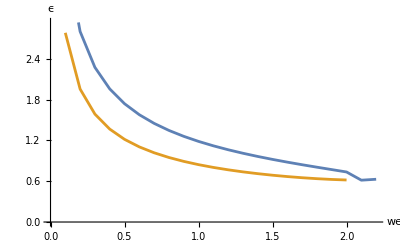

```mathematica
ListLinePlot[{ll,rr},AxesLabel->{"we","ϵ"}]
```

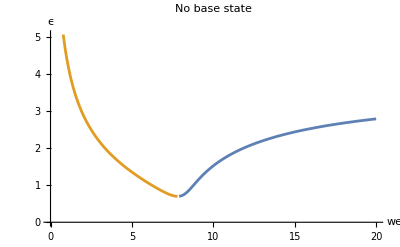

```mathematica
ListLinePlot[{lls,rrs},AxesLabel->{"we","ϵ"},PlotLabel->"No base state"]
```

```mathematica
ContourPlot[{zetak-1-ϵ^2*((1/2) (g2+g3-√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0,zetak-1-ϵ^2*((1/2) (g2+g3+√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0},{we,10,70},{ϵ,0,0.5},Frame->False,Axes->True,AxesLabel->{"We","A/R"}(*,PlotPoints->200*)]
```

-Graphics-

```mathematica
mu1
```

0.71

-Graphics-

```mathematica
zetak
```

zetak

```mathematica
h21eqn[oh_,ρ1_,ρ2_,μ1_,μ2_,m_,n_]
```

```mathematica
Cos[9Pi/8]//N
```

-0.92388

```mathematica
Cos[7Pi/8]//N
```

-0.92388

```mathematica
k212fun=
```

```mathematica
k212fun=Integrate[TrigReduce[(D[eta1,θ]*D[phi12,θ]+(1/Sin[θ])^2*(D[eta1,φ]*D[phi12,φ])+D[eta2,θ]*D[phi11,θ]+(1/Sin[θ])^2*(D[eta2,φ]*D[phi11,φ])+eta1(D[phi11,r,θ]*D[eta1,θ]+1/Sin[θ]^2*(D[eta1,φ]*D[phi11,r,φ])-2*D[phi11,θ]*D[eta1,θ]-2/Sin[θ]^2*(D[phi11,φ]*D[eta1,φ]))-eta2*D[phi11,r,r]-eta1*D[phi12,r,r]-eta1^2/2*D[phi11,r,r,r])-(D[eta1,θ]*D[phi22,θ]+(1/Sin[θ])^2*(D[eta1,φ]*D[phi22,φ])+D[eta2,θ]*D[phi21,θ]+(1/Sin[θ])^2*(D[eta2,φ]*D[phi21,φ])+eta1(D[phi21,r,θ]*D[eta1,θ]+1/Sin[θ]^2*(D[eta1,φ]*D[phi21,r,φ])-2*D[phi21,θ]*D[eta1,θ]-2/Sin[θ]^2*(D[phi21,φ]*D[eta1,φ]))-eta2*D[phi21,r,r]-eta1*D[phi22,r,r]-eta1^2/2*D[phi21,r,r,r])]*realkl[2,1]*Sin[θ],{θ,0,Pi/2},{φ,0,2 Pi}]/.r->1//N//Simplify
```

0.426308 b020^2 b021t+0.568411 b021^2 b021t+0.434059 b021t b030^2-0.11264 b021t b120-0.11264 b020t b121+0.204081 b030t b121+b020 (0.142103 b020t b021+0.643654 b021t b030+0.193096 b021 b030t-0.11264 b121t-0.11264 k121-0.135168 l121)+0.116618 b030 l121+b021 (0.430442 b030 b030t-0.11264 b120t+0.204081 b130t-0.11264 k120+0.204081 k130-0.135168 l120+0.204081 l130)

```mathematica
phii2t
```

1/8 (b120tt+k120t) √(5/π) r^2 (-1+3 Cos[θ]^2)+1/12 (b130tt+k130t) √(7/π) r^3 (-3 Cos[θ]+5 Cos[θ]^3)-1/4 (b121tt+k121t) √(15/π) r^2 Cos[θ] Cos[φ] Sin[θ]

```mathematica
phi22
```

-((b120t+k120) √(5/π) (-1+3 Cos[θ]^2))/(12 r^3)-((b130t+k130) √(7/π) (-3 Cos[θ]+5 Cos[θ]^3))/(16 r^4)+((b121t+k121) √(5/(3 π)) Cos[θ] Cos[φ] Sin[θ])/(2 r^3)

```mathematica
n212fun=Integrate[TrigReduce[eta1*(D[phi12t,r]-D[phi22t,r])+eta2*(D[phi11t,r]-D[phi21t,r])+eta1^2/2*(D[phi11t,r,r]-D[phi21t,r,r])+(D[phi11*r]*D[phi12,r]-D[phi21*r]*D[phi22,r])+(D[phi11,θ]*D[phi12,θ]-D[phi21,θ]*D[phi22,θ])+1/Sin[θ]^2*(D[phi11,φ]*D[phi12,φ]-D[phi21,φ]*D[phi22,φ])+eta1*(D[phi11,r]*D[phi11,r,r]-D[phi21,r]*D[phi21,r,r])+eta1*(D[phi11,θ]*D[phi11,r,θ]-D[phi21,θ]*D[phi21,r,θ]+1/Sin[θ]^2*D[phi11,φ]*D[phi11,r,φ]-1/Sin[θ]^2*D[phi21,φ]*D[phi21,r,φ]-D[phi11,θ]^2+D[phi21,θ]^2-1/Sin[θ]^2*D[phi11,φ]+1/Sin[θ]^2*D[phi21,φ])-2/wer*(eta1*((1-2-2^2)*b120*realkl[2,0]+(1-2-2^2)*b121*realkl[2,1]+(1-3-3^2)*b130*realkl[3,0])+eta2*((1-2-2^2)*b020*realkl[2,0]+(1-2-2^2)*b021*realkl[2,1]+(1-3-3^2)*b031*realkl[3,0]))]*realkl[2,1]*Sin[θ],{θ,0,Pi/2},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

0.0710513 b020^2 b021tt+0.213154 b021^2 b021tt+0.0306502 b020t b021t b030+0.0874146 b021tt b030^2+0.35629 b021t b030 b030t+0.0563199 b021t b120t+0.0563199 b020t b121t-0.0631679 b030t b121t-0.0777451 b021t b130t+0.0563199 b021t k120+0.0563199 b020t k121-0.0631679 b030t k121-0.0777451 b021t k130+0.0145772 b030t l121+b020 (0.165786 b020t b021t+0.0919505 b021tt b030+0.151718 b021t b030t-0.0450559 l121t)+0.0583088 b030 l121t+0.00971813 b021t l130+(0.901119 b020 b121)/wer-(0.583088 b030 b121)/wer-(1.28279 b031 b121)/wer+1/wer b021 (0.901119 b120-1.86588 b130+(0.37894 b020t^2+0.142103 b020 b020tt+0.553608 b021t^2+0.0919505 b020tt b030+0.634459 b020t b030t+0.523282 b030t^2+0.128731 b020 b030tt+0.244761 b030 b030tt-0.0450559 l120t+0.0583088 l130t) wer)

```mathematica
l212fun=Integrate[TrigReduce[eta1*D[phi12,r,r]+eta2*D[phi11,r,r]+1/2*eta1^2*D[phi11,r,r,r]-(eta1*D[phi22,r,r]+eta2*D[phi21,r,r]+1/2*eta1^2*D[phi21,r,r,r])]*realkl[2,1]*Sin[θ],{θ,0,Pi/2},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

-0.284205 b020^2 b021t-0.852616 b021^2 b021t-0.349659 b021t b030^2+0.22528 b021t b120+0.22528 b020t b121-0.408162 b030t b121-0.291544 b030 b121t-0.291544 b021t b130-0.291544 b030 k121+b020 (-0.568411 b020t b021-0.367802 b021t b030-0.514923 b021 b030t+0.22528 b121t+0.22528 k121+0.180224 l121)-0.233235 b030 l121+b021 (-0.367802 b020t b030-0.979044 b030 b030t+0.22528 b120t-0.408162 b130t+0.22528 k120-0.408162 k130+0.180224 l120-0.291544 l130)

```mathematica
v31term=eta1*D[phi2t,r]+eta2*D[phi1t,r]+D[phi1*r]*D[phi2,r]+D[phi1,θ]*D[phi2,θ]+1/Sin[θ]^2*D[phi1,φ]*D[phi2,φ](*+2/wer*(eta1*((1-2-2^2)*b120*SphericalHarmonicY[2,0,θ,φ]+(1-3-3^2)*b131*realkl[3,1]+(1-4-4^2)*b140*SphericalHarmonicY[4,0,θ,φ])+eta2*((1-2-2^2)*b020*SphericalHarmonicY[2,0,θ,φ]+(1-3-3^2)*b031*realkl[3,1]+(1-4-4^2)*b040*SphericalHarmonicY[4,0,θ,φ]))*);
```

```mathematica
Clear[k120f]
```

```mathematica
k201f[0.02,0.7,0.5,0.5,0.5,2]
```

-0.004703 Cos[2 t]-0.00910368 c0 Cos[2 t]+0.111069 d0 Cos[2 t]+0.135168 c0 d0 Cos[2 t]-0.120336 Sin[2 t]-0.111069 c0 Sin[2 t]-0.0675839 c0^2 Sin[2 t]-0.00910368 d0 Sin[2 t]+0.0675839 d0^2 Sin[2 t]

```mathematica
b020
```

1.23256 Cos[t]+c0 Cos[t]-0.101026 Sin[t]+d0 Sin[t]

```mathematica
bkl0fun[0.02,0.7,0.5,0.5,0.5,2,0,2]
```

```mathematica
k201f[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[c0,d0,b020,p20now,p31now,p40now,b020t,b020tt,b022,b022t,b022tt,b051,b051t,b051tt,b031,b031t,b031tt,b040,b040t,b040tt,b042,b042t,b042tt,b060,b060t,b060tt];

wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
delta=oh/(√wer);
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
b020t=D[b020,t]//Simplify;
b021t=D[b021,t]//Simplify;
b030t=D[b030,t]//Simplify;
b020tt=D[b020,t,t]//Simplify;
b021tt=D[b021,t,t]//Simplify;
b030tt=D[b030,t,t]//Simplify;

k120ff=0.09011187578643427 b020 b020t+0.045055937893217136 b021 b021t+0.168208834801344 b030 b030t;
k1klnow=k120ff//TrigReduce//Chop)
```

```mathematica
k211f[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[c0,d0,b020,p20now,p31now,p40now,b020t,b020tt,b022,b022t,b022tt,b051,b051t,b051tt,b031,b031t,b031tt,b040,b040t,b040tt,b042,b042t,b042tt,b060,b060t,b060tt];

wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
delta=oh/(√wer);
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
b020t=D[b020,t]//Simplify;
b021t=D[b021,t]//Simplify;
b030t=D[b030,t]//Simplify;
b020tt=D[b020,t,t]//Simplify;
b021tt=D[b021,t,t]//Simplify;
b030tt=D[b030,t,t]//Simplify;

k121ff=0.04505593789321714 (b020t b021+b020 b021t);
k1klnow=k121ff//TrigReduce//Chop)
```

```mathematica
Clear[k121f]
```

```mathematica
k301f[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[c0,d0,b020,b020t,b020tt,b022,b022t,b022tt,b051,b051t,b051tt,b031,b031t,b031tt,b040,b040t,b040tt,b042,b042t,b042tt,b060,b060t,b060tt,k301ff,k1klnow];

wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
delta=oh/(√wer);
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
b020t=D[b020,t]//Simplify;
b021t=D[b021,t]//Simplify;
b030t=D[b030,t]//Simplify;
b020tt=D[b020,t,t]//Simplify;
b021tt=D[b021,t,t]//Simplify;
b030tt=D[b030,t,t]//Simplify;

k301ff=0.084104417400672 b020t b030-0.168208834801344 b020 b030t;
k1klnow=k301ff//TrigReduce//Chop)
```

```mathematica
Clear[k130f]
```

```mathematica
n201f[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[c0,d0,b020,p20now,p31now,p40now,b020t,b020tt,b022,b022t,b022tt,b051,b051t,b051tt,b031,b031t,b031tt,b040,b040t,b040tt,b042,b042t,b042tt,b060,b060t,b060tt];

wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
delta=oh/(√wer);
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
b020t=D[b020,t]//Simplify;
b021t=D[b021,t]//Simplify;
b030t=D[b030,t]//Simplify;
b020tt=D[b020,t,t]//Simplify;
b021tt=D[b021,t,t]//Simplify;
b030tt=D[b030,t,t]//Simplify;

n120ff=1/wer(1.8022375157286856 b020^2+0.9011187578643428 b021^2+3.700594365629568 b030^2+0.037546614911014284 b020t^2 wer+0.018773307455507142 b021t^2 wer+0.036795682612794 b030t^2 wer);
n1klnow=n120ff//TrigReduce//Chop)
```

```mathematica
Clear[n120f]
```

```mathematica
n211f[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[c0,d0,b020,p20now,p31now,p40now,b020t,b020tt,b022,b022t,b022tt,b051,b051t,b051tt,b031,b031t,b031tt,b040,b040t,b040tt,b042,b042t,b042tt,b060,b060t,b060tt];

wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
delta=oh/(√wer);
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
b020t=D[b020,t]//Simplify;
b021t=D[b021,t]//Simplify;
b030t=D[b030,t]//Simplify;
b020tt=D[b020,t,t]//Simplify;
b021tt=D[b021,t,t]//Simplify;
b030tt=D[b030,t,t]//Simplify;

n121ff=-0.03754661491101429 b020t b021t+(1.8022375157286858 b020 b021)/wer;
n1klnow=n121ff//TrigReduce//Chop)
```

```mathematica
n301f[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[c0,d0,b020,b020t,b020tt,b022,b022t,b022tt,b051,b051t,b051tt,b031,b031t,b031tt,b040,b040t,b040tt,b042,b042t,b042tt,b060,b060t,b060tt,n130ff,n1klnow];

wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
delta=oh/(√wer);
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
b020t=D[b020,t]//Simplify;
b021t=D[b021,t]//Simplify;
b030t=D[b030,t]//Simplify;
b020tt=D[b020,t,t]//Simplify;
b021tt=D[b021,t,t]//Simplify;
b030tt=D[b030,t,t]//Simplify;

n130ff=0.042052208700336 b020t b030t+(5.382682713643008 b020 b030)/wer;
n1klnow=n130ff//TrigReduce//Chop)
```

```mathematica
Clear[n130f]
```

```mathematica
l201f[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[c0,d0,b020,p20now,p31now,p40now,b020t,b020tt,b022,b022t,b022tt,b051,b051t,b051tt,b031,b031t,b031tt,b040,b040t,b040tt,b042,b042t,b042tt,b060,b060t,b060tt];

wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
delta=oh/(√wer);
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
b020t=D[b020,t]//Simplify;
b021t=D[b021,t]//Simplify;
b030t=D[b030,t]//Simplify;
b020tt=D[b020,t,t]//Simplify;
b021tt=D[b021,t,t]//Simplify;
b030tt=D[b030,t,t]//Simplify;

l120ff=0.9011187578643428 b020 b020t+0.4505593789321714 b021 b021t+1.177461843609408 b030 b030t;
l1klnow=l120ff//TrigReduce//Chop)
```

```mathematica
l211f[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[c0,d0,b020,p20now,p31now,p40now,b020t,b020tt,b022,b022t,b022tt,b051,b051t,b051tt,b031,b031t,b031tt,b040,b040t,b040tt,b042,b042t,b042tt,b060,b060t,b060tt];

wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
delta=oh/(√wer);
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
b020t=D[b020,t]//Simplify;
b021t=D[b021,t]//Simplify;
b030t=D[b030,t]//Simplify;
b020tt=D[b020,t,t]//Simplify;
b021tt=D[b021,t,t]//Simplify;
b030tt=D[b030,t,t]//Simplify;

l121ff=0.4505593789321715 (b020t b021+b020 b021t);
l1klnow=l121ff//TrigReduce//Chop)
```

```mathematica
l301f[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[c0,d0,b020,p20now,p31now,p40now,b020t,b020tt,b022,b022t,b022tt,b051,b051t,b051tt,b031,b031t,b031tt,b040,b040t,b040tt,b042,b042t,b042tt,b060,b060t,b060tt];

wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
delta=oh/(√wer);
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
b020t=D[b020,t]//Simplify;
b021t=D[b021,t]//Simplify;
b030t=D[b030,t]//Simplify;
b020tt=D[b020,t,t]//Simplify;
b021tt=D[b021,t,t]//Simplify;
b030tt=D[b030,t,t]//Simplify;

l121ff=0.8410441740067199 b020t b030+1.177461843609408 b020 b030t;
l1klnow=l121ff//TrigReduce//Chop)
```

```mathematica
Integrate[eta1*(a1*realkl[2,0]+a3*realkl[3,0])*realkl[2,0],{θ,0,Pi},{φ,0,2 Pi}]
```

(5 (232 a1 b020+259 a3 b030) √(5 π))/4096

```mathematica
nm0[k_]:=√((2k+1)/(4*Pi));
```

```mathematica
n201f[0,0,1,0,0,2]
```

64.6106-0.355257 c0+0.1408 c0^2+0.1408 d0^2+50.7729 Cos[2 t]-0.213154 c0 Cos[2 t]+0.0844799 c0^2 Cos[2 t]-0.0844799 d0^2 Cos[2 t]-0.213154 d0 Sin[2 t]+0.16896 c0 d0 Sin[2 t]

```mathematica
t201=Integrate[eta1*(mkl[2,0]*realkl[2,0]+mkl[2,1]*realkl[2,1]+mkl[3,0]*realkl[3,0])*realkl[2,0],{θ,0,Pi},{φ,0,2 Pi}];
```

```mathematica
b201[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[f1,f2,f3,f4,f5,f44,f55,Δk,k,eta1,b020,b021,b030,forcing201];k=2;l=0;
eta1=b020*realkl[2,0]+(b021)*realkl[2,1]+b030*realkl[3,0];
tkl1=Integrate[eta1*(mkl[2,0]*realkl[2,0]+mkl[2,1]*realkl[2,1]+mkl[3,0]*realkl[3,0])*realkl[2,0]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}];
nkl1=n201f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
kkl1=k201f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
lkl1=l201f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
kkl1t=D[kkl1,t];
lkl1t=D[lkl1,t];
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
δ=oh/(√wer);
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wer));fk=(k(k+1))/(ρ1(k+1)+ρ2*k);
Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;gk=(ρ2*k)/(ρ1*(k+1)+ρ2*k);hk=2δ*μ2*(k+2);
forcing201=(ρ2-ρ1)*fk*tkl1*Sin[t]-kkl1t-2*Δk*kkl1-gk*lkl1t-hk*lkl1-fk*nkl1;
f1=Integrate[(1/(2Pi))*forcing201,{t,-Pi,Pi}];
f44=Integrate[(1/Pi)*forcing201*Cos[2t],{t,-Pi,Pi}];f55=Integrate[(1/Pi)*forcing201*Sin[2t],{t,-Pi,Pi}];
(*Δk=delta*(k+1)*(k+2);ζk=√((1/wer)(k^2-1)(k+2));*)f4=f44;f5=f55;

b201sol=f1/ζk^2+((-4 f5 Δk+f4 (-4+ζk^2)) Cos[2 t]+(4 f4 Δk+f5 (-4+ζk^2)) Sin[2 t])/(16 Δk^2+(-4+ζk^2)^2)//TrigReduce//Simplify//Chop)
```

```mathematica
forcing201
```

0.+0.195146 Cos[2 t]+0.208392 c0 Cos[2 t]+0.135168 c0^2 Cos[2 t]-0.135168 d0^2 Cos[2 t]-0.000513647 Sin[t] (14 √35 (0.-0.666243 Cos[t])+75 (0.+1.1563 Cos[t]+c0 Cos[t]+d0 Sin[t]))+0.208392 d0 Sin[2 t]+0.270336 c0 d0 Sin[2 t]-0.332226 (-1.72746 Cos[2 t]-2.08392 c0 Cos[2 t]-1.35168 c0^2 Cos[2 t]+1.35168 d0^2 Cos[2 t]-2.08392 d0 Sin[2 t]-2.70336 c0 d0 Sin[2 t])-1.99336 (0.20211+0.217075 c0+0.1408 c0^2+0.1408 d0^2+0.135577 Cos[2 t]+0.130245 c0 Cos[2 t]+0.0844799 c0^2 Cos[2 t]-0.0844799 d0^2 Cos[2 t]+0.130245 d0 Sin[2 t]+0.16896 c0 d0 Sin[2 t])

```mathematica
b020
```

1.14703 Cos[t]+c0 Cos[t]-0.103071 Sin[t]+d0 Sin[t]

```mathematica
b201[0.02,0.67,0.5,0.5,0.5,2]
```

-0.397452-0.429241 c0-0.280664 c0^2+0.0193092 d0-0.280664 d0^2+(-0.162486-0.138668 c0^2+c0 (-0.212723+0.0104421 d0)-0.0174917 d0+0.138668 d0^2) Cos[2 t]+(0.0125894+0.0174917 c0-0.00522106 c0^2-0.212723 d0-0.277337 c0 d0+0.00522106 d0^2) Sin[2 t]

```mathematica
b301[0,0.67,0.5,0,0,2]
```

0.108143+0.093525 c0-0.00610663 d0+(0.505873+0.805274 c0+0.318067 c0^2+0.0301327 d0-0.318067 d0^2) Cos[2 t]+(-0.0178752-0.0301327 c0+0.805274 d0+0.636134 c0 d0) Sin[2 t]

```mathematica
b030
```

0.-0.666243 Cos[t]

```mathematica
b211[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[f1,f2,f3,f4,f5,Δk,k,eta1,b020,b021,b030,forcing211];k=2;l=1;
eta1=b020*realkl[2,0]+(b021)*realkl[2,1]+b030*realkl[3,0];
tkl1=Integrate[eta1*(mkl[2,0]*realkl[2,0]+mkl[2,1]*realkl[2,1]+mkl[3,0]*realkl[3,0])*realkl[k,l]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}];
nkl1=n211f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
kkl1=k211f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
lkl1=l211f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
kkl1t=D[kkl1,t];
lkl1t=D[lkl1,t];
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
δ=oh/(√wer);
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wer));fk=(k(k+1))/(ρ1(k+1)+ρ2*k);
Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;gk=(ρ2*k)/(ρ1*(k+1)+ρ2*k);hk=2δ*μ2*(k+2);
forcing201=(ρ2-ρ1)*fk*tkl1*Sin[t]-kkl1t-2*Δk*kkl1-gk*lkl1t-hk*lkl1-fk*nkl1;
f1=Integrate[(1/(2Pi))*forcing201,{t,-Pi,Pi}];
f4=Integrate[(1/Pi)*forcing201*Cos[2t],{t,-Pi,Pi}];f5=Integrate[(1/Pi)*forcing201*Sin[2t],{t,-Pi,Pi}];
(*Δk=delta*(k+1)*(k+2);ζk=√((1/wer)(k^2-1)(k+2));*)

b201sol=f1/ζk^2+((-4 f5 Δk+f4 (-4+ζk^2)) Cos[2 t]+(4 f4 Δk+f5 (-4+ζk^2)) Sin[2 t])/(16 Δk^2+(-4+ζk^2)^2)//TrigReduce//Simplify//Chop)
```

```mathematica
b301[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[f1,f2,f3,f4,f5,Δk,k,eta1,b020,b021,b030,forcing301];k=3;l=0;
eta1=b020*realkl[2,0]+(b021)*realkl[2,1]+b030*realkl[3,0];
tkl1=Integrate[eta1*(mkl[2,0]*realkl[2,0]+mkl[2,1]*realkl[2,1]+mkl[3,0]*realkl[3,0])*realkl[k,l]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}];
nkl1=n301f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
kkl1=k301f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
lkl1=l301f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
kkl1t=D[kkl1,t];
lkl1t=D[lkl1,t];
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
delta=oh/(√wer);ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wer));fk=(k(k+1))/(ρ1(k+1)+ρ2*k);
Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;gk=(ρ2*k)/(ρ1*(k+1)+ρ2*k);hk=2δ*μ2*(k+2);
forcing301=(ρ2-ρ1)*fk*tkl1*Sin[t]-kkl1t-2*Δk*kkl1-gk*lkl1t-hk*lkl1-fk*nkl1;
f1=Integrate[(1/(2Pi))*forcing301,{t,-Pi,Pi}];
f4=Integrate[(1/Pi)*forcing301*Cos[2t],{t,-Pi,Pi}];f5=Integrate[(1/Pi)*forcing301*Sin[2t],{t,-Pi,Pi}];
Δk=delta*(k+1)*(k+2);ζk=√((1/wer)(k^2-1)(k+2));

b301sol=f1/ζk^2+((-4 f5 Δk+f4 (-4+ζk^2)) Cos[2 t]+(4 f4 Δk+f5 (-4+ζk^2)) Sin[2 t])/(16 Δk^2+(-4+ζk^2)^2)//TrigReduce//Simplify//Chop)
```

```mathematica
b301[0.026,2,1,1,1,2]
```

0.0872234+0.135277 c0-0.166881 d0+(0.276356-0.326047 c0-0.900938 d0) Cos[2 t]+(1.63569+0.900938 c0-0.326047 d0) Sin[2 t]

```mathematica
t2kl[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,kr_]:=(Clear[c0,d0,b020,p20now,p31now,p40now,b020t,b020tt,b022,b022t,b022tt,b051,b051t,b051tt,b031,b031t,b031tt,b040,b040t,b040tt,b042,b042t,b042tt,b060,b060t,b060tt];

wer=(kr^2-1)(kr+2);(*weber number for the resonance mode*)
delta=oh/(√wer);
b120=b201[oh,ρ1,ρ2,μ1,μ2,2,0,kr];
b121=b211[oh,ρ1,ρ2,μ1,μ2,2,1,kr];
b130=b301[oh,ρ1,ρ2,μ1,μ2,3,0,kr];
eta2=b120*realkl[2,0]+(b121)*realkl[2,1]+b130*realkl[3,0];
tkl1=Integrate[eta2*(nm0[2]*realkl[2,0]+nm0[3]*realkl[3,0])*realkl[k,l],{θ,0,Pi},{φ,0,2 Pi}]//TrigReduce//Chop)
```

```mathematica
k212f[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[c0,d0,b020,b021,b030,b020t,b020tt,b021t,b021tt,b030t,b030tt,b120,b121,b130,k120,k121,k130,l120,l121,l130,b120t,b121t,b130t,k212ff,k2klnow];

wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
delta=oh/(√wer);
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
b020t=D[b020,t]//Simplify;b021t=D[b021,t]//Simplify;b030t=D[b030,t]//Simplify;
b020tt=D[b020,t,t]//Simplify;b021tt=D[b021,t,t]//Simplify;b030tt=D[b030,t,t]//Simplify;
b120=b201[oh,ρ1,ρ2,μ1,μ2,kr,lr];
b121=b211[oh,ρ1,ρ2,μ1,μ2,kr,lr];
b130=b301[oh,ρ1,ρ2,μ1,μ2,kr,lr];
k120=k201f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
k121=k211f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
k130=k301f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
l120=l201f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
l121=l211f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
l130=l301f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
b120t=D[b120,t];b121t=D[b121,t];b130t=D[b130,t];

k212ff=0.42630788328186253 b020^2 b021t+0.5684105110424833 b021^2 b021t+0.43405893570516907 b021t b030^2-0.11263984473304287 b021t b120-0.11263984473304287 b020t b121+0.20408080688521937 b030t b121+b020 (0.14210262776062083 b020t b021+0.6436536512152659 b021t b030+0.1930960953645798 b021 b030t-0.11263984473304288 b121t-0.11263984473304288 k121-0.13516781367965144 l121)+0.11661760393441106 b030 l121+b021 (0.43044177790762606 b030 b030t-0.11263984473304287 b120t+0.20408080688521937 b130t-0.11263984473304287 k120+0.20408080688521937 k130-0.13516781367965144 l120+0.20408080688521937 l130);
k2klnow=k212ff//TrigReduce//Chop)
```

```mathematica
k212f[0.02,0.7,0.5,0.5,0.5,2]
```

-0.0877897 c0 Cos[t]-0.0559945 c0^2 Cos[t]+0.000519548 c0^3 Cos[t]+0.15 d0 Cos[t]+0.295317 c0 d0 Cos[t]+0.256107 c0^2 d0 Cos[t]-0.093676 d0^2 Cos[t]+0.000519548 c0 d0^2 Cos[t]+0.256107 d0^3 Cos[t]-0.104832 c0 Cos[3 t]-0.113301 c0^2 Cos[3 t]+0.00155864 c0^3 Cos[3 t]+0.0867123 d0 Cos[3 t]+0.222335 c0 d0 Cos[3 t]+0.70778 c0^2 d0 Cos[3 t]+0.113301 d0^2 Cos[3 t]-0.00467593 c0 d0^2 Cos[3 t]-0.235927 d0^3 Cos[3 t]-0.141883 c0 Sin[t]-0.154999 c0^2 Sin[t]-0.256107 c0^3 Sin[t]+0.0622896 d0 Sin[t]+0.0376815 c0 d0 Sin[t]+0.000519548 c0^2 d0 Sin[t]+0.140319 d0^2 Sin[t]-0.256107 c0 d0^2 Sin[t]+0.000519548 d0^3 Sin[t]-0.0867123 c0 Sin[3 t]-0.111168 c0^2 Sin[3 t]-0.235927 c0^3 Sin[3 t]-0.104832 d0 Sin[3 t]-0.226602 c0 d0 Sin[3 t]+0.00467593 c0^2 d0 Sin[3 t]+0.111168 d0^2 Sin[3 t]+0.70778 c0 d0^2 Sin[3 t]-0.00155864 d0^3 Sin[3 t]

```mathematica
n212f[0.02,0.7,0.5,0.5,0.5,2]
```

0.141527 c0 Cos[t]+0.103311 c0^2 Cos[t]-0.0388695 c0^3 Cos[t]+0.0338048 d0 Cos[t]-0.0360173 c0 d0 Cos[t]+0.000865913 c0^2 d0 Cos[t]+0.0460325 d0^2 Cos[t]-0.0388695 c0 d0^2 Cos[t]+0.000865913 d0^3 Cos[t]-0.0259412 c0 Cos[3 t]-0.0668027 c0^2 Cos[3 t]-0.329783 c0^3 Cos[3 t]-0.0078983 d0 Cos[3 t]-0.0959533 c0 d0 Cos[3 t]-0.000519548 c0^2 d0 Cos[3 t]+0.0668027 d0^2 Cos[3 t]+0.989348 c0 d0^2 Cos[3 t]+0.000173183 d0^3 Cos[3 t]+0.0042258 c0 Cos[t] k130f[0.02,0.7,0.5,0.5,0.5,2]+0.0534873 c0 Sin[t]+0.0694006 c0^2 Sin[t]-0.000865913 c0^3 Sin[t]-0.0514432 d0 Sin[t]+0.0572783 c0 d0 Sin[t]-0.0388695 c0^2 d0 Sin[t]+0.0333833 d0^2 Sin[t]-0.000865913 c0 d0^2 Sin[t]-0.0388695 d0^3 Sin[t]+0.0042258 d0 k130f[0.02,0.7,0.5,0.5,0.5,2] Sin[t]+0.0078983 c0 Sin[3 t]+0.0479767 c0^2 Sin[3 t]+0.000173183 c0^3 Sin[3 t]-0.0259412 d0 Sin[3 t]-0.133605 c0 d0 Sin[3 t]-0.989348 c0^2 d0 Sin[3 t]-0.0479767 d0^2 Sin[3 t]-0.000519548 c0 d0^2 Sin[3 t]+0.329783 d0^3 Sin[3 t]

```mathematica
n212f[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[c0,d0,b020,b021,b030,b020t,b020tt,b021t,b021tt,b030t,b030tt,b120,b121,b130,k120,k121,k130,l120,l121,l130,b120t,b121t,b130t,n212ff,n2klnow];

wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
delta=oh/(√wer);
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
b020t=D[b020,t]//Simplify;b021t=D[b021,t]//Simplify;b030t=D[b030,t]//Simplify;
b020tt=D[b020,t,t]//Simplify;b021tt=D[b021,t,t]//Simplify;b030tt=D[b030,t,t]//Simplify;
b120=b201[oh,ρ1,ρ2,μ1,μ2,kr,lr];
b121=b211[oh,ρ1,ρ2,μ1,μ2,kr,lr];
b130=b301[oh,ρ1,ρ2,μ1,μ2,kr,lr];
k120=k201f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
k121=k211f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
k130=k301f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
l120=l201f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
l121=l211f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
l130=l301f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
b120t=D[b120,t];b121t=D[b121,t];b130t=D[b130,t];
l120t=D[l120,t];l121t=D[l121,t];l130t=D[l130,t];


n212ff=0.07105131388031043 b020^2 b021tt+0.21315394164093127 b021^2 b021tt+0.030650173867393618 b020t b021t b030+0.08741464677395767 b021tt b030^2+0.356290043057993 b021t b030 b030t+0.05631992236652144 b021t b120t+0.05631992236652144 b020t b121t-0.063167868797806 b030t b121t-0.07774506928960738 b021t b130t+0.05631992236652144 b021t k120+0.05631992236652144 b020t k121-0.063167868797806 b030t k121-0.07774506928960738 b021t k130+0.014577200491801383 b030t l121+b020 (0.16578639905405768 b020t b021t+0.09195052160218087 b021tt b030+0.1517183606435984 b021t b030t-0.04505593789321715 l121t)+0.058308801967205545 b030 l121t+0.009718133661200922 b021t l130+(0.9011187578643429 b020 b121)/wer-(0.5830880196720554 b030 b121)/wer+1/wer b021 (0.9011187578643429 b120-1.865881662950577 b130+(0.37894034069498894 b020t^2+0.14210262776062085 b020 b020tt+0.5536081539840855 b021t^2+0.09195052160218087 b020tt b030+0.634458599055048 b020t b030t+0.5232821613778984 b030t^2+0.1287307302430532 b020 b030tt+0.2447610109670815 b030 b030tt-0.04505593789321714 l120t+0.05830880196720553 l130t) wer);
n2klnow=n212ff//TrigReduce//Chop)
```

```mathematica
l212f[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[c0,d0,b020,b021,b030,b020t,b020tt,b021t,b021tt,b030t,b030tt,b120,b121,b130,k120,k121,k130,l120,l121,l130,b120t,b121t,b130t,l212ff,l2klnow];

wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
delta=oh/(√wer);
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
b020t=D[b020,t]//Simplify;b021t=D[b021,t]//Simplify;b030t=D[b030,t]//Simplify;
b020tt=D[b020,t,t]//Simplify;b021tt=D[b021,t,t]//Simplify;b030tt=D[b030,t,t]//Simplify;
b120=b201[oh,ρ1,ρ2,μ1,μ2,kr,lr];
b121=b211[oh,ρ1,ρ2,μ1,μ2,kr,lr];
b130=b301[oh,ρ1,ρ2,μ1,μ2,kr,lr];
k120=k201f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
k121=k211f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
k130=k301f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
l120=l201f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
l121=l211f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
l130=l301f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
b120t=D[b120,t];b121t=D[b121,t];b130t=D[b130,t];
l120t=D[l120,t];l121t=D[l121,t];l130t=D[l130,t];



l212ff=-0.2842052555212417 b020^2 b021t-0.8526157665637251 b021^2 b021t-0.3496585870958307 b021t b030^2+0.22527968946608573 b021t b120+0.22527968946608573 b020t b121-0.40816161377043875 b030t b121-0.2915440098360277 b030 b121t-0.2915440098360277 b021t b130-0.2915440098360277 b030 k121+b020 (-0.5684105110424834 b020t b021-0.36780208640872347 b021t b030-0.5149229209722128 b021 b030t+0.22527968946608576 b121t+0.22527968946608576 k121+0.18022375157286857 l121)-0.23323520786882213 b030 l121+b021 (-0.36780208640872347 b020t b030-0.979044043868326 b030 b030t+0.22527968946608573 b120t-0.40816161377043875 b130t+0.22527968946608573 k120-0.40816161377043875 k130+0.18022375157286857 l120-0.2915440098360277 l130);
l2klnow=l212ff//TrigReduce//Chop)
```

```mathematica
bkl0fun[0.02,0.7,0.5,0.5,0.5,2,0,2,1]
```

0.-9.76696 Sin[t]

```mathematica
b020
```

0.-9.76696 Sin[t]

```mathematica
k212f[0.02,0.7,0.5,0.5,0.5,2,1]
```

0.139615 c0 Cos[t]+2.09011 d0 Cos[t]-9.86024 c0 Cos[1. t]+0.000109138 c0^3 Cos[1. t]+298.137 d0 Cos[1. t]+0.134504 c0^2 d0 Cos[1. t]+0.000109138 c0 d0^2 Cos[1. t]+0.134504 d0^3 Cos[1. t]+0.0539565 c0 Cos[3 t]+1.27763 d0 Cos[3 t]-10.4138 c0 Cos[3. t]+0.000327414 c0^3 Cos[3. t]-297.275 d0 Cos[3. t]+0.40679 c0^2 d0 Cos[3. t]-0.000982242 c0 d0^2 Cos[3. t]-0.135597 d0^3 Cos[3. t]-3.30591 c0 Sin[t]+0.139615 d0 Sin[t]-357.469 c0 Sin[1. t]-0.134504 c0^3 Sin[1. t]+9.86024 d0 Sin[1. t]+0.000109138 c0^2 d0 Sin[1. t]-0.134504 c0 d0^2 Sin[1. t]+0.000109138 d0^3 Sin[1. t]-1.27763 c0 Sin[3 t]+0.0539565 d0 Sin[3 t]+297.275 c0 Sin[3. t]-0.135597 c0^3 Sin[3. t]-10.4138 d0 Sin[3. t]+0.000982242 c0^2 d0 Sin[3. t]+0.40679 c0 d0^2 Sin[3. t]-0.000327414 d0^3 Sin[3. t]

```mathematica
forcing201=(ρ2-ρ1)*fk*tkl1*Sin[t]-kkl1t-2*Δk*kkl1-gk*lkl1t-hk*lkl1-fk*nkl1;
```

```mathematica
harmonic21[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,kr_,lr_]:=(Clear[c0,d0,b020,b021,b030,b020t,b020tt,b021t,b021tt,b030t,b030tt,b120,b121,b130,k120,k121,k130,l120,l121,l130,b120t,b121t,b130t,tkl1,tkl2,eta1,fk,b211sol];
eta2=(*b120*realkl[2,0]+*)b211sol*realkl[2,1](*+b130*realkl[3,0]*);
tkl2=Integrate[eta2*(mkl[2,0]*realkl[2,0]+mkl[2,1]*realkl[2,1]+mkl[3,0]*realkl[3,0])*realkl[k,l]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}];
wek=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);
delta=oh/wek;
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wer));fk=(k(k+1))/(ρ1(k+1)+ρ2*k);
Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;gk=(ρ2*k)/(ρ1*(k+1)+ρ2*k);hk=2δ*μ2*(k+2);
zetak=wer/we;
b211sol=b211[oh,ρ1,ρ2,μ1,μ2,kr,lr];
kkl2=k212f[oh,ρ1,ρ2,μ1,μ2,kr,lr];kkl2t=D[kkl2,t];
nkl2=n212f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
lkl2=l212f[oh,ρ1,ρ2,μ1,μ2,kr,lr];lkl2t=D[lkl2,t];
forcing212=(ρ2-ρ1)*fk*tkl2*Sin[t]-kkl2t-2*Δk*kkl2-gk*lkl2t-hk*lkl2-fk*nkl2;//TrigReduce;
fcos=Integrate[(1/Pi)*forcing212*Cos[t],{t,-Pi,Pi}];
fsin=Integrate[(1/Pi)*forcing212*Sin[t],{t,-Pi,Pi}];
g1=Coefficient[fsin,c0]-Coefficient[fsin,c0*d0^2]*d0^2//FullSimplify//Chop;g2=Coefficient[fsin,d0]-Coefficient[fsin,d0*c0^2]*c0^2//FullSimplify//Chop;g3=Coefficient[fcos,c0]-Coefficient[fcos,c0*d0^2]*d0^2//FullSimplify//Chop;g4=Coefficient[fcos,d0]-Coefficient[fcos,d0*c0^2]*c0^2//FullSimplify//Chop;
α=Coefficient[fcos,c0^3]//Chop;
β=Coefficient[fcos,d0^3]//Chop;

wek=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);
delta=oh/(√wek);
Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;
data={g1,g2,g3,g4,α,β,Δk,wer}(*;ContourPlot[{zetak-1-ϵ^2*((1/2) (g2+g3-√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0,zetak-1-ϵ^2*((1/2) (g2+g3+√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0},{we,10,70},{ϵ,0,0.5},Frame->False,Axes->True,AxesLabel->{"We","A/R"}(*,PlotPoints->200*)]*)
)
```

```mathematica
harmonic21[0.02,0.7,0.5,0.5,0.5,2,1,2,1]
```

{13.5044,-844.346,-689.325,22.751,-0.400045,0.00570439,0.0501485,27.907}

```mathematica
(g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4
```

24031.6+(4 (0.100297+13.5044 ϵ^2) (-0.100297+22.751 ϵ^2))/ϵ^4

```mathematica
Solve[24031.60632735587+(4 (0.10029701698998988+13.504418503560936 ϵ^2) (-0.10029701698998988+22.75099356674131 ϵ^2))/ϵ^4==0,ϵ]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{ϵ→-0.0345082},{ϵ→0.-0.0365742 ⅈ},{ϵ→0.+0.0365742 ⅈ},{ϵ→0.0345082}}

```mathematica
ContourPlot[{zetak-1-ϵ^2*((1/2) (g2+g3-√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0,zetak-1-ϵ^2*((1/2) (g2+g3+√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0},{we,10,70},{ϵ,0,5},Frame->False,Axes->True,AxesLabel->{"We","A/R"}(*,PlotPoints->200*)]
```

-Graphics-

```mathematica
Integrate[realkl[2,1]*realkl[2,1]*realkl[2,1](**realkl[2,1]*)*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]
```

0

```mathematica
Integrate[realkl[2,0]*realkl[2,1]*realkl[2,1]*realkl[2,1]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]
```

0

```mathematica
Integrate[realkl[3,1]*realkl[3,1]*(*realkl[3,1]**)realkl[3,1]*Sin[θ],{θ,0,Pi/2},{φ,0,2 Pi}]
```

0

```mathematica
harmonic21[0.02,0.7,0.5,0.5,0.5,2,1,2]
```

{-0.0522763-0.463545 d0,-0.531762-0.463545 c0,-0.462766+0.104542 d0,-0.0190573+0.104542 c0,-0.82948,0.0184615,0.0347804,7.74194}

```mathematica
zetak
```

12/we

```mathematica
data
```

{-0.0522763-0.463545 d0,-0.531762-0.463545 c0,-0.462766+0.104542 d0,-0.0190573+0.104542 c0,-0.82948,0.0184615,dkr,7.74194,f31}

```mathematica
g1=-0.05227629836730909;
```

```mathematica
g2=-0.5317623283721141;
```

```mathematica
g3=-0.462765555464534;
```

```mathematica
g4=-0.01905729384330806;
```

```mathematica
Δk=0.01796988221070652*fk
```

0.0501485

```mathematica
ContourPlot[{zetak-1-ϵ^2*((1/2) (g2+g3-√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0,zetak-1-ϵ^2*((1/2) (g2+g3+√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0},{we,10,70},{ϵ,0,0.5},Frame->False,Axes->True,AxesLabel->{"We","A/R"}(*,PlotPoints->200*)]
```

-Graphics-

```mathematica
Integrate[eta2*(mkl[2,0]*realkl[2,0]+mkl[2,1]*realkl[2,1]+mkl[3,0]*realkl[3,0])*realkl[k,l],{θ,0,Pi},{φ,0,2 Pi}]
```

```mathematica
fsin
```

0.-0.0184615 c0^3+c0^2 (-0.032791-0.82948 d0)-0.531762 d0+0.0717511 d0^2-0.82948 d0^3+c0 (-0.0522763-0.463545 d0-0.0184615 d0^2)

```mathematica
harmonic21[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,kr_]
```

```mathematica
harmonic21[0.02,0.7,0.5,0.5,0.5,2,1,2]
```

-Graphics-

```mathematica
DSolve[x''[t]+2*mu*x'[t]+(1/4+mu^2)*x[t]==0,x[t],t]
```

{{x[t]→ⅇ^(-mu t) C[2] Cos[t/2]+ⅇ^(-mu t) C[1] Sin[t/2]}}

```mathematica
DSolve[x''[t]+2*mu*x'[t]+(1/4+mu^2)*x[t]==ⅇ^(-mu t) a Cos[t/2]+ⅇ^(-mu t) b Sin[t/2],x[t],t]
```

{{x[t]→ⅇ^(-mu t) C[2] Cos[t/2]+ⅇ^(-mu t) C[1] Sin[t/2]+ⅇ^(-mu t) (-b t Cos[t/2]+2 a Cos[t/2]^3+a t Sin[t/2]-2 b Cos[t/2]^2 Sin[t/2]+b Cos[t/2] Sin[t]+a Sin[t/2] Sin[t])}}

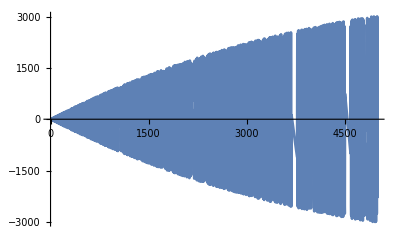

```mathematica
Plot[ⅇ^(-mu t) (-t Cos[t/2])/.mu->0.0001,{t,0,5000}]
```

```mathematica
DSolve[x''[t]+(z^2-d^2)*x[t]==f*E^(d*t)Cos[t],x[t],t]
```

{{x[t]→ⅇ^(t √(d^2-z^2)) C[1]+ⅇ^(-t √(d^2-z^2)) C[2]+(ⅇ^(d t) f (-Cos[t]+z^2 Cos[t]+2 d Sin[t]))/(1+4 d^2-2 z^2+z^4)}}

```mathematica
Series[1/r^3,{r,Infinity,5}]
```

(1/r)^3+O[1/r]^6

```mathematica
Integrate[(E^(-x^2/l^2))/(√Pi)*x^2*1/l,{x,-Infinity,Infinity}]
```

ConditionalExpression[1/(2 (1/l^2)^(3/2) l), Re[l^2]>0]

```mathematica
Clear[k]
```

```mathematica
Integrate[Exp[-(x-y)^2/(4*k*t)]/(√Pi)*x^2*1/l,{x,-Infinity,Infinity}]
```